## Definitions

## SM particles production cross-sections at various facilities

```mathematica
theta[η_]=2*ArcTan[Exp[-η]];
σppInpbFacility:=Association[{"FermilabBD"-> 40.*10^9, "SPS"->40.*10^9,"LHC"-> 72.*10^9,"FCC-hh"->104.*10^9,"Serpukhov"->40.*10^9,"ESS"->45.*10^9}]
LLHChighLumi=3000*10^3;
LFCChh=20000*10^3;
(*Cross-sections in pb of b b̄ production. For Fermilab/FCC-hh taken from pythia, for SPS taken from http://cds.cern.ch/record/2115534/files/SHiP-NOTE-2015-009.pdf?version=1, for LHC taken from FONLL at the upper bound of uncertainty*)
σppTobbInpbFacility:=Association[{"FermilabBD"->3.8,"SPS"->1.7*10^3,"LHC"->6.2*10^8,"FCC-hh"->3.4*10^9,"Serpukhov"->0.,"ESS"->0.}]
(*Cross-sections in pb of c c̄ production. For Fermilab/FCC-hh taken from pythia, for SPS taken from http://cds.cern.ch/record/2115534/files/SHiP-NOTE-2015-009.pdf?version=1, for LHC taken from FONLL at the upper bound of uncertainty*)
σppToccInpbFacility:=Association[{"FermilabBD"->0.5*10^6,"SPS"->1.8*10^7,"LHC"->1.8*10^10,"FCC-hh"->4*10^10,"Serpukhov"->0.,"ESS"->0.}]
(*Data for Higgs production. For LHC, used https://twiki.cern.ch/twiki/bin/view/LHCPhysics/HiggsEuropeanStrategy. For FCC-hh, pythia8 is used*)
σppTohInpbFacility:=Association[{"FermilabBD"-> 0.,"SPS"->0.,"LHC"->55,"FCC-hh"->552.,"Serpukhov"->0.,"ESS"->0.}]
(*Data for the production of light mesons. P means the fraction per collision*)
(*For SPS, the multiplicities are taken from https://lib-extopc.kek.jp/preprints/PDF/1991/9103/9103008.pdf*)
(*For Fermilab, obtained using the approach from https://arxiv.org/pdf/2201.05170.pdf*)
(*For Serpukhov (NuCal), the pythia8 simulation is used*)
(*For LHC/FCC-hh used EPOS-LHC*)
PppToπ0Facility:=Association[{"FermilabBD"->2.9,"SPS"->6.2,"LHC"->42.8,"FCC-hh"->73.8,"Serpukhov"->2.37,"ESS"->0.59}]
PppToηFacility:=Association[{"FermilabBD"->0.32,"SPS"->0.8,"LHC"->4.7,"FCC-hh"->8.3,"Serpukhov"->0.211,"ESS"->0.}]
PppToηprFacility:=Association[{"FermilabBD"->0.033,"SPS"->0.079,"LHC"->0.5,"FCC-hh"->1.1,"Serpukhov"->0.027,"ESS"->0.}]
PppToρ0Facility:=Association[{"FermilabBD"->0.36,"SPS"->0.548,"LHC"->5.16,"FCC-hh"->8.26,"Serpukhov"->0.294,"ESS"->0.}]
PppToωFacility:=Association[{"FermilabBD"->0.36,"SPS"->0.548,"LHC"->4.83,"FCC-hh"->7.75,"Serpukhov"->0.2983,"ESS"->0.}]
(*Production probability of charged π and μ. Currently, used only for ESS*)
PppToπchargedFacility:=Association[{"ESS"->0.3}]
PppToμFacility:=Association[{"ESS"->0.3}]
(*For J/ψ and Υ, the FCC-hh data is to be updated*)
PppToJpsiFacility:=Association[{"FermilabBD"->5.24*10^-7,"SPS"->3.5*10^-6,"LHC"->0.001,"FCC-hh"->0.,"Serpukhov"->0.,"ESS"->0.}]
PppToUpsilonFacility:=Association[{"FermilabBD"->0.,"SPS"->0.,"LHC"->1.35*10^-5,"FCC-hh"->0.,"Serpukhov"->0.,"ESS"->0.}]
(*ϕ multiplicity - per p-p collision (currently)*)
PppToPhiFacility:=Association[{"FermilabBD"->0.0106,"SPS"->0.02,"LHC"->0.53,"FCC-hh"->1.13,"Serpukhov"->8.4*10^-3,"ESS"->0.}]
(*Data for W production*)
(*For LHC, https://arxiv.org/abs/1603.09222 is used. For FCC-hh, pythia8 is used*)
σppToWInpbFacility:=Association[{"FermilabBD"-> 0.,"SPS"->0.,"LHC"->10^3*20.62/0.107,"FCC-hh"->1.1*10^6,"Serpukhov"->0.,"ESS"->0.}]
(*Maximal energy of LLP available at the given experiment*)
EmaxFacility:=Association[{"SPS"->400.,"FermilabBD"->120.,"LHC"->7000.,"FCC-hh"-> 50000.,"Serpukhov"->70.,"ESS"->2.4}]
```

## Generic definitions used to calculate acceptances

```mathematica
Boxcylpar[experiment_]:=GeometryExperiment[experiment]=="Box"||(GeometryExperiment[experiment]=="Cylinder"&&DetectorPlaneOrientationExperiment[experiment]=="Parallel");
(*Condition to define whether the LLP is inside the decay volume*)
IfLLPinsideDecVolSimple[experiment_]:=Block[{},
If[Evaluate[Boxcylpar[experiment]],
XminDecVol[zLLP_]=xToDecayVolumeCenterExperiment[zLLP,experiment]-dxDecayVolumeExperiment[zLLP,experiment]/2.;
XmaxDecVol[zLLP_]=xToDecayVolumeCenterExperiment[zLLP,experiment]+dxDecayVolumeExperiment[zLLP,experiment]/2.;
YminDecVol[zLLP_]=yToDecayVolumeCenterExperiment[zLLP,experiment]-dyDecayVolumeExperiment[zLLP,experiment]/2.;
YmaxDecVol[zLLP_]=yToDecayVolumeCenterExperiment[zLLP,experiment]+dyDecayVolumeExperiment[zLLP,experiment]/2.;
(*If the experiment has box geometry, or if it has the cylinder geometry and the detector plane is oriented parallel to the beamline, then at the given z the LLP must be within a rectangle*)
(*Otherwise*)
cnd=Boole[XminDecVol[zLLP]<xLLP<XmaxDecVol[zLLP]&&YminDecVol[zLLP]<yLLP<YmaxDecVol[zLLP]]//Simplify,
cnd=Boole[RinnerDecayVolumeExperiment[experiment,zLLP]^2<(xToDecayVolumeCenterExperiment[zLLP,experiment]-xLLP)^2+(yToDecayVolumeCenterExperiment[zLLP,experiment]-yLLP)^2<RouterDecayVolumeExperiment[experiment,zLLP]^2];
];
cnd
]
(*Condition to define whether the LLP points to the detector*)
(*x1LLPproj is the x coordinate, while x2LLPproj may be either y (if the detector plane is xy) or z (if the plane is xz)*)
Boxdec[experiment_]:=GeometryExperiment[experiment]=="Box"
IfParticlePointsToDetSimple[experiment_]:=Block[{},
(*If decay volume is detector, then all particle inside decay volume "point" to detector*)
If[DecayVolumeAsDetectorExperiment[experiment]=="True",
{cond1,cond2}={1.,0.},
x2toDetCenter=If[DetectorPlaneOrientationExperiment[experiment]=="Transverse", yToDetectorCenterExperiment[experiment],zToDetectorCenterExperiment[experiment]];
(*Considering the box detector*)
If[Evaluate[Boxdec[experiment]],
x1minDet[xLongProj_]=xToDetectorCenterExperiment[experiment]-dxDetectorExperiment[experiment,xLongProj]/2;
x1maxDet[xLongProj_]=xToDetectorCenterExperiment[experiment]+dxDetectorExperiment[experiment,xLongProj]/2;
x2minDet[xLongProj_]=If[DetectorPlaneOrientationExperiment[experiment]=="Transverse",yToDetectorCenterExperiment[experiment]-dyDetectorExperiment[experiment,xLongProj]/2,zToDetectorCenterExperiment[experiment]-dzDetectorExperiment[experiment]/2];
x2maxDet[xLongProj_]=If[DetectorPlaneOrientationExperiment[experiment]=="Transverse",yToDetectorCenterExperiment[experiment]+dyDetectorExperiment[experiment,xLongProj]/2,zToDetectorCenterExperiment[experiment]+dzDetectorExperiment[experiment]/2];
cond1=Boole[x1minDet[xLongProj]<x1LLPproj<x1maxDet[xLongProj]&&x2minDet[xLongProj]<x2LLPproj<x2maxDet[xLongProj]];
cond2=Boole[!(x1minDet[xLongProj]<x1LLPproj<x1maxDet[xLongProj]&&x2minDet[xLongProj]<x2LLPproj<x2maxDet[xLongProj])],
(*If LLP points to detector*)
cond1=Boole[RinnerDetectorExperiment[experiment,xLongProj]^2<(xToDetectorCenterExperiment[experiment]-x1LLPproj)^2+(x2toDetCenter-x2LLPproj)^2<RouterDetectorExperiment[experiment,xLongProj]^2];
(*If LLP does not point to detector*)
cond2=Boole[!(RinnerDetectorExperiment[experiment,xLongProj]^2<(xToDetectorCenterExperiment[experiment]-x1LLPproj)^2+(x2toDetCenter-x2LLPproj)^2<RouterDetectorExperiment[experiment,xLongProj]^2)]];
];
{cond1,cond2}//Simplify
]
(*The total volume of the decay volume based on the implemented conditions for the LLP to decay inside the decay volume*)
VolumeFromIf[exp_]:=
Block[{},
DX[z_]=If[GeometryExperiment[exp]=="Box",dxDecayVolumeExperiment[z,exp],2RouterDecayVolumeExperiment[exp,z]];
DY[z_]=If[GeometryExperiment[exp]=="Box",dyDecayVolumeExperiment[z,exp],2RouterDecayVolumeExperiment[exp,z]];
Xminv[z_]=xToDecayVolumeCenterExperiment[z,exp]-DX[z]/2;
Xmaxv[z_]=xToDecayVolumeCenterExperiment[z,exp]+DX[z]/2;
Yminv[z_]=yToDecayVolumeCenterExperiment[z,exp]-DY[z]/2;
Ymaxv[z_]=yToDecayVolumeCenterExperiment[z,exp]+DY[z]/2;
NIntegrate[IfLLPinsideDecVol[zLLP,xLLP,yLLP,exp],{zLLP,zToDecayVolumeExperiment[exp],zToDecayVolumeExperiment[exp]+dzDecayVolumeExperiment[exp]},{xLLP,Xminv[zLLP],Xmaxv[zLLP]},{yLLP,Yminv[zLLP],Ymaxv[zLLP]}]
]
```

## Implementation of the experiments: geometry and cross-sections

### SHiP configurations

#### Preliminary definitions

```mathematica
(*ENC3 4*8 m^2. Values taken from FairSHiP*)
(*Parameters (here in below, in m): upstream/downstream Δx for decay volume, upstream/downstream Δy for decay volume, Subscript[z, min] for decay volume, Δz for decay volume, Δx,Δy,Δz for the detector, Subscript[z, min/max] for magnet, and integrated magnetic field in Tl*m of magnet, ECAL position*)
(*The dimensions of the detector is assumed to be the same as the downstream dimensions of the decay volume*)
{ΔxUpstrSHiPECN3LoI,ΔxDownstrSHiPECN3LoI,ΔyUpstrSHiPECN3LoI,ΔyDownstrSHiPECN3LoI,zminSHiPECN3LoI,zfidSHiPECN3LoI,ΔxdetSHiPECN3LoI,ΔydetSHiPECN3LoI,ΔzdetSHiPECN3LoI,zMinMagnetSHiPECN3LoI,zMaxMagnetSHiPECN3LoI,BintSHiPECN3LoI,ECALpositionSHiPECN3LoI}={1.2,1.95*2,1.75*2,4.35*2,38,50,1.95*2,4.35*2,15,38+50+5,38+50+10,0.5,38+50+10+2}//N;
(*Alt/alt2: the decay volume and detector dimensions is proportioally smaller: 4*8 -> 4*6*)
{ΔxUpstrSHiPECN3,ΔxDownstrSHiPECN3,ΔyUpstrSHiPECN3,ΔyDownstrSHiPECN3,zminSHiPECN3,zfidSHiPECN3,ΔxdetSHiPECN3,ΔydetSHiPECN3,ΔzdetSHiPECN3,zMinMagnetSHiPECN3,zMaxMagnetSHiPECN3,BintSHiPECN3,ECALpositionSHiPECN3}={1.2,1.95*2,1.75*2,3*2,32,50,1.95*2,3*2,15,31+50+5,31+50+10,0.5,31+50+10+2}//N;
{ΔxUpstrSHiPECN3alt,ΔxDownstrSHiPECN3alt,ΔyUpstrSHiPECN3alt,ΔyDownstrSHiPECN3alt,zminSHiPECN3alt,zfidSHiPECN3alt,ΔxdetSHiPECN3alt,ΔydetSHiPECN3alt,ΔzdetSHiPECN3alt,zMinMagnetSHiPECN3alt,zMaxMagnetSHiPECN3alt,BintSHiPECN3alt,ECALpositionSHiPECN3alt}={1.2,1.95*2,1.75*2,3*2,38,50,1.95*2,3*2,15,38+50+5,38+50+10,0.5,38+50+10+2}//N;
(*Old ECN4 setup*)
{ΔxUpstrSHiPECN4,ΔxDownstrSHiPECN4,ΔyUpstrSHiPECN4,ΔyDownstrSHiPECN4,zminSHiPECN4,zfidSHiPECN4,ΔxdetSHiPECN4,ΔydetSHiPECN4,ΔzdetSHiPECN4,zMinMagnetSHiPECN4,zMaxMagnetSHiPECN4,BintSHiPECN4,ECALpositionSHiPECN4}={1.5,5,4.3,11,50,50,5,11,15,50+50+5,50+50+10,0.5,50+50+10+2}//N;
ΔySHiPconfiguration[z_,Δyupstr_,Δydownstr_,zmin_,zfid_]:=Δyupstr*((z-(zmin+zfid))/(zmin-(zmin+zfid)))+Δydownstr*((z-zmin)/((zmin+zfid)-zmin));
ΔxSHiPconfiguration[z_,Δxupstr_,Δxdownstr_,zmin_,zfid_]:=Δxupstr*((z-(zmin+zfid))/(zmin-(zmin+zfid)))+Δxdownstr*((z-zmin)/((zmin+zfid)-zmin));
{ΔxSHiPECN3LoI[z_],ΔySHiPECN3LoI[z_]}={ΔxSHiPconfiguration[z,ΔxUpstrSHiPECN3LoI,ΔxDownstrSHiPECN3LoI,zminSHiPECN3LoI,zfidSHiPECN3LoI],ΔySHiPconfiguration[z,ΔyUpstrSHiPECN3LoI,ΔyDownstrSHiPECN3LoI,zminSHiPECN3LoI,zfidSHiPECN3LoI]};
{ΔxSHiPECN4[z_],ΔySHiPECN4[z_]}={ΔxSHiPconfiguration[z,ΔxUpstrSHiPECN4,ΔxDownstrSHiPECN4,zminSHiPECN4,zfidSHiPECN4],ΔySHiPconfiguration[z,ΔyUpstrSHiPECN4,ΔyDownstrSHiPECN4,zminSHiPECN4,zfidSHiPECN4]};
{ΔxSHiPECN3[z_],ΔySHiPECN3[z_]}={ΔxSHiPconfiguration[z,ΔxUpstrSHiPECN3,ΔxDownstrSHiPECN3,zminSHiPECN3,zfidSHiPECN3],ΔySHiPconfiguration[z,ΔyUpstrSHiPECN3,ΔyDownstrSHiPECN3,zminSHiPECN3,zfidSHiPECN3]};
{ΔxSHiPECN3alt[z_],ΔySHiPECN3alt[z_]}={ΔxSHiPconfiguration[z,ΔxUpstrSHiPECN3alt,ΔxDownstrSHiPECN3alt,zminSHiPECN3alt,zfidSHiPECN3alt],ΔySHiPconfiguration[z,ΔyUpstrSHiPECN3alt,ΔyDownstrSHiPECN3alt,zminSHiPECN3alt,zfidSHiPECN3alt]};
(*Upstream/downstream dimensions of the decay volume*)
{dxDecayVolumeUpstream["SHiP-ECN3-LoI"],dxDecayVolumeUpstream["SHiP-ECN3"],dxDecayVolumeUpstream["SHiP-ECN3-alt"],dxDecayVolumeUpstream["SHiP-ECN4"]}={1.,1.,1.,1.*5/4};
{dxDecayVolumeDownstream["SHiP-ECN3-LoI"],dxDecayVolumeDownstream["SHiP-ECN3"],dxDecayVolumeDownstream["SHiP-ECN3-alt"],dxDecayVolumeDownstream["SHiP-ECN4"]}={4,4,4,5};
{dyDecayVolumeUpstream["SHiP-ECN3-LoI"],dyDecayVolumeUpstream["SHiP-ECN3"],dyDecayVolumeUpstream["SHiP-ECN3-alt"],dyDecayVolumeUpstream["SHiP-ECN4"]}={2.7*8/6.,2.7,2.7,4.3};
{dyDecayVolumeDownstream["SHiP-ECN3-LoI"],dyDecayVolumeDownstream["SHiP-ECN3"],dyDecayVolumeDownstream["SHiP-ECN3-alt"],dyDecayVolumeDownstream["SHiP-ECN4"]}={6.2*8/6,6.2,6.2,11};
```

#### Geometry

```mathematica
explistship={"SHiP-ECN3-LoI","SHiP-ECN3","SHiP-ECN4"};
(*Distance to the fiducial volume along the beamline axis. MapThread[(list1[#]=#2)&,{listexp,listvals}] equates the elements list1 with keys from listexp to the corresponding elements of the list listvals.*)
MapThread[(zToDecayVolumeExperiment[#1]=#2)&,{explistship,{38,32,50}}];
(*Detector has the axis along which its components are placed. The option below defines the orientation of the final plane transverse to this axis relative to the beamline*)
(*Transverse if the plane is tranverse (SHiP, FACET etc), and Parallel if it is parallel (MATHUSLA, ANUBIS*)
MapThread[(DetectorPlaneOrientationExperiment[#1]=#2)&,{explistship,Table["Transverse",Length[explistship]]}];
(*Facility hosting the experiment: SPS, Fermilab, LHC, FCC-hh*)
MapThread[(FacilityExperiment[#1]=#2)&,{explistship,Table["SPS",Length[explistship]]}];
(*Geometry of the experiment: box, cylinder, annular cylinder*)
MapThread[(GeometryExperiment[#1]=#2)&,{explistship,Table["Box",Length[explistship]]}];
(*Decay volume length along the beamline axis*)
MapThread[(dzDecayVolumeExperiment[#1]=#2)&,{explistship,Table[50,Length[explistship]]}];
(*Transverse dimensions of the decay volume assuming box geometry, or cylindrical geometry if the detector plane is parallel to the beamline (ANUBIS). Otherwise set to zero*)
Do[dxDecayVolumeExperiment[z_,exp]=ΔxSHiPconfiguration[z,dxDecayVolumeUpstream[exp],dxDecayVolumeDownstream[exp],zToDecayVolumeExperiment[exp],dzDecayVolumeExperiment[exp]],{exp,explistship}];
Do[dyDecayVolumeExperiment[z_,exp]=ΔySHiPconfiguration[z,dyDecayVolumeUpstream[exp],dyDecayVolumeDownstream[exp],zToDecayVolumeExperiment[exp],dzDecayVolumeExperiment[exp]],{exp,explistship}];
(*Distance from the beamline to the decay volume center and detector along the x,y axes*)
MapThread[(xToDecayVolumeCenterExperiment[z_,#1]=#2)&,{explistship,Table[0,Length[explistship]]}];
MapThread[(yToDecayVolumeCenterExperiment[z_,#1]=#2)&,{explistship,Table[0,Length[explistship]]}];
(*Inner and outer radii of the decay volume. Applicable if the decay volume has cylindrical geometry*)
Do[RinnerDecayVolumeExperiment[exp,z_]=0,{exp,explistship}];
Do[RouterDecayVolumeExperiment[exp,z_]=0,{exp,explistship}];
(*z-coordinate of the center of the decay volume*)
Do[zToDecayVolumeCenterExperiment[exp]=zToDecayVolumeExperiment[exp]+dzDecayVolumeExperiment[exp]/2,{exp,explistship}];
(*Maximal long. displacement of the decay volume*)
Do[zMaxDecayVolumeExperiment[exp]=zToDecayVolumeExperiment[exp]+dzDecayVolumeExperiment[exp],{exp,explistship}]
(*Whether the decay volume serves as detector (True or False)*)
Do[DecayVolumeAsDetectorExperiment[exp]="False",{exp,explistship}]
(*Transverse dimensions of the detector assuming box geometry*)
MapThread[(dxDetectorExperiment[#1,z_]=#2)&,{explistship,{1.95*2,4,5}}];
MapThread[(dyDetectorExperiment[#1,z_]=#2)&,{explistship,{4.35*2,6.2,11}}];
(*Length of the detector in z plane*)
MapThread[(dzDetectorExperiment[#1]=#2)&,{explistship,Table[15,Length[explistship]]}];
(*Coordinates of the center of the detector*)
Do[xToDetectorCenterExperiment[exp]=0,{exp,explistship}];
Do[yToDetectorCenterExperiment[exp]=0,{exp,explistship}];
Do[zToDetectorCenterExperiment[exp]=zMaxDecayVolumeExperiment[exp]+dzDetectorExperiment[exp]/2,{exp,explistship}];
(*Inner and outer radii of the detector*)
Do[RinnerDetectorExperiment[exp,z_]=0,{exp,explistship}];
Do[RouterDetectorExperiment[exp,z_]=0,{exp,explistship}];
(*Length of the detector along the detector axis*)
Do[dxLongDetectorExperiment[exp]=If[DetectorPlaneOrientationExperiment[exp]=="Transverse",dzDetectorExperiment[exp],dyDetectorExperiment[exp]],{exp,explistship}];
(*The maximal coordinate of the end of the detector plane (along the detector axis) used to calculate the decay acceptance. May be either the z coordinate or the y coordinate (if the final detector plane is oriented parallel to the beamline)*)
Do[xLongMaxDetectorExperiment[exp]=If[DetectorPlaneOrientationExperiment[exp]=="Transverse",zMaxDecayVolumeExperiment[exp]+dxLongDetectorExperiment[exp],yToDetectorCenterExperiment[exp]+dyDetectorExperiment[exp]/2],{exp,explistship}];
(*Whether the experiment has dipole magnet in the detector (True, False)*)
Do[DipoleMagnetOptionExperiment[exp]="False",{exp,explistship}];
(*Longitudinal positions of the dipole magnet of the detector*)
Do[zMagnetMinExperiment[exp]=zMaxDecayVolumeExperiment[exp]+5,{exp,explistship}];
Do[zMagnetMaxExperiment[exp]=zMagnetMinExperiment[exp]+5,{exp,explistship}];
(*Mean magnetic field of the dipole magnet*)
Do[MagneticFieldExperiment[exp]=0.5/(zMagnetMaxExperiment[exp]-zMagnetMinExperiment[exp]),{exp,explistship}];
(*ECAL option (True,False)*)
Do[ECALoptionExperiment[exp]="True",{exp,explistship}];
(*Position of the beginning of the ECAL*)
Do[zECALminExperiment[exp]=zMagnetMaxExperiment[exp]+2,{exp,explistship}];
(*The final detector plane needed to reconstruct muons. Depeding on the experiment, it is approximated by be end of the trackers or the muon system*)
MapThread[(xLongMuonPlaneExperiment[#1]=#2)&,{explistship,Table[xLongMaxDetectorExperiment[exp],{exp,explistship}]}];
(*The final detector plane needed to reconstruct other particles. Depeding on the experiment, it is approximated by the end of the trackers or the calorimeter system*)
MapThread[(xLongNonMuonPlaneExperiment[#1]=#2)&,{explistship,Table[xLongMaxDetectorExperiment[exp]-3,{exp,explistship}]}];
(*List of detectable particles. If ECAL is absent, it is assumed by default that photons and Subscript[K^0, L] cannot be detected*)
MapThread[(DetectablePDGsExperiment[#1]=#2)&,{explistship,Table[detectablepdgs,Length[explistship]]}];
```

#### Cross-sections

```mathematica
MapThread[(NPOTexperiment[#1]=#2)&,{explistship,Table[6*10^20.,Length[explistship]]}];
MapThread[(AtargetExperiment[#1]=#2)&,{explistship,Table[96.,Length[explistship]]}];
(*Cascade enhancement of the production relative to the production in pure pp collisions. Relevant for fixed target experiments*)
(*For all experiments located at SPS, the cascade factors is taken from http://cds.cern.ch/record/2115534/files/SHiP-NOTE-2015-009.pdf?version=1*)
MapThread[(CascadeFactorbb[#1]=#2)&,{explistship,Table[1.7,Length[explistship]]}];
(*Fraction of produced bb per PoT at the given experiment*)
Do[PppTobbExperiment[exp]=(σppTobbInpbFacility[FacilityExperiment[exp]]/σppInpbFacility[FacilityExperiment[exp]])AtargetExperiment[exp]^0.29*CascadeFactorbb[exp],{exp,explistship}]
MapThread[(CascadeFactorcc[#1]=#2)&,{explistship,Table[2.3,Length[explistship]]}];
(*Fraction of produced cc per PoT at the given experiment*)
Do[PppToccExperiment[exp]=(σppToccInpbFacility[FacilityExperiment[exp]]/σppInpbFacility[FacilityExperiment[exp]])AtargetExperiment[exp]^0.29*CascadeFactorcc[exp],{exp,explistship}]
(*Fraction of produced h per PoT at the given experiment*)
Do[PppTohExperiment[exp]=(σppTohInpbFacility[FacilityExperiment[exp]]/σppInpbFacility[FacilityExperiment[exp]])AtargetExperiment[exp]^0.29,{exp,explistship}];
(*Fraction of produced W per PoT at the given experiment*)
Do[PppToWExperiment[exp]=(σppToWInpbFacility[FacilityExperiment[exp]]/σppInpbFacility[FacilityExperiment[exp]])AtargetExperiment[exp]^0.29,{exp,explistship}];
(*Fraction of produced π^0 per PoT at the given experiment*)
Do[PppToπ0exp[exp]=PppToπ0Facility[FacilityExperiment[exp]],{exp,explistship}];
(*Fraction of produced η per PoT at the given experiment*)
Do[PppToηexp[exp]=PppToηFacility[FacilityExperiment[exp]],{exp,explistship}];
(*Fraction of produced η' per PoT at the given experiment*)
Do[PppToηprexp[exp]=PppToηprFacility[FacilityExperiment[exp]],{exp,explistship}];
(*Fraction of produced ρ^0 per PoT at the given experiment*)
Do[PppToρ0exp[exp]=PppToρ0Facility[FacilityExperiment[exp]],{exp,explistship}];
(*Fraction of produced ω per PoT at the given experiment*)
Do[PppToωexp[exp]=PppToωFacility[FacilityExperiment[exp]],{exp,explistship}];
(*Fraction of produced J/ψ(1s) per PoT at the given experiment*)
Do[PppToJpsiexp[exp]=PppToJpsiFacility[FacilityExperiment[exp]] AtargetExperiment[exp]^0.29,{exp,explistship}];
(*Fraction of produced Υ(1s) per PoT at the given experiment*)
Do[PppToUpsilonexp[exp]=PppToUpsilonFacility[FacilityExperiment[exp]] AtargetExperiment[exp]^0.29,{exp,explistship}];
(*Fraction of produced ϕ at the given experiment*)
Do[PppToPhiexp[exp]=PppToPhiFacility[FacilityExperiment[exp]],{exp,explistship}];
(*Overall table with cross-sections used for exporting*)
Do[TableNumbersParticlesExperiment[exp]={{"Facility","Npot","Atarget","PPi0","PEta","PEtapr","PRho0","POmega","Pc","Pb","PW","Ph","PJpsi","PUpsilon","PPhi"},{FacilityExperiment[exp],NPOTexperiment[exp],AtargetExperiment[exp],PppToπ0exp[exp],PppToηexp[exp],PppToηprexp[exp],PppToρ0exp[exp],PppToωexp[exp],2PppToccExperiment[exp],2PppTobbExperiment[exp],PppToWExperiment[exp],PppTohExperiment[exp],PppToJpsiexp[exp],PppToUpsilonexp[exp],PppToPhiexp[exp]}}//N,{exp,explistship}]
```

#### Conditions for the LLP to decay inside the decay volume and for the products to point to the end of the detector

```mathematica
Do[
IfLLPinsideDecVol[zLLP_,xLLP_,yLLP_,exp]=IfLLPinsideDecVolSimple[exp];
{IfLLPtoDet[x1LLPproj_,x2LLPproj_,xLongProj_,exp],IfLLPnotToDet[x1LLPproj_,x2LLPproj_,xLongProj_,exp]}=IfParticlePointsToDetSimple[exp];
IfLLPdecVolToDet[zLLP_,xLLP_,yLLP_,x1LLPproj_,x2LLPproj_,xLongProj_,exp]=IfLLPinsideDecVol[zLLP,xLLP,yLLP,exp]*IfLLPtoDet[x1LLPproj,x2LLPproj,xLongProj,exp];
IfLLPdecVolNotToDet[zLLP_,xLLP_,yLLP_,x1LLPproj_,x2LLPproj_,xLongProj_,exp]=IfLLPinsideDecVol[zLLP,xLLP,yLLP,exp]*IfLLPnotToDet[x1LLPproj,x2LLPproj,xLongProj,exp];
DecayAcceptanceGeometry[coord1_,coord2_,xLongProj_,exp]=IfLLPtoDet[coord1,coord2,xLongProj,exp];
,{exp,explistship}]
```

### SHADOWS configurations

#### Geometry

```mathematica
explistshad={"SHADOWS-LoI","SHADOWS-LoI-up-to-magnet","SHADOWS-Gaia","SHADOWS-latest"};
(*Distance to the fiducial volume along the beamline axis. MapThread[(list1[#]=#2)&,{listexp,listvals}] equates the elements list1 with keys from listexp to the corresponding elements of the list listvals*)
MapThread[(zToDecayVolumeExperiment[#1]=#2)&,{explistshad,{14,14,10,14.25}}];
(*Detector has the axis along which its components are placed. The option below defines the orientation of the final plane transverse to this axis relative to the beamline*)
(*Transverse if the plane is tranverse (SHiP, FACET etc), and Parallel if it is parallel (MATHUSLA, ANUBIS*)
MapThread[(DetectorPlaneOrientationExperiment[#1]=#2)&,{explistshad,Table["Transverse",Length[explistshad]]}];
(*Facility hosting the experiment: SPS, Fermilab, LHC, FCC-hh*)
MapThread[(FacilityExperiment[#1]=#2)&,{explistshad,Table["SPS",Length[explistshad]]}];
(*Geometry of the experiment: box, cylinder, annular cylinder*)
MapThread[(GeometryExperiment[#1]=#2)&,{explistshad,Table["Box",Length[explistshad]]}];
(*Transverse dimensions of the decay volume assuming box geometry, or cylindrical geometry if the detector plane is parallel to the beamline (ANUBIS). Otherwise set to zero*)
MapThread[(dxDecayVolumeExperiment[z_,#1]=#2)&,{explistshad,{2.5,2.5,3.5,(*If[z<14.5+12,3.35,2.5]*)2.5}}];
MapThread[(dyDecayVolumeExperiment[z_,#1]=#2)&,{explistshad,{2.5,2.5,2.5,2.5}}];
(*Decay volume length along the beamline axis*)
MapThread[(dzDecayVolumeExperiment[#1]=#2)&,{explistshad,{20.,20.,20.,19.}}];
(*Distance from the beamline to the decay volume center and detector along the x,y axes*)
listxtodeccentershad={-1-dxDecayVolumeExperiment[z,"SHADOWS-LoI"]/2,-1-dxDecayVolumeExperiment[z,"SHADOWS-LoI-up-to-magnet"]/2,-0.5-dxDecayVolumeExperiment[z,"SHADOWS-Gaia"]/2,(*If[z<14.5+12,Evaluate[-1.4-3.35/2//Simplify],Evaluate[-1.4-(3.35-2.5)-2.5/2//Simplify]]*)-1.55-dxDecayVolumeExperiment[z,"SHADOWS-latest"]/2};
MapThread[(xToDecayVolumeCenterExperiment[z_,#1]=#2)&,{explistshad,listxtodeccentershad}];
MapThread[(yToDecayVolumeCenterExperiment[z_,#1]=#2)&,{explistshad,Table[0,Length[explistshad]]}];
(*Inner and outer radii of the decay volume. Applicable if the decay volume has cylindrical geometry*)
Do[RinnerDecayVolumeExperiment[exp,z_]=0,{exp,explistshad}];
Do[RouterDecayVolumeExperiment[exp,z_]=0,{exp,explistshad}];
(*z-coordinate of the center of the decay volume*)
Do[zToDecayVolumeCenterExperiment[exp]=zToDecayVolumeExperiment[exp]+dzDecayVolumeExperiment[exp]/2,{exp,explistshad}];
(*Maximal long. displacement of the decay volume*)
Do[zMaxDecayVolumeExperiment[exp]=zToDecayVolumeExperiment[exp]+dzDecayVolumeExperiment[exp],{exp,explistshad}]
(*Whether the decay volume serves as detector (True or False)*)
Do[DecayVolumeAsDetectorExperiment[exp]="False",{exp,explistshad}]
(*Transverse dimensions of the detector assuming box geometry*)
MapThread[(dxDetectorExperiment[#1,z_]=#2)&,{explistshad,Table[2.5,Length[explistshad]]}];
MapThread[(dyDetectorExperiment[#1,z_]=#2)&,{explistshad,Table[2.5,Length[explistshad]]}];
(*Length of the detector in z plane*)
MapThread[(dzDetectorExperiment[#1]=#2)&,{explistshad,{12,2.5,2.5,10.7}}];
(*Coordinates of the center of the detector*)
MapThread[(xToDetectorCenterExperiment[#1]=#2)&,{explistshad,{-1-dxDetectorExperiment["SHADOWS-LoI",z]/2,-1-dxDetectorExperiment["SHADOWS-LoI-up-to-magnet",z]/2,-1-dxDetectorExperiment["SHADOWS-Gaia",z]/2,(*-1.4-(3.35-2.5)-dxDetectorExperiment["SHADOWS-latest"]/2*)-1.55-dxDetectorExperiment["SHADOWS-latest",z]/2}}];
Do[yToDetectorCenterExperiment[exp]=0,{exp,explistshad}];
Do[zToDetectorCenterExperiment[exp]=zMaxDecayVolumeExperiment[exp]+dzDetectorExperiment[exp]/2,{exp,explistshad}];
(*Inner and outer radii of the detector*)
Do[RinnerDetectorExperiment[exp,z_]=0,{exp,explistshad}];
Do[RouterDetectorExperiment[exp,z_]=0,{exp,explistshad}];
(*Length of the detector along the detector axis*)
Do[dxLongDetectorExperiment[exp]=If[DetectorPlaneOrientationExperiment[exp]=="Transverse",dzDetectorExperiment[exp],dyDetectorExperiment[exp,z]],{exp,explistshad}];
(*The maximal coordinate of the end of the detector plane (along the detector axis) used to calculate the decay acceptance. May be either the z coordinate or the y coordinate (if the final detector plane is oriented parallel to the beamline)*)
Do[xLongMaxDetectorExperiment[exp]=If[DetectorPlaneOrientationExperiment[exp]=="Transverse",zMaxDecayVolumeExperiment[exp]+dxLongDetectorExperiment[exp],yToDetectorCenterExperiment[exp]+dyDetectorExperiment[exp,z]/2],{exp,explistshad}];
(*Position of the final plane for the decay products along the detector axis*)
Do[xLongDecayProductFinalPlaneExperiment[exp]=xLongMaxDetectorExperiment[exp],{exp,explistshad}]
(*Whether the experiment has dipole magnet in the detector (True, False)*)
MapThread[(DipoleMagnetOptionExperiment[#1]=#2)&,{explistshad,{"False","False","False","True"}}];
(*Longitudinal positions of the dipole magnet of the detector*)
MapThread[(zMagnetMinExperiment[#1]=#2)&,{explistshad,{zMaxDecayVolumeExperiment["SHADOWS-LoI"]+2.5,0,0,zMaxDecayVolumeExperiment["SHADOWS-latest"]+1.8}}];
MapThread[(zMagnetMaxExperiment[#1]=#2)&,{explistshad,{zMagnetMinExperiment["SHADOWS-LoI"]+6,0,0,zMagnetMinExperiment["SHADOWS-latest"]+3.3}}];
(*Mean magnetic field of the dipole magnet*)
magnshad={1/(zMagnetMaxExperiment["SHADOWS-LoI"]-zMagnetMinExperiment["SHADOWS-LoI"]),0,0,1/(zMagnetMaxExperiment["SHADOWS-latest"]-zMagnetMinExperiment["SHADOWS-latest"])};
MapThread[(MagneticFieldExperiment[#1]=#2)&,{explistshad,magnshad}];
(*ECAL option (True,False)*)
Do[ECALoptionExperiment[exp]="True",{exp,explistshad}];
(*Position of the beginning of the ECAL*)
MapThread[(zECALminExperiment[#1]=#2)&,{explistshad,{zMagnetMaxExperiment["SHADOWS-LoI"]+2,0,0,zMagnetMaxExperiment["SHADOWS-latest"]+3}}];
(*The final detector plane needed to reconstruct muons. Depeding on the experiment, it is approximated by be end of the trackers or the muon system*)
MapThread[(xLongMuonPlaneExperiment[#1]=#2)&,{explistshad,Table[xLongMaxDetectorExperiment[exp],{exp,explistshad}]}];
(*The final detector plane needed to reconstruct other particles. Depeding on the experiment, it is approximated by the end of the trackers or the calorimeter system*)
MapThread[(xLongNonMuonPlaneExperiment[#1]=#2)&,{explistshad,Table[xLongMaxDetectorExperiment[exp]-2,{exp,explistshad}]}];
(*List of detectable particles. If ECAL is absent, it is assumed by default that photons and Subscript[K^0, L] cannot be detected*)
MapThread[(DetectablePDGsExperiment[#1]=#2)&,{explistshad,Table[detectablepdgs,Length[explistshad]]}];
```

#### Cross-sections

```mathematica
MapThread[(NPOTexperiment[#1]=#2)&,{explistshad,Table[5*10^19.,Length[explistshad]]}];
MapThread[(AtargetExperiment[#1]=#2)&,{explistshad,Table[56.,Length[explistshad]]}];
(*Cascade enhancement of the production relative to the production in pure pp collisions. Relevant for fixed target experiments*)
(*For all experiments located at SPS, the cascade factors is taken from http://cds.cern.ch/record/2115534/files/SHiP-NOTE-2015-009.pdf?version=1*)
MapThread[(CascadeFactorbb[#1]=#2)&,{explistshad,Table[1.7,Length[explistshad]]}];
(*Fraction of produced bb per PoT at the given experiment*)
Do[PppTobbExperiment[exp]=(σppTobbInpbFacility[FacilityExperiment[exp]]/σppInpbFacility[FacilityExperiment[exp]])AtargetExperiment[exp]^0.29*CascadeFactorbb[exp],{exp,explistshad}]
MapThread[(CascadeFactorcc[#1]=#2)&,{explistshad,Table[2.3,Length[explistshad]]}];
(*Fraction of produced cc per PoT at the given experiment*)
Do[PppToccExperiment[exp]=(σppToccInpbFacility[FacilityExperiment[exp]]/σppInpbFacility[FacilityExperiment[exp]])AtargetExperiment[exp]^0.29*CascadeFactorcc[exp],{exp,explistshad}]
(*Fraction of produced h per PoT at the given experiment*)
Do[PppTohExperiment[exp]=(σppTohInpbFacility[FacilityExperiment[exp]]/σppInpbFacility[FacilityExperiment[exp]])AtargetExperiment[exp]^0.29,{exp,explistshad}];
(*Fraction of produced W per PoT at the given experiment*)
Do[PppToWExperiment[exp]=(σppToWInpbFacility[FacilityExperiment[exp]]/σppInpbFacility[FacilityExperiment[exp]])AtargetExperiment[exp]^0.29,{exp,explistshad}];
(*Fraction of produced π^0 per PoT at the given experiment*)
Do[PppToπ0exp[exp]=PppToπ0Facility[FacilityExperiment[exp]],{exp,explistshad}];
(*Fraction of produced η per PoT at the given experiment*)
Do[PppToηexp[exp]=PppToηFacility[FacilityExperiment[exp]],{exp,explistshad}];
(*Fraction of produced η' per PoT at the given experiment*)
Do[PppToηprexp[exp]=PppToηprFacility[FacilityExperiment[exp]],{exp,explistshad}];
(*Fraction of produced ρ^0 per PoT at the given experiment*)
Do[PppToρ0exp[exp]=PppToρ0Facility[FacilityExperiment[exp]],{exp,explistshad}];
(*Fraction of produced ω per PoT at the given experiment*)
Do[PppToωexp[exp]=PppToωFacility[FacilityExperiment[exp]],{exp,explistshad}];
(*Fraction of produced J/ψ(1s) per PoT at the given experiment*)
Do[PppToJpsiexp[exp]=PppToJpsiFacility[FacilityExperiment[exp]] AtargetExperiment[exp]^0.29,{exp,explistshad}];
(*Fraction of produced Υ(1s) per PoT at the given experiment*)
Do[PppToUpsilonexp[exp]=PppToUpsilonFacility[FacilityExperiment[exp]] AtargetExperiment[exp]^0.29,{exp,explistshad}];
(*Fraction of produced ϕ at the given experiment*)
Do[PppToPhiexp[exp]=PppToPhiFacility[FacilityExperiment[exp]],{exp,explistshad}];
(*Overall table with cross-sections used for exporting*)
Do[TableNumbersParticlesExperiment[exp]={{"Facility","Npot","Atarget","PPi0","PEta","PEtapr","PRho0","POmega","Pc","Pb","PW","Ph","PJpsi","PUpsilon","PPhi"},{FacilityExperiment[exp],NPOTexperiment[exp],AtargetExperiment[exp],PppToπ0exp[exp],PppToηexp[exp],PppToηprexp[exp],PppToρ0exp[exp],PppToωexp[exp],2PppToccExperiment[exp],2PppTobbExperiment[exp],PppToWExperiment[exp],PppTohExperiment[exp],PppToJpsiexp[exp],PppToUpsilonexp[exp],PppToPhiexp[exp]}}//N,{exp,explistshad}]
```

#### Conditions for the LLP to decay inside the decay volume and for the products to point to the end of the detector

```mathematica
Do[
IfLLPinsideDecVol[zLLP_,xLLP_,yLLP_,exp]=IfLLPinsideDecVolSimple[exp];
{IfLLPtoDet[x1LLPproj_,x2LLPproj_,xLongProj_,exp],IfLLPnotToDet[x1LLPproj_,x2LLPproj_,xLongProj_,exp]}=IfParticlePointsToDetSimple[exp];
IfLLPdecVolToDet[zLLP_,xLLP_,yLLP_,x1LLPproj_,x2LLPproj_,xLongProj_,exp]=IfLLPinsideDecVol[zLLP,xLLP,yLLP,exp]*IfLLPtoDet[x1LLPproj,x2LLPproj,xLongProj,exp];
IfLLPdecVolNotToDet[zLLP_,xLLP_,yLLP_,x1LLPproj_,x2LLPproj_,xLongProj_,exp]=IfLLPinsideDecVol[zLLP,xLLP,yLLP,exp]*IfLLPnotToDet[x1LLPproj,x2LLPproj,xLongProj,exp];
DecayAcceptanceGeometry[coord1_,coord2_,xLongProj_,exp]=IfLLPtoDet[coord1,coord2,xLongProj,exp];
,{exp,explistshad}]
```

### MATHUSLA/MATHUSLA-FCC

#### Geometry

```mathematica
explistmat={"MATHUSLA","MATHUSLA-FCC"};
(*Distance to the fiducial volume along the beamline axis. MapThread[(list1[#]=#2)&,{listexp,listvals}] equates the elements list1 with keys from listexp to the corresponding elements of the list listvals*)
MapThread[(zToDecayVolumeExperiment[#1]=#2)&,{explistmat,{68,68}}];
(*Detector has the axis along which its components are placed. The option below defines the orientation of the final plane transverse to this axis relative to the beamline*)
(*Transverse if the plane is tranverse (SHiP, FACET etc), and Parallel if it is parallel (MATHUSLA, ANUBIS*)
MapThread[(DetectorPlaneOrientationExperiment[#1]=#2)&,{explistmat,Table["Parallel",Length[explistmat]]}];
(*Facility hosting the experiment: SPS, Fermilab, LHC, FCC-hh*)
MapThread[(FacilityExperiment[#1]=#2)&,{explistmat,{"LHC","FCC-hh"}}];
(*Geometry of the experiment: box, cylinder, annular cylinder*)
MapThread[(GeometryExperiment[#1]=#2)&,{explistmat,Table["Box",Length[explistmat]]}];
(*Transverse dimensions of the decay volume assuming box geometry, or cylindrical geometry if the detector plane is parallel to the beamline (ANUBIS). Otherwise set to zero*)
MapThread[(dxDecayVolumeExperiment[z_,#1]=#2)&,{explistmat,{100,100}}];
MapThread[(dyDecayVolumeExperiment[z_,#1]=#2)&,{explistmat,{25,25}}];
(*Decay volume length along the beamline axis*)
MapThread[(dzDecayVolumeExperiment[#1]=#2)&,{explistmat,{100,100}}];
(*Distance from the beamline to the decay volume center and detector along the x,y axes*)
MapThread[(xToDecayVolumeCenterExperiment[z_,#1]=#2)&,{explistmat,{0,0}}];
MapThread[(yToDecayVolumeCenterExperiment[z_,#1]=#2)&,{explistmat,{60+dyDecayVolumeExperiment[z,"MATHUSLA"]/2,60+dyDecayVolumeExperiment[z,"MATHUSLA-FCC"]/2}}];
(*Inner and outer radii of the decay volume. Applicable if the decay volume has cylindrical geometry*)
Do[RinnerDecayVolumeExperiment[exp,z_]=0,{exp,explistmat}];
Do[RouterDecayVolumeExperiment[exp,z_]=0,{exp,explistmat}];
(*z-coordinate of the center of the decay volume*)
Do[zToDecayVolumeCenterExperiment[exp]=zToDecayVolumeExperiment[exp]+dzDecayVolumeExperiment[exp]/2,{exp,explistmat}];
(*Maximal long. displacement of the decay volume*)
Do[zMaxDecayVolumeExperiment[exp]=zToDecayVolumeExperiment[exp]+dzDecayVolumeExperiment[exp],{exp,explistmat}]
(*Whether the decay volume serves as detector (True or False)*)
Do[DecayVolumeAsDetectorExperiment[exp]="False",{exp,explistmat}]
(*Transverse dimensions of the detector assuming box geometry*)
MapThread[(dxDetectorExperiment[#1,z_]=#2)&,{explistmat,{100,100}}];
MapThread[(dyDetectorExperiment[#1,z_]=#2)&,{explistmat,{4,4}}];
(*Length of the detector in z plane*)
MapThread[(dzDetectorExperiment[#1]=#2)&,{explistmat,{100,100}}];
(*Coordinates of the center of the detector*)
Do[xToDetectorCenterExperiment[exp]=0,{exp,explistmat}];
Do[yToDetectorCenterExperiment[exp]=yToDecayVolumeCenterExperiment[z,exp]+dyDecayVolumeExperiment[z,exp]/2+dyDetectorExperiment[exp,z]/2,{exp,explistmat}];
Do[zToDetectorCenterExperiment[exp]=If[DetectorPlaneOrientationExperiment[exp]=="Transverse",zMaxDecayVolumeExperiment[exp]+dzDetectorExperiment[exp]/2,zMaxDecayVolumeExperiment[exp]-dzDetectorExperiment[exp]/2],{exp,explistmat}];
(*Inner and outer radii of the detector*)
Do[RinnerDetectorExperiment[exp,z_]=0,{exp,explistmat}];
Do[RouterDetectorExperiment[exp,z_]=0,{exp,explistmat}];
(*Length of the detector along the detector axis*)
Do[dxLongDetectorExperiment[exp]=If[DetectorPlaneOrientationExperiment[exp]=="Transverse",dzDetectorExperiment[exp],dyDetectorExperiment[exp,z]],{exp,explistmat}];
(*The maximal coordinate of the end of the detector plane (along the detector axis) used to calculate the decay acceptance. May be either the z coordinate or the y coordinate (if the final detector plane is oriented parallel to the beamline)*)
Do[xLongMaxDetectorExperiment[exp]=If[DetectorPlaneOrientationExperiment[exp]=="Transverse",zMaxDecayVolumeExperiment[exp]+dxLongDetectorExperiment[exp],yToDetectorCenterExperiment[exp]+dyDetectorExperiment[exp,z]/2],{exp,explistmat}];
(*Position of the final plane for the decay products along the detector axis*)
Do[xLongDecayProductFinalPlaneExperiment[exp]=xLongMaxDetectorExperiment[exp],{exp,explistmat}]
(*Whether the experiment has dipole magnet in the detector (True, False)*)
MapThread[(DipoleMagnetOptionExperiment[#1]=#2)&,{explistmat,{"False","False"}}];
(*Longitudinal positions of the dipole magnet of the detector*)
MapThread[(zMagnetMinExperiment[#1]=#2)&,{explistmat,{0,0}}];
MapThread[(zMagnetMaxExperiment[#1]=#2)&,{explistmat,{0,0}}];
(*Mean magnetic field of the dipole magnet*)
MapThread[(MagneticFieldExperiment[#1]=#2)&,{explistmat,{0,0}}];
(*ECAL option (True,False)*)
Do[ECALoptionExperiment[exp]="False",{exp,explistmat}];
(*Position of the beginning of the ECAL*)
MapThread[(zECALminExperiment[#1]=#2)&,{explistmat,{0,0}}];
(*The final detector plane needed to reconstruct muons. Depeding on the experiment, it is approximated by be end of the trackers or the muon system*)
MapThread[(xLongMuonPlaneExperiment[#1]=#2)&,{explistmat,Table[xLongMaxDetectorExperiment[exp],{exp,explistmat}]}];
(*The final detector plane needed to reconstruct other particles. Depeding on the experiment, it is approximated by the end of the trackers or the calorimeter system*)
MapThread[(xLongNonMuonPlaneExperiment[#1]=#2)&,{explistmat,Table[xLongMaxDetectorExperiment[exp],{exp,explistmat}]}];
(*List of detectable particles. If ECAL is absent, it is assumed by default that photons and Subscript[K^0, L] cannot be detected*)
MapThread[(DetectablePDGsExperiment[#1]=#2)&,{explistmat,Table[Select[detectablepdgs,MemberQ[{22.,130.,2112.,-2112.},#]==False&],Length[explistmat]]}];
```

#### Cross-sections

```mathematica
MapThread[(NPOTexperiment[#1]=#2)&,{explistmat,{LLHChighLumi*σppInpbFacility["LHC"],LFCChh*σppInpbFacility["FCC-hh"]}}];
MapThread[(AtargetExperiment[#1]=#2)&,{explistmat,Table[1.,Length[explistmat]]}];
(*Cascade enhancement of the production relative to the production in pure pp collisions. Relevant for fixed target experiments*)
(*For all experiments located at SPS, the cascade factors is taken from http://cds.cern.ch/record/2115534/files/SHiP-NOTE-2015-009.pdf?version=1*)
MapThread[(CascadeFactorbb[#1]=#2)&,{explistmat,Table[1.,Length[explistmat]]}];
(*Fraction of produced bb per PoT at the given experiment*)
Do[PppTobbExperiment[exp]=(σppTobbInpbFacility[FacilityExperiment[exp]]/σppInpbFacility[FacilityExperiment[exp]])AtargetExperiment[exp]^0.29*CascadeFactorbb[exp],{exp,explistmat}]
MapThread[(CascadeFactorcc[#1]=#2)&,{explistmat,Table[1.,Length[explistmat]]}];
(*Fraction of produced cc per PoT at the given experiment*)
Do[PppToccExperiment[exp]=(σppToccInpbFacility[FacilityExperiment[exp]]/σppInpbFacility[FacilityExperiment[exp]])AtargetExperiment[exp]^0.29*CascadeFactorcc[exp],{exp,explistmat}]
(*Fraction of produced h per PoT at the given experiment*)
Do[PppTohExperiment[exp]=(σppTohInpbFacility[FacilityExperiment[exp]]/σppInpbFacility[FacilityExperiment[exp]])AtargetExperiment[exp]^0.29,{exp,explistmat}];
(*Fraction of produced W per PoT at the given experiment*)
Do[PppToWExperiment[exp]=(σppToWInpbFacility[FacilityExperiment[exp]]/σppInpbFacility[FacilityExperiment[exp]])AtargetExperiment[exp]^0.29,{exp,explistmat}];
(*Fraction of produced π^0 per PoT at the given experiment*)
Do[PppToπ0exp[exp]=PppToπ0Facility[FacilityExperiment[exp]],{exp,explistmat}];
(*Fraction of produced η per PoT at the given experiment*)
Do[PppToηexp[exp]=PppToηFacility[FacilityExperiment[exp]],{exp,explistmat}];
(*Fraction of produced η' per PoT at the given experiment*)
Do[PppToηprexp[exp]=PppToηprFacility[FacilityExperiment[exp]],{exp,explistmat}];
(*Fraction of produced ρ^0 per PoT at the given experiment*)
Do[PppToρ0exp[exp]=PppToρ0Facility[FacilityExperiment[exp]],{exp,explistmat}];
(*Fraction of produced ω per PoT at the given experiment*)
Do[PppToωexp[exp]=PppToωFacility[FacilityExperiment[exp]],{exp,explistmat}];
Do[PppToJpsiexp[exp]=PppToJpsiFacility[FacilityExperiment[exp]] AtargetExperiment[exp]^0.29,{exp,explistmat}];
(*Fraction of produced Υ(1s) per PoT at the given experiment*)
Do[PppToUpsilonexp[exp]=PppToUpsilonFacility[FacilityExperiment[exp]] AtargetExperiment[exp]^0.29,{exp,explistmat}];
(*Fraction of produced ϕ at the given experiment*)
Do[PppToPhiexp[exp]=PppToPhiFacility[FacilityExperiment[exp]],{exp,explistmat}];
(*Overall table with cross-sections used for exporting*)
Do[TableNumbersParticlesExperiment[exp]={{"Facility","Npot","Atarget","PPi0","PEta","PEtapr","PRho0","POmega","Pc","Pb","PW","Ph","PJpsi","PUpsilon","PPhi"},{FacilityExperiment[exp],NPOTexperiment[exp],AtargetExperiment[exp],PppToπ0exp[exp],PppToηexp[exp],PppToηprexp[exp],PppToρ0exp[exp],PppToωexp[exp],2PppToccExperiment[exp],2PppTobbExperiment[exp],PppToWExperiment[exp],PppTohExperiment[exp],PppToJpsiexp[exp],PppToUpsilonexp[exp],PppToPhiexp[exp]}}//N,{exp,explistmat}]
```

#### Conditions for the LLP to decay inside the decay volume and for the products to point to the end of the detector

```mathematica
Do[
IfLLPinsideDecVol[zLLP_,xLLP_,yLLP_,exp]=IfLLPinsideDecVolSimple[exp];
{IfLLPtoDet[x1LLPproj_,x2LLPproj_,xLongProj_,exp],IfLLPnotToDet[x1LLPproj_,x2LLPproj_,xLongProj_,exp]}=IfParticlePointsToDetSimple[exp];
IfLLPdecVolToDet[zLLP_,xLLP_,yLLP_,x1LLPproj_,x2LLPproj_,xLongProj_,exp]=IfLLPinsideDecVol[zLLP,xLLP,yLLP,exp]*IfLLPtoDet[x1LLPproj,x2LLPproj,xLongProj,exp];
IfLLPdecVolNotToDet[zLLP_,xLLP_,yLLP_,x1LLPproj_,x2LLPproj_,xLongProj_,exp]=IfLLPinsideDecVol[zLLP,xLLP,yLLP,exp]*IfLLPnotToDet[x1LLPproj,x2LLPproj,xLongProj,exp];
DecayAcceptanceGeometry[coord1_,coord2_,xLongProj_,exp]=IfLLPtoDet[coord1,coord2,xLongProj,exp];
,{exp,explistmat}]
```

### FACET/FACET-FCC

#### Geometry

```mathematica
explistfac={"FACET","FACET-FCC"};
(*Distance to the fiducial volume along the beamline axis. MapThread[(list1[#]=#2)&,{listexp,listvals}] equates the elements list1 with keys from listexp to the corresponding elements of the list listvals*)
MapThread[(zToDecayVolumeExperiment[#1]=#2)&,{explistfac,{101,101}}];
(*Detector has the axis along which its components are placed. The option below defines the orientation of the final plane transverse to this axis relative to the beamline*)
(*Transverse if the plane is tranverse (SHiP, FACET etc), and Parallel if it is parallel (MATHUSLA, ANUBIS*)
MapThread[(DetectorPlaneOrientationExperiment[#1]=#2)&,{explistfac,Table["Transverse",Length[explistfac]]}];
(*Facility hosting the experiment: SPS, Fermilab, LHC, FCC-hh*)
MapThread[(FacilityExperiment[#1]=#2)&,{explistfac,{"LHC","FCC-hh"}}];
(*Geometry of the experiment: box, cylinder, annular cylinder*)
MapThread[(GeometryExperiment[#1]=#2)&,{explistfac,Table["Annular cylinder",Length[explistfac]]}];
(*Transverse dimensions of the decay volume assuming box geometry, or cylindrical geometry if the detector plane is parallel to the beamline (ANUBIS). Otherwise set to zero*)
MapThread[(dxDecayVolumeExperiment[z_,#1]=#2)&,{explistfac,{0,0}}];
MapThread[(dyDecayVolumeExperiment[z_,#1]=#2)&,{explistfac,{0,0}}];
(*Decay volume length along the beamline axis*)
MapThread[(dzDecayVolumeExperiment[#1]=#2)&,{explistfac,{18,18}}];
(*Distance from the beamline to the decay volume center and detector along the x,y axes*)
MapThread[(xToDecayVolumeCenterExperiment[z_,#1]=#2)&,{explistfac,{0,0}}];
MapThread[(yToDecayVolumeCenterExperiment[z_,#1]=#2)&,{explistfac,{0,0}}];
(*Inner and outer radii of the decay volume. Applicable if the decay volume has cylindrical geometry*)
MapThread[(RinnerDecayVolumeExperiment[#1,z_]=#2)&,{explistfac,{0.18,0.2}}];
MapThread[(RouterDecayVolumeExperiment[#1,z_]=#2)&,{explistfac,{0.5,1.}}];
(*z-coordinate of the center of the decay volume*)
Do[zToDecayVolumeCenterExperiment[exp]=zToDecayVolumeExperiment[exp]+dzDecayVolumeExperiment[exp]/2,{exp,explistfac}];
(*Maximal long. displacement of the decay volume*)
Do[zMaxDecayVolumeExperiment[exp]=zToDecayVolumeExperiment[exp]+dzDecayVolumeExperiment[exp],{exp,explistfac}]
(*Whether the decay volume serves as detector (True or False)*)
Do[DecayVolumeAsDetectorExperiment[exp]="False",{exp,explistfac}]
(*Transverse dimensions of the detector assuming box geometry*)
MapThread[(dxDetectorExperiment[#1,z_]=#2)&,{explistfac,{0.5,1}}];
MapThread[(dyDetectorExperiment[#1,z_]=#2)&,{explistfac,{0.5,1}}];
(*Length of the detector in z plane*)
MapThread[(dzDetectorExperiment[#1]=#2)&,{explistfac,{9,9}}];
(*Coordinates of the center of the detector*)
Do[xToDetectorCenterExperiment[exp]=0,{exp,explistfac}];
Do[yToDetectorCenterExperiment[exp]=0,{exp,explistfac}];
Do[zToDetectorCenterExperiment[exp]=zMaxDecayVolumeExperiment[exp]+dzDetectorExperiment[exp]/2,{exp,explistfac}];
(*Inner and outer radii of the detector*)
MapThread[(RinnerDetectorExperiment[#1,z_]=#2)&,{explistfac,{0.18,0.2}}];
MapThread[(RouterDetectorExperiment[#1,z_]=#2)&,{explistfac,{0.5,1.}}];
(*Length of the detector along the detector axis*)
Do[dxLongDetectorExperiment[exp]=If[DetectorPlaneOrientationExperiment[exp]=="Transverse",dzDetectorExperiment[exp],dyDetectorExperiment[exp]],{exp,explistfac}];
(*The maximal coordinate of the end of the detector plane (along the detector axis) used to calculate the decay acceptance. May be either the z coordinate or the y coordinate (if the final detector plane is oriented parallel to the beamline)*)
Do[xLongMaxDetectorExperiment[exp]=If[DetectorPlaneOrientationExperiment[exp]=="Transverse",zMaxDecayVolumeExperiment[exp]+dxLongDetectorExperiment[exp],yToDetectorCenterExperiment[exp]+dyDetectorExperiment[exp]/2],{exp,explistfac}];
(*Position of the final plane for the decay products along the detector axis*)
Do[xLongDecayProductFinalPlaneExperiment[exp]=xLongMaxDetectorExperiment[exp],{exp,explistfac}]
(*Whether the experiment has dipole magnet in the detector (True, False)*)
MapThread[(DipoleMagnetOptionExperiment[#1]=#2)&,{explistfac,{"False","False"}}];
(*Longitudinal positions of the dipole magnet of the detector*)
MapThread[(zMagnetMinExperiment[#1]=#2)&,{explistfac,{0,0}}];
MapThread[(zMagnetMaxExperiment[#1]=#2)&,{explistfac,{0,0}}];
(*Mean magnetic field of the dipole magnet*)
MapThread[(MagneticFieldExperiment[#1]=#2)&,{explistfac,{0,0}}];
(*ECAL option (True,False)*)
Do[ECALoptionExperiment[exp]="True",{exp,explistfac}];
(*Position of the beginning of the ECAL*)
MapThread[(zECALminExperiment[#1]=#2)&,{explistfac,{zMaxDecayVolumeExperiment["FACET"]+3,zMaxDecayVolumeExperiment["FACET-FCC"]+3}}];
(*The final detector plane needed to reconstruct muons. Depeding on the experiment, it is approximated by be end of the trackers or the muon system*)
MapThread[(xLongMuonPlaneExperiment[#1]=#2)&,{explistfac,Table[xLongMaxDetectorExperiment[exp],{exp,explistfac}]}];
(*The final detector plane needed to reconstruct other particles. Depeding on the experiment, it is approximated by the end of the trackers or the calorimeter system*)
MapThread[(xLongNonMuonPlaneExperiment[#1]=#2)&,{explistfac,Table[xLongMaxDetectorExperiment[exp]-3,{exp,explistfac}]}];
(*List of detectable particles. If ECAL is absent, it is assumed by default that photons and Subscript[K^0, L] cannot be detected*)
MapThread[(DetectablePDGsExperiment[#1]=#2)&,{explistfac,Table[detectablepdgs,Length[explistfac]]}];
```

#### Cross-sections

```mathematica
MapThread[(NPOTexperiment[#1]=#2)&,{explistfac,{LLHChighLumi*σppInpbFacility["LHC"],LFCChh*σppInpbFacility["FCC-hh"]}}];
MapThread[(AtargetExperiment[#1]=#2)&,{explistfac,Table[1.,Length[explistfac]]}];
(*Cascade enhancement of the production relative to the production in pure pp collisions. Relevant for fixed target experiments*)
(*For all experiments located at SPS, the cascade factors is taken from http://cds.cern.ch/record/2115534/files/SHiP-NOTE-2015-009.pdf?version=1*)
MapThread[(CascadeFactorbb[#1]=#2)&,{explistfac,Table[1.,Length[explistfac]]}];
(*Fraction of produced bb per PoT at the given experiment*)
Do[PppTobbExperiment[exp]=(σppTobbInpbFacility[FacilityExperiment[exp]]/σppInpbFacility[FacilityExperiment[exp]])AtargetExperiment[exp]^0.29*CascadeFactorbb[exp],{exp,explistfac}]
MapThread[(CascadeFactorcc[#1]=#2)&,{explistfac,Table[1.,Length[explistfac]]}];
(*Fraction of produced cc per PoT at the given experiment*)
Do[PppToccExperiment[exp]=(σppToccInpbFacility[FacilityExperiment[exp]]/σppInpbFacility[FacilityExperiment[exp]])AtargetExperiment[exp]^0.29*CascadeFactorcc[exp],{exp,explistfac}]
(*Fraction of produced h per PoT at the given experiment*)
Do[PppTohExperiment[exp]=(σppTohInpbFacility[FacilityExperiment[exp]]/σppInpbFacility[FacilityExperiment[exp]])AtargetExperiment[exp]^0.29,{exp,explistfac}];
(*Fraction of produced W per PoT at the given experiment*)
Do[PppToWExperiment[exp]=(σppToWInpbFacility[FacilityExperiment[exp]]/σppInpbFacility[FacilityExperiment[exp]])AtargetExperiment[exp]^0.29,{exp,explistfac}];
(*Fraction of produced π^0 per PoT at the given experiment*)
Do[PppToπ0exp[exp]=PppToπ0Facility[FacilityExperiment[exp]],{exp,explistfac}];
(*Fraction of produced η per PoT at the given experiment*)
Do[PppToηexp[exp]=PppToηFacility[FacilityExperiment[exp]],{exp,explistfac}];
(*Fraction of produced η' per PoT at the given experiment*)
Do[PppToηprexp[exp]=PppToηprFacility[FacilityExperiment[exp]],{exp,explistfac}];
(*Fraction of produced ρ^0 per PoT at the given experiment*)
Do[PppToρ0exp[exp]=PppToρ0Facility[FacilityExperiment[exp]],{exp,explistfac}];
(*Fraction of produced ω per PoT at the given experiment*)
Do[PppToωexp[exp]=PppToωFacility[FacilityExperiment[exp]],{exp,explistfac}];
Do[PppToJpsiexp[exp]=PppToJpsiFacility[FacilityExperiment[exp]] AtargetExperiment[exp]^0.29,{exp,explistfac}];
(*Fraction of produced Υ(1s) per PoT at the given experiment*)
Do[PppToUpsilonexp[exp]=PppToUpsilonFacility[FacilityExperiment[exp]] AtargetExperiment[exp]^0.29,{exp,explistfac}];
(*Fraction of produced ϕ at the given experiment*)
Do[PppToPhiexp[exp]=PppToPhiFacility[FacilityExperiment[exp]],{exp,explistfac}];
(*Overall table with cross-sections used for exporting*)
Do[TableNumbersParticlesExperiment[exp]={{"Facility","Npot","Atarget","PPi0","PEta","PEtapr","PRho0","POmega","Pc","Pb","PW","Ph","PJpsi","PUpsilon","PPhi"},{FacilityExperiment[exp],NPOTexperiment[exp],AtargetExperiment[exp],PppToπ0exp[exp],PppToηexp[exp],PppToηprexp[exp],PppToρ0exp[exp],PppToωexp[exp],2PppToccExperiment[exp],2PppTobbExperiment[exp],PppToWExperiment[exp],PppTohExperiment[exp],PppToJpsiexp[exp],PppToUpsilonexp[exp],PppToPhiexp[exp]}}//N,{exp,explistfac}]
```

#### Conditions for the LLP to decay inside the decay volume and for the products to point to the end of the detector

```mathematica
Do[
IfLLPinsideDecVol[zLLP_,xLLP_,yLLP_,exp]=IfLLPinsideDecVolSimple[exp];
{IfLLPtoDet[x1LLPproj_,x2LLPproj_,xLongProj_,exp],IfLLPnotToDet[x1LLPproj_,x2LLPproj_,xLongProj_,exp]}=IfParticlePointsToDetSimple[exp];
IfLLPdecVolToDet[zLLP_,xLLP_,yLLP_,x1LLPproj_,x2LLPproj_,xLongProj_,exp]=IfLLPinsideDecVol[zLLP,xLLP,yLLP,exp]*IfLLPtoDet[x1LLPproj,x2LLPproj,xLongProj,exp];
IfLLPdecVolNotToDet[zLLP_,xLLP_,yLLP_,x1LLPproj_,x2LLPproj_,xLongProj_,exp]=IfLLPinsideDecVol[zLLP,xLLP,yLLP,exp]*IfLLPnotToDet[x1LLPproj,x2LLPproj,xLongProj,exp];
DecayAcceptanceGeometry[coord1_,coord2_,xLongProj_,exp]=IfLLPtoDet[coord1,coord2,xLongProj,exp];
,{exp,explistfac}]
```

### FASER/FASER2/FASER2-FPF

#### Geometry

```mathematica
explistfas={"FASER","FASER2","FASER2-FPF"};
(*Distance to the fiducial volume along the beamline axis. MapThread[(list1[#]=#2)&,{listexp,listvals}] equates the elements list1 with keys from listexp to the corresponding elements of the list listvals*)
MapThread[(zToDecayVolumeExperiment[#1]=#2)&,{explistfas,{480,480,620}}];
(*Detector has the axis along which its components are placed. The option below defines the orientation of the final plane transverse to this axis relative to the beamline*)
(*Transverse if the plane is tranverse (SHiP, FASER etc), and Parallel if it is parallel (MATHUSLA, ANUBIS*)
MapThread[(DetectorPlaneOrientationExperiment[#1]=#2)&,{explistfas,Table["Transverse",Length[explistfas]]}];
(*Facility hosting the experiment: SPS, Fermilab, LHC, FCC-hh*)
MapThread[(FacilityExperiment[#1]=#2)&,{explistfas,{"LHC","LHC","LHC"}}];
(*Geometry of the experiment: box, cylinder, annular cylinder*)
MapThread[(GeometryExperiment[#1]=#2)&,{explistfas,Table["Cylinder",Length[explistfas]]}];
(*Transverse dimensions of the decay volume assuming box geometry, or cylindrical geometry if the detector plane is parallel to the beamline (ANUBIS). Otherwise set to zero*)
MapThread[(dxDecayVolumeExperiment[z_,#1]=#2)&,{explistfas,{0,0,0}}];
MapThread[(dyDecayVolumeExperiment[z_,#1]=#2)&,{explistfas,{0,0,0}}];
(*Decay volume length along the beamline axis*)
MapThread[(dzDecayVolumeExperiment[#1]=#2)&,{explistfas,{1.5,5,5}}];
(*Distance from the beamline to the decay volume center and detector along the x,y axes*)
MapThread[(xToDecayVolumeCenterExperiment[z_,#1]=#2)&,{explistfas,{0,0,0}}];
MapThread[(yToDecayVolumeCenterExperiment[z_,#1]=#2)&,{explistfas,{0,0,0}}];
(*Inner and outer radii of the decay volume. Applicable if the decay volume has cylindrical geometry*)
MapThread[(RinnerDecayVolumeExperiment[#1,z_]=#2)&,{explistfas,{0.,0.,0.}}];
MapThread[(RouterDecayVolumeExperiment[#1,z_]=#2)&,{explistfas,{0.1,1.,1.}}];
(*z-coordinate of the center of the decay volume*)
Do[zToDecayVolumeCenterExperiment[exp]=zToDecayVolumeExperiment[exp]+dzDecayVolumeExperiment[exp]/2,{exp,explistfas}];
(*Maximal long. displacement of the decay volume*)
Do[zMaxDecayVolumeExperiment[exp]=zToDecayVolumeExperiment[exp]+dzDecayVolumeExperiment[exp],{exp,explistfas}]
(*Whether the decay volume serves as detector (True or False)*)
Do[DecayVolumeAsDetectorExperiment[exp]="False",{exp,explistfas}]
(*Transverse dimensions of the detector assuming box geometry*)
MapThread[(dxDetectorExperiment[#1,z_]=#2)&,{explistfas,{0.1,1.,1.}}];
MapThread[(dyDetectorExperiment[#1,z_]=#2)&,{explistfas,{0.1,1.,1.}}];
(*Length of the detector in z plane*)
MapThread[(dzDetectorExperiment[#1]=#2)&,{explistfas,{3,3,3}}];
(*Coordinates of the center of the detector*)
Do[xToDetectorCenterExperiment[exp]=0,{exp,explistfas}];
Do[yToDetectorCenterExperiment[exp]=0,{exp,explistfas}];
Do[zToDetectorCenterExperiment[exp]=zMaxDecayVolumeExperiment[exp]+dzDetectorExperiment[exp]/2,{exp,explistfas}];
(*Inner and outer radii of the detector*)
MapThread[(RinnerDetectorExperiment[#1,z_]=#2)&,{explistfas,{0,0.,0.}}];
MapThread[(RouterDetectorExperiment[#1,z_]=#2)&,{explistfas,{0.1,1.,1.}}];
(*Length of the detector along the detector axis*)
Do[dxLongDetectorExperiment[exp]=If[DetectorPlaneOrientationExperiment[exp]=="Transverse",dzDetectorExperiment[exp],dyDetectorExperiment[exp]],{exp,explistfas}];
(*The maximal coordinate of the end of the detector plane (along the detector axis) used to calculate the decay acceptance. May be either the z coordinate or the y coordinate (if the final detector plane is oriented parallel to the beamline)*)
Do[xLongMaxDetectorExperiment[exp]=If[DetectorPlaneOrientationExperiment[exp]=="Transverse",zMaxDecayVolumeExperiment[exp]+dxLongDetectorExperiment[exp],yToDetectorCenterExperiment[exp]+dyDetectorExperiment[exp]/2],{exp,explistfas}];
(*Position of the final plane for the decay products along the detector axis*)
Do[xLongDecayProductFinalPlaneExperiment[exp]=xLongMaxDetectorExperiment[exp],{exp,explistfas}]
(*Whether the experiment has dipole magnet in the detector (True, False)*)
MapThread[(DipoleMagnetOptionExperiment[#1]=#2)&,{explistfas,{"False","False","False"}}];
(*Longitudinal positions of the dipole magnet of the detector*)
MapThread[(zMagnetMinExperiment[#1]=#2)&,{explistfas,{0,0,0}}];
MapThread[(zMagnetMaxExperiment[#1]=#2)&,{explistfas,{0,0,0}}];
(*Mean magnetic field of the dipole magnet*)
MapThread[(MagneticFieldExperiment[#1]=#2)&,{explistfas,{0,0,0}}];
(*ECAL option (True,False)*)
Do[ECALoptionExperiment[exp]="True",{exp,explistfas}];
(*Position of the beginning of the ECAL*)
MapThread[(zECALminExperiment[#1]=#2)&,{explistfas,{zMaxDecayVolumeExperiment["FASER"]+1,zMaxDecayVolumeExperiment["FASER2"]+1,zMaxDecayVolumeExperiment["FASER2-FPF"]+1}}];
(*The final detector plane needed to reconstruct muons. Depeding on the experiment, it is approximated by be end of the trackers or the muon system*)
MapThread[(xLongMuonPlaneExperiment[#1]=#2)&,{explistfas,Table[xLongMaxDetectorExperiment[exp],{exp,explistfas}]}];
(*The final detector plane needed to reconstruct other particles. Depeding on the experiment, it is approximated by the end of the trackers or the calorimeter system*)
MapThread[(xLongNonMuonPlaneExperiment[#1]=#2)&,{explistfas,Table[xLongMaxDetectorExperiment[exp],{exp,explistfas}]}];
(*List of detectable particles. If ECAL is absent, it is assumed by default that photons and Subscript[K^0, L] cannot be detected*)
MapThread[(DetectablePDGsExperiment[#1]=#2)&,{explistfas,Table[detectablepdgs,Length[explistfas]]}];
```

#### Cross-sections

```mathematica
MapThread[(NPOTexperiment[#1]=#2)&,{explistfas,{LLHChighLumi/20*σppInpbFacility["LHC"],LLHChighLumi*σppInpbFacility["LHC"],LLHChighLumi*σppInpbFacility["LHC"]}}];
MapThread[(AtargetExperiment[#1]=#2)&,{explistfas,Table[1.,Length[explistfas]]}];
(*Cascade enhancement of the production relative to the production in pure pp collisions. Relevant for fixed target experiments*)
(*For all experiments located at SPS, the cascade fastors is taken from http://cds.cern.ch/record/2115534/files/SHiP-NOTE-2015-009.pdf?version=1*)
MapThread[(CascadeFactorbb[#1]=#2)&,{explistfas,Table[1.,Length[explistfas]]}];
(*Fraction of produced bb per PoT at the given experiment*)
Do[PppTobbExperiment[exp]=(σppTobbInpbFacility[FacilityExperiment[exp]]/σppInpbFacility[FacilityExperiment[exp]])AtargetExperiment[exp]^0.29*CascadeFactorbb[exp],{exp,explistfas}]
MapThread[(CascadeFactorcc[#1]=#2)&,{explistfas,Table[1.,Length[explistfas]]}];
(*Fraction of produced cc per PoT at the given experiment*)
Do[PppToccExperiment[exp]=(σppToccInpbFacility[FacilityExperiment[exp]]/σppInpbFacility[FacilityExperiment[exp]])AtargetExperiment[exp]^0.29*CascadeFactorcc[exp],{exp,explistfas}]
(*Fraction of produced h per PoT at the given experiment*)
Do[PppTohExperiment[exp]=(σppTohInpbFacility[FacilityExperiment[exp]]/σppInpbFacility[FacilityExperiment[exp]])AtargetExperiment[exp]^0.29,{exp,explistfas}];
(*Fraction of produced W per PoT at the given experiment*)
Do[PppToWExperiment[exp]=(σppToWInpbFacility[FacilityExperiment[exp]]/σppInpbFacility[FacilityExperiment[exp]])AtargetExperiment[exp]^0.29,{exp,explistfas}];
(*Fraction of produced π^0 per PoT at the given experiment*)
Do[PppToπ0exp[exp]=PppToπ0Facility[FacilityExperiment[exp]],{exp,explistfas}];
(*Fraction of produced η per PoT at the given experiment*)
Do[PppToηexp[exp]=PppToηFacility[FacilityExperiment[exp]],{exp,explistfas}];
(*Fraction of produced η' per PoT at the given experiment*)
Do[PppToηprexp[exp]=PppToηprFacility[FacilityExperiment[exp]],{exp,explistfas}];
(*Fraction of produced ρ^0 per PoT at the given experiment*)
Do[PppToρ0exp[exp]=PppToρ0Facility[FacilityExperiment[exp]],{exp,explistfas}];
(*Fraction of produced ω per PoT at the given experiment*)
Do[PppToωexp[exp]=PppToωFacility[FacilityExperiment[exp]],{exp,explistfas}];
Do[PppToJpsiexp[exp]=PppToJpsiFacility[FacilityExperiment[exp]] AtargetExperiment[exp]^0.29,{exp,explistfas}];
(*Fraction of produced Υ(1s) per PoT at the given experiment*)
Do[PppToUpsilonexp[exp]=PppToUpsilonFacility[FacilityExperiment[exp]] AtargetExperiment[exp]^0.29,{exp,explistfas}];
(*Fraction of produced ϕ at the given experiment*)
Do[PppToPhiexp[exp]=PppToPhiFacility[FacilityExperiment[exp]],{exp,explistfas}];
(*Overall table with cross-sections used for exporting*)
Do[TableNumbersParticlesExperiment[exp]={{"Facility","Npot","Atarget","PPi0","PEta","PEtapr","PRho0","POmega","Pc","Pb","PW","Ph","PJpsi","PUpsilon","PPhi"},{FacilityExperiment[exp],NPOTexperiment[exp],AtargetExperiment[exp],PppToπ0exp[exp],PppToηexp[exp],PppToηprexp[exp],PppToρ0exp[exp],PppToωexp[exp],2PppToccExperiment[exp],2PppTobbExperiment[exp],PppToWExperiment[exp],PppTohExperiment[exp],PppToJpsiexp[exp],PppToUpsilonexp[exp],PppToPhiexp[exp]}}//N,{exp,explistfas}]
```

#### Conditions for the LLP to decay inside the decay volume and for the products to point to the end of the detector

```mathematica
Do[
IfLLPinsideDecVol[zLLP_,xLLP_,yLLP_,exp]=IfLLPinsideDecVolSimple[exp];
{IfLLPtoDet[x1LLPproj_,x2LLPproj_,xLongProj_,exp],IfLLPnotToDet[x1LLPproj_,x2LLPproj_,xLongProj_,exp]}=IfParticlePointsToDetSimple[exp];
IfLLPdecVolToDet[zLLP_,xLLP_,yLLP_,x1LLPproj_,x2LLPproj_,xLongProj_,exp]=IfLLPinsideDecVol[zLLP,xLLP,yLLP,exp]*IfLLPtoDet[x1LLPproj,x2LLPproj,xLongProj,exp];
IfLLPdecVolNotToDet[zLLP_,xLLP_,yLLP_,x1LLPproj_,x2LLPproj_,xLongProj_,exp]=IfLLPinsideDecVol[zLLP,xLLP,yLLP,exp]*IfLLPnotToDet[x1LLPproj,x2LLPproj,xLongProj,exp];
DecayAcceptanceGeometry[coord1_,coord2_,xLongProj_,exp]=IfLLPtoDet[coord1,coord2,xLongProj,exp];
,{exp,explistfas}]
```

### ANUBIS-shaft

#### Definitions

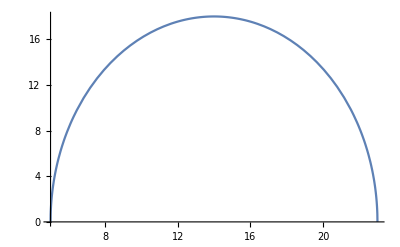

```mathematica
(*Transverse cross-section of ANUBIS modules*)
RANUBIS=9;
zToDecVolANUBIS=5;
zFidANUBIS=18;
ΔxCrossANUBIStemp[z_,R_,zToDecVol_,zFid_]=2√(R^2-(z-zToDecVol-zFid/2)^2);
ΔxCrossANUBIS[z_]=ΔxCrossANUBIStemp[z,RANUBIS,zToDecVolANUBIS,zFidANUBIS];
ΔyCrossANUBIS=18;
Plot[ΔxCrossANUBIS[z],{z,5,23}]
```

#### Geometry

```mathematica
explistanub={"ANUBIS-shaft-volume-1","ANUBIS-shaft-volume-2","ANUBIS-shaft-volume-3"};
(*Distance to the fiducial volume along the beamline axis. MapThread[(list1[#]=#2)&,{listexp,listvals}] equates the elements list1 with keys from listexp to the corresponding elements of the list listvals*)
MapThread[(zToDecayVolumeExperiment[#1]=#2)&,{explistanub,{4.5,4.5,4.5}}];
(*Detector has the axis along which its components are placed. The option below defines the orientation of the final plane transverse to this axis relative to the beamline*)
(*Transverse if the plane is tranverse (SHiP, FACET etc), and Parallel if it is parallel (ANUBIS-shaft-volume-1, ANUBIS*)
MapThread[(DetectorPlaneOrientationExperiment[#1]=#2)&,{explistanub,Table["Parallel",Length[explistanub]]}];
(*Facility hosting the experiment: SPS, Fermilab, LHC, FCC-hh*)
MapThread[(FacilityExperiment[#1]=#2)&,{explistanub,Table["LHC",Length[explistanub]]}];
(*Geometry of the experiment: box, cylinder, annular cylinder*)
MapThread[(GeometryExperiment[#1]=#2)&,{explistanub,Table["Cylinder",Length[explistanub]]}];
(*Transverse dimensions of the decay volume assuming box geometry, or cylindrical geometry if the detector plane is parallel to the beamline (ANUBIS). Otherwise set to zero*)
MapThread[(dxDecayVolumeExperiment[z_,#1]=#2)&,{explistanub,Table[ΔxCrossANUBIS[z],Length[explistanub]]}];
MapThread[(dyDecayVolumeExperiment[z_,#1]=#2)&,{explistanub,{19.5,18.7,18.6}}];
(*Decay volume length along the beamline axis*)
MapThread[(dzDecayVolumeExperiment[#1]=#2)&,{explistanub,Table[18,Length[explistanub]]}];
(*Distance from the beamline to the decay volume center and detector along the x,y axes*)
MapThread[(xToDecayVolumeCenterExperiment[z_,#1]=#2)&,{explistanub,Table[0,Length[explistanub]]}];
MapThread[(yToDecayVolumeCenterExperiment[z_,#1]=#2)&,{explistanub,{23+19.5/2.,42.6+18.7/2.,61.4+18.6/2.}}];
(*Inner and outer radii of the decay volume. Applicable if the decay volume has cylindrical geometry*)
Do[RinnerDecayVolumeExperiment[exp,z_]=0,{exp,explistanub}];
Do[RouterDecayVolumeExperiment[exp,z_]=9,{exp,explistanub}];
(*z-coordinate of the center of the decay volume*)
Do[zToDecayVolumeCenterExperiment[exp]=zToDecayVolumeExperiment[exp]+dzDecayVolumeExperiment[exp]/2,{exp,explistanub}];
(*Maximal long. displacement of the decay volume*)
Do[zMaxDecayVolumeExperiment[exp]=zToDecayVolumeExperiment[exp]+dzDecayVolumeExperiment[exp],{exp,explistanub}]
(*Whether the decay volume serves as detector (True or False)*)
Do[DecayVolumeAsDetectorExperiment[exp]="False",{exp,explistanub}]
(*Transverse dimensions of the detector assuming box geometry*)
MapThread[(dxDetectorExperiment[#1,z_]=#2)&,{explistanub,Table[0,Length[explistanub]]}];
MapThread[(dyDetectorExperiment[#1,z_]=#2)&,{explistanub,Table[0.1,Length[explistanub]]}];
(*Length of the detector in z plane*)
MapThread[(dzDetectorExperiment[#1]=#2)&,{explistanub,Table[0,Length[explistanub]]}];
(*Coordinates of the center of the detector*)
Do[xToDetectorCenterExperiment[exp]=0,{exp,explistanub}];
Do[yToDetectorCenterExperiment[exp]=yToDecayVolumeCenterExperiment[z,exp]+dyDecayVolumeExperiment[z,exp]/2+dyDetectorExperiment[exp,z]/2,{exp,explistanub}];
Do[zToDetectorCenterExperiment[exp]=If[DetectorPlaneOrientationExperiment[exp]=="Transverse",zMaxDecayVolumeExperiment[exp]+dzDetectorExperiment[exp]/2,zMaxDecayVolumeExperiment[exp]-dzDecayVolumeExperiment[exp]/2],{exp,explistanub}];
(*Inner and outer radii of the detector*)
Do[RinnerDetectorExperiment[exp,z_]=0,{exp,explistanub}];
Do[RouterDetectorExperiment[exp,z_]=9,{exp,explistanub}];
(*Length of the detector along the detector axis*)
Do[dxLongDetectorExperiment[exp]=If[DetectorPlaneOrientationExperiment[exp]=="Transverse",dzDetectorExperiment[exp],dyDetectorExperiment[exp,z]],{exp,explistanub}];
(*The maximal coordinate of the end of the detector plane (along the detector axis) used to calculate the decay acceptance. May be either the z coordinate or the y coordinate (if the final detector plane is oriented parallel to the beamline)*)
Do[xLongMaxDetectorExperiment[exp]=If[DetectorPlaneOrientationExperiment[exp]=="Transverse",zMaxDecayVolumeExperiment[exp]+dxLongDetectorExperiment[exp],yToDetectorCenterExperiment[exp]+dyDetectorExperiment[exp,z]/2],{exp,explistanub}];
(*Position of the final plane for the decay products along the detector axis*)
Do[xLongDecayProductFinalPlaneExperiment[exp]=xLongMaxDetectorExperiment[exp],{exp,explistanub}]
(*Whether the experiment has dipole magnet in the detector (True, False)*)
MapThread[(DipoleMagnetOptionExperiment[#1]=#2)&,{explistanub,Table["False",Length[explistanub]]}];
(*Longitudinal positions of the dipole magnet of the detector*)
MapThread[(zMagnetMinExperiment[#1]=#2)&,{explistanub,Table[0,Length[explistanub]]}];
MapThread[(zMagnetMaxExperiment[#1]=#2)&,{explistanub,Table[0,Length[explistanub]]}];
(*Mean magnetic field of the dipole magnet*)
MapThread[(MagneticFieldExperiment[#1]=#2)&,{explistanub,Table[0,Length[explistanub]]}];
(*ECAL option (True,False)*)
Do[ECALoptionExperiment[exp]="False",{exp,explistanub}];
(*Position of the beginning of the ECAL*)
MapThread[(zECALminExperiment[#1]=#2)&,{explistanub,Table[0,Length[explistanub]]}];
(*The final detector plane needed to reconstruct muons. Depeding on the experiment, it is approximated by be end of the trackers or the muon system*)
MapThread[(xLongMuonPlaneExperiment[#1]=#2)&,{explistanub,Table[xLongMaxDetectorExperiment[exp],{exp,explistanub}]}];
(*The final detector plane needed to reconstruct other particles. Depeding on the experiment, it is approximated by the end of the trackers or the calorimeter system*)
MapThread[(xLongNonMuonPlaneExperiment[#1]=#2)&,{explistanub,Table[xLongMaxDetectorExperiment[exp],{exp,explistanub}]}];
(*List of detectable particles. If ECAL is absent, it is assumed by default that photons and Subscript[K^0, L] cannot be detected*)
MapThread[(DetectablePDGsExperiment[#1]=#2)&,{explistanub,Table[Select[detectablepdgs,MemberQ[{22.,130.,2112.,-2112.},#]==False&],Length[explistanub]]}];
```

#### Cross-sections

```mathematica
MapThread[(NPOTexperiment[#1]=#2)&,{explistanub,Table[LLHChighLumi*σppInpbFacility["LHC"],Length[explistanub]]}];
MapThread[(AtargetExperiment[#1]=#2)&,{explistanub,Table[1.,Length[explistanub]]}];
(*Cascade enhancement of the production relative to the production in pure pp collisions. Relevant for fixed target experiments*)
(*For all experiments located at SPS, the cascade anubtors is taken from http://cds.cern.ch/record/2115534/files/SHiP-NOTE-2015-009.pdf?version=1*)
MapThread[(CascadeFactorbb[#1]=#2)&,{explistanub,Table[1.,Length[explistanub]]}];
(*Fraction of produced bb per PoT at the given experiment*)
Do[PppTobbExperiment[exp]=(σppTobbInpbFacility[FacilityExperiment[exp]]/σppInpbFacility[FacilityExperiment[exp]])AtargetExperiment[exp]^0.29*CascadeFactorbb[exp],{exp,explistanub}]
MapThread[(CascadeFactorcc[#1]=#2)&,{explistanub,Table[1.,Length[explistanub]]}];
(*Fraction of produced cc per PoT at the given experiment*)
Do[PppToccExperiment[exp]=(σppToccInpbFacility[FacilityExperiment[exp]]/σppInpbFacility[FacilityExperiment[exp]])AtargetExperiment[exp]^0.29*CascadeFactorcc[exp],{exp,explistanub}]
(*Fraction of produced h per PoT at the given experiment*)
Do[PppTohExperiment[exp]=(σppTohInpbFacility[FacilityExperiment[exp]]/σppInpbFacility[FacilityExperiment[exp]])AtargetExperiment[exp]^0.29,{exp,explistanub}];
(*Fraction of produced W per PoT at the given experiment*)
Do[PppToWExperiment[exp]=(σppToWInpbFacility[FacilityExperiment[exp]]/σppInpbFacility[FacilityExperiment[exp]])AtargetExperiment[exp]^0.29,{exp,explistanub}];
(*Fraction of produced π^0 per PoT at the given experiment*)
Do[PppToπ0exp[exp]=PppToπ0Facility[FacilityExperiment[exp]],{exp,explistanub}];
(*Fraction of produced η per PoT at the given experiment*)
Do[PppToηexp[exp]=PppToηFacility[FacilityExperiment[exp]],{exp,explistanub}];
(*Fraction of produced η' per PoT at the given experiment*)
Do[PppToηprexp[exp]=PppToηprFacility[FacilityExperiment[exp]],{exp,explistanub}];
(*Fraction of produced ρ^0 per PoT at the given experiment*)
Do[PppToρ0exp[exp]=PppToρ0Facility[FacilityExperiment[exp]],{exp,explistanub}];
(*Fraction of produced ω per PoT at the given experiment*)
Do[PppToωexp[exp]=PppToωFacility[FacilityExperiment[exp]],{exp,explistanub}];
Do[PppToJpsiexp[exp]=PppToJpsiFacility[FacilityExperiment[exp]] AtargetExperiment[exp]^0.29,{exp,explistanub}];
(*Fraction of produced Υ(1s) per PoT at the given experiment*)
Do[PppToUpsilonexp[exp]=PppToUpsilonFacility[FacilityExperiment[exp]] AtargetExperiment[exp]^0.29,{exp,explistanub}];
(*Fraction of produced ϕ at the given experiment*)
Do[PppToPhiexp[exp]=PppToPhiFacility[FacilityExperiment[exp]],{exp,explistanub}];
(*Overall table with cross-sections used for exporting*)
Do[TableNumbersParticlesExperiment[exp]={{"Facility","Npot","Atarget","PPi0","PEta","PEtapr","PRho0","POmega","Pc","Pb","PW","Ph","PJpsi","PUpsilon","PPhi"},{FacilityExperiment[exp],NPOTexperiment[exp],AtargetExperiment[exp],PppToπ0exp[exp],PppToηexp[exp],PppToηprexp[exp],PppToρ0exp[exp],PppToωexp[exp],2PppToccExperiment[exp],2PppTobbExperiment[exp],PppToWExperiment[exp],PppTohExperiment[exp],PppToJpsiexp[exp],PppToUpsilonexp[exp],PppToPhiexp[exp]}}//N,{exp,explistanub}]
```

#### Conditions for the LLP to decay inside the decay volume and for the products to point to the end of the detector

```mathematica
Do[
IfLLPinsideDecVol[zLLP_,xLLP_,yLLP_,exp]=IfLLPinsideDecVolSimple[exp];
{IfLLPtoDet[x1LLPproj_,x2LLPproj_,xLongProj_,exp],IfLLPnotToDet[x1LLPproj_,x2LLPproj_,xLongProj_,exp]}=IfParticlePointsToDetSimple[exp];
IfLLPdecVolToDet[zLLP_,xLLP_,yLLP_,x1LLPproj_,x2LLPproj_,xLongProj_,exp]=IfLLPinsideDecVol[zLLP,xLLP,yLLP,exp]*IfLLPtoDet[x1LLPproj,x2LLPproj,xLongProj,exp];
IfLLPdecVolNotToDet[zLLP_,xLLP_,yLLP_,x1LLPproj_,x2LLPproj_,xLongProj_,exp]=IfLLPinsideDecVol[zLLP,xLLP,yLLP,exp]*IfLLPnotToDet[x1LLPproj,x2LLPproj,xLongProj,exp];
DecayAcceptanceGeometry[coord1_,coord2_,xLongProj_,exp]=IfLLPtoDet[coord1,coord2,xLongProj,exp];
,{exp,explistanub}]
```

### HIKE/NA62

#### Geometry (mostly taken from ALPINIST)

```mathematica
(*HIKE-dump: the same design as NA62*)
explisthike={"HIKE-dump","NA62-dump"};
(*Distance to the fiducial volume along the beamline axis. MapThread[(list1[#]=#2)&,{listexp,listvals}] equates the elements list1 with keys from listexp to the corresponding elements of the list listvals*)
MapThread[(zToDecayVolumeExperiment[#1]=#2)&,{explisthike,{80.575,80.575}}];
(*Detector has the axis along which its components are placed. The option below defines the orientation of the final plane transverse to this axis relative to the beamline*)
(*Transverse if the plane is tranverse (SHiP, HIKE etc), and Parallel if it is parallel (MATHUSLA, ANUBIS*)
MapThread[(DetectorPlaneOrientationExperiment[#1]=#2)&,{explisthike,Table["Transverse",Length[explisthike]]}];
(*Facility hosting the experiment: SPS, Fermilab, LHC, FCC-hh*)
MapThread[(FacilityExperiment[#1]=#2)&,{explisthike,Table["SPS",Length[explisthike]]}];
(*Geometry of the experiment: box, cylinder, annular cylinder*)
MapThread[(GeometryExperiment[#1]=#2)&,{explisthike,Table["Annular cylinder",Length[explisthike]]}];
(*Transverse dimensions of the decay volume assuming box geometry, or cylindrical geometry if the detector plane is parallel to the beamline (ANUBIS). Otherwise set to zero*)
MapThread[(dxDecayVolumeExperiment[z_,#1]=#2)&,{explisthike,Table[0,Length[explisthike]]}];
MapThread[(dyDecayVolumeExperiment[z_,#1]=#2)&,{explisthike,Table[0,Length[explisthike]]}];
(*Decay volume length along the beamline axis*)
MapThread[(dzDecayVolumeExperiment[#1]=#2)&,{explisthike,{81.,81.}}];
(*Distance from the beamline to the decay volume center and detector along the x,y axes*)
MapThread[(xToDecayVolumeCenterExperiment[z_,#1]=#2)&,{explisthike,Table[0,Length[explisthike]]}];
MapThread[(yToDecayVolumeCenterExperiment[z_,#1]=#2)&,{explisthike,Table[0,Length[explisthike]]}];
(*Inner and outer radii of the decay volume. Applicable if the decay volume has cylindrical geometry*)
MapThread[(RinnerDecayVolumeExperiment[#1,z_]=#2)&,{explisthike,Table[0.08,Length[explisthike]]}];
MapThread[(RouterDecayVolumeExperiment[#1,z_]=#2)&,{explisthike,{1,1}}];
(*z-coordinate of the center of the decay volume*)
Do[zToDecayVolumeCenterExperiment[exp]=zToDecayVolumeExperiment[exp]+dzDecayVolumeExperiment[exp]/2,{exp,explisthike}];
(*Maximal long. displacement of the decay volume*)
Do[zMaxDecayVolumeExperiment[exp]=zToDecayVolumeExperiment[exp]+dzDecayVolumeExperiment[exp],{exp,explisthike}]
(*Whether the decay volume serves as detector (True or False)*)
Do[DecayVolumeAsDetectorExperiment[exp]="False",{exp,explisthike}]
(*Transverse dimensions of the detector assuming box geometry*)
MapThread[(dxDetectorExperiment[#1,z_]=#2)&,{explisthike,{0,0}}];
MapThread[(dyDetectorExperiment[#1,z_]=#2)&,{explisthike,{0,0}}];
(*Length of the detector in z plane*)
MapThread[(dzDetectorExperiment[#1]=#2)&,{explisthike,{63.85,63.85}}];
(*Coordinates of the center of the detector*)
Do[xToDetectorCenterExperiment[exp]=0,{exp,explisthike}];
Do[yToDetectorCenterExperiment[exp]=0,{exp,explisthike}];
Do[zToDetectorCenterExperiment[exp]=zMaxDecayVolumeExperiment[exp]+dzDetectorExperiment[exp]/2,{exp,explisthike}];
(*Inner and outer radii of the detector*)
MapThread[(RinnerDetectorExperiment[#1,z_]=#2)&,{explisthike,Table[0.08,Length[explisthike]]}];
MapThread[(RouterDetectorExperiment[#1,z_]=#2)&,{explisthike,{1.15,1.15}}];
(*Length of the detector along the detector axis*)
Do[dxLongDetectorExperiment[exp]=If[DetectorPlaneOrientationExperiment[exp]=="Transverse",dzDetectorExperiment[exp],dyDetectorExperiment[exp]],{exp,explisthike}];
(*The maximal coordinate of the end of the detector plane (along the detector axis) used to calculate the decay acceptance. May be either the z coordinate or the y coordinate (if the final detector plane is oriented parallel to the beamline)*)
Do[xLongMaxDetectorExperiment[exp]=If[DetectorPlaneOrientationExperiment[exp]=="Transverse",zMaxDecayVolumeExperiment[exp]+dxLongDetectorExperiment[exp],yToDetectorCenterExperiment[exp]+dyDetectorExperiment[exp]/2],{exp,explisthike}];
(*Position of the final plane for the decay products along the detector axis*)
Do[xLongDecayProductFinalPlaneExperiment[exp]=xLongMaxDetectorExperiment[exp],{exp,explisthike}]
(*Whether the experiment has dipole magnet in the detector (True, False)*)
MapThread[(DipoleMagnetOptionExperiment[#1]=#2)&,{explisthike,Table["False",Length[explisthike]]}];
(*Longitudinal positions of the dipole magnet of the detector*)
MapThread[(zMagnetMinExperiment[#1]=#2)&,{explisthike,Table[0,Length[explisthike]]}];
MapThread[(zMagnetMaxExperiment[#1]=#2)&,{explisthike,Table[0,Length[explisthike]]}];
(*Mean magnetic field of the dipole magnet*)
MapThread[(MagneticFieldExperiment[#1]=#2)&,{explisthike,Table[0,Length[explisthike]]}];
(*ECAL option (True,False)*)
Do[ECALoptionExperiment[exp]="True",{exp,explisthike}];
(*Position of the beginning of the ECAL*)
MapThread[(zECALminExperiment[#1]=#2)&,{explisthike,{241.495-23.07,241.495-23.07}}];
(*The final detector plane needed to reconstruct muons. Depeding on the experiment, it is approximated by be end of the trackers or the muon system*)
MapThread[(xLongMuonPlaneExperiment[#1]=#2)&,{explisthike,Table[xLongMaxDetectorExperiment[exp],{exp,explisthike}]}];
(*The final detector plane needed to reconstruct other particles. Depeding on the experiment, it is approximated by the end of the trackers or the calorimeter system*)
MapThread[(xLongNonMuonPlaneExperiment[#1]=#2)&,{explisthike,Table[xLongMaxDetectorExperiment[exp],{exp,explisthike}]}];
(*List of detectable particles. If ECAL is absent, it is assumed by default that photons and Subscript[K^0, L] cannot be detected*)
MapThread[(DetectablePDGsExperiment[#1]=#2)&,{explisthike,Table[detectablepdgs,Length[explisthike]]}];
```

#### Cross-sections

```mathematica
MapThread[(NPOTexperiment[#1]=#2)&,{explisthike,Table[5.*10^19,Length[explisthike]]}];
MapThread[(AtargetExperiment[#1]=#2)&,{explisthike,Table[64.,Length[explisthike]]}];
(*Cascade enhancement of the production relative to the production in pure pp collisions. Relevant for fixed target experiments*)
(*For all experiments located at SPS, the cascade hiketors is taken from http://cds.cern.ch/record/2115534/files/SHiP-NOTE-2015-009.pdf?version=1*)
MapThread[(CascadeFactorbb[#1]=#2)&,{explisthike,Table[1.7,Length[explisthike]]}];
(*Fraction of produced bb per PoT at the given experiment*)
Do[PppTobbExperiment[exp]=(σppTobbInpbFacility[FacilityExperiment[exp]]/σppInpbFacility[FacilityExperiment[exp]])AtargetExperiment[exp]^0.29*CascadeFactorbb[exp],{exp,explisthike}]
MapThread[(CascadeFactorcc[#1]=#2)&,{explisthike,Table[2.3,Length[explisthike]]}];
(*Fraction of produced cc per PoT at the given experiment*)
Do[PppToccExperiment[exp]=(σppToccInpbFacility[FacilityExperiment[exp]]/σppInpbFacility[FacilityExperiment[exp]])AtargetExperiment[exp]^0.29*CascadeFactorcc[exp],{exp,explisthike}]
(*Fraction of produced h per PoT at the given experiment*)
Do[PppTohExperiment[exp]=(σppTohInpbFacility[FacilityExperiment[exp]]/σppInpbFacility[FacilityExperiment[exp]])AtargetExperiment[exp]^0.29,{exp,explisthike}];
(*Fraction of produced W per PoT at the given experiment*)
Do[PppToWExperiment[exp]=(σppToWInpbFacility[FacilityExperiment[exp]]/σppInpbFacility[FacilityExperiment[exp]])AtargetExperiment[exp]^0.29,{exp,explisthike}];
(*Fraction of produced π^0 per PoT at the given experiment*)
Do[PppToπ0exp[exp]=PppToπ0Facility[FacilityExperiment[exp]],{exp,explisthike}];
(*Fraction of produced η per PoT at the given experiment*)
Do[PppToηexp[exp]=PppToηFacility[FacilityExperiment[exp]],{exp,explisthike}];
(*Fraction of produced η' per PoT at the given experiment*)
Do[PppToηprexp[exp]=PppToηprFacility[FacilityExperiment[exp]],{exp,explisthike}];
(*Fraction of produced ρ^0 per PoT at the given experiment*)
Do[PppToρ0exp[exp]=PppToρ0Facility[FacilityExperiment[exp]],{exp,explisthike}];
(*Fraction of produced ω per PoT at the given experiment*)
Do[PppToωexp[exp]=PppToωFacility[FacilityExperiment[exp]],{exp,explisthike}];
Do[PppToJpsiexp[exp]=PppToJpsiFacility[FacilityExperiment[exp]] AtargetExperiment[exp]^0.29,{exp,explisthike}];
(*Fraction of produced Υ(1s) per PoT at the given experiment*)
Do[PppToUpsilonexp[exp]=PppToUpsilonFacility[FacilityExperiment[exp]] AtargetExperiment[exp]^0.29,{exp,explisthike}];
(*Fraction of produced ϕ at the given experiment*)
Do[PppToPhiexp[exp]=PppToPhiFacility[FacilityExperiment[exp]],{exp,explisthike}];
(*Overall table with cross-sections used for exporting*)
Do[TableNumbersParticlesExperiment[exp]={{"Facility","Npot","Atarget","PPi0","PEta","PEtapr","PRho0","POmega","Pc","Pb","PW","Ph","PJpsi","PUpsilon","PPhi"},{FacilityExperiment[exp],NPOTexperiment[exp],AtargetExperiment[exp],PppToπ0exp[exp],PppToηexp[exp],PppToηprexp[exp],PppToρ0exp[exp],PppToωexp[exp],2PppToccExperiment[exp],2PppTobbExperiment[exp],PppToWExperiment[exp],PppTohExperiment[exp],PppToJpsiexp[exp],PppToUpsilonexp[exp],PppToPhiexp[exp]}}//N,{exp,explisthike}]
```

#### Conditions for the LLP to decay inside the decay volume and for the products to point to the end of the detector

```mathematica
Do[
IfLLPinsideDecVol[zLLP_,xLLP_,yLLP_,exp]=IfLLPinsideDecVolSimple[exp];
{IfLLPtoDet[x1LLPproj_,x2LLPproj_,xLongProj_,exp],IfLLPnotToDet[x1LLPproj_,x2LLPproj_,xLongProj_,exp]}=IfParticlePointsToDetSimple[exp];
IfLLPdecVolToDet[zLLP_,xLLP_,yLLP_,x1LLPproj_,x2LLPproj_,xLongProj_,exp]=IfLLPinsideDecVol[zLLP,xLLP,yLLP,exp]*IfLLPtoDet[x1LLPproj,x2LLPproj,xLongProj,exp];
IfLLPdecVolNotToDet[zLLP_,xLLP_,yLLP_,x1LLPproj_,x2LLPproj_,xLongProj_,exp]=IfLLPinsideDecVol[zLLP,xLLP,yLLP,exp]*IfLLPnotToDet[x1LLPproj,x2LLPproj,xLongProj,exp];
DecayAcceptanceGeometry[coord1_,coord2_,xLongProj_,exp]=IfLLPtoDet[coord1,coord2,xLongProj,exp];
,{exp,explisthike}]
```

### CODEX-b

#### Geometry

```mathematica
explistcodexb={"CODEX-b"};
(*Distance to the fiducial volume along the beamline axis. MapThread[(list1[#]=#2)&,{listexp,listvals}] equates the elements list1 with keys from listexp to the corresponding elements of the list listvals*)
MapThread[(zToDecayVolumeExperiment[#1]=#2)&,{explistcodexb,{5}}];
(*Detector has the axis along which its components are placed. The option below defines the orientation of the final plane transverse to this axis relative to the beamline*)
(*Transverse if the plane is tranverse (SHiP, FACET etc), and Parallel if it is parallel (Codex-b, ANUBIS*)
MapThread[(DetectorPlaneOrientationExperiment[#1]=#2)&,{explistcodexb,Table["Transverse",Length[explistcodexb]]}];
(*Facility hosting the experiment: SPS, Fermilab, LHC, FCC-hh*)
MapThread[(FacilityExperiment[#1]=#2)&,{explistcodexb,{"LHC"}}];
(*Geometry of the experiment: box, cylinder, annular cylinder*)
MapThread[(GeometryExperiment[#1]=#2)&,{explistcodexb,Table["Box",Length[explistcodexb]]}];
(*Transverse dimensions of the decay volume assuming box geometry, or cylindrical geometry if the detector plane is parallel to the beamline (ANUBIS). Otherwise set to zero*)
MapThread[(dxDecayVolumeExperiment[z_,#1]=#2)&,{explistcodexb,{10.}}];
MapThread[(dyDecayVolumeExperiment[z_,#1]=#2)&,{explistcodexb,{10.}}];
(*Decay volume length along the beamline axis*)
MapThread[(dzDecayVolumeExperiment[#1]=#2)&,{explistcodexb,{10.}}];
(*Distance from the beamline to the decay volume center and detector along the x,y axes*)
MapThread[(xToDecayVolumeCenterExperiment[z_,#1]=#2)&,{explistcodexb,{31.}}];
MapThread[(yToDecayVolumeCenterExperiment[z_,#1]=#2)&,{explistcodexb,{-2.}}];
(*Inner and outer radii of the decay volume. Applicable if the decay volume has cylindrical geometry*)
Do[RinnerDecayVolumeExperiment[exp,z_]=0,{exp,explistcodexb}];
Do[RouterDecayVolumeExperiment[exp,z_]=0,{exp,explistcodexb}];
(*z-coordinate of the center of the decay volume*)
Do[zToDecayVolumeCenterExperiment[exp]=zToDecayVolumeExperiment[exp]+dzDecayVolumeExperiment[exp]/2,{exp,explistcodexb}];
(*Maximal long. displacement of the decay volume*)
Do[zMaxDecayVolumeExperiment[exp]=zToDecayVolumeExperiment[exp]+dzDecayVolumeExperiment[exp],{exp,explistcodexb}]
(*Whether the decay volume serves as detector (True or False)*)
Do[DecayVolumeAsDetectorExperiment[exp]="True",{exp,explistcodexb}]
(*Transverse dimensions of the detector assuming box geometry*)
MapThread[(dxDetectorExperiment[#1,z_]=#2)&,{explistcodexb,Table[0,Length[explistcodexb]]}];
MapThread[(dyDetectorExperiment[#1,z_]=#2)&,{explistcodexb,Table[0,Length[explistcodexb]]}];
(*Length of the detector in z plane*)
MapThread[(dzDetectorExperiment[#1]=#2)&,{explistcodexb,Table[0,Length[explistcodexb]]}];
(*Coordinates of the center of the detector*)
Do[xToDetectorCenterExperiment[exp]=0,{exp,explistcodexb}];
Do[yToDetectorCenterExperiment[exp]=0,{exp,explistcodexb}];
Do[zToDetectorCenterExperiment[exp]=0,{exp,explistcodexb}];
(*Inner and outer radii of the detector*)
Do[RinnerDetectorExperiment[exp,z_]=0,{exp,explistcodexb}];
Do[RouterDetectorExperiment[exp,z_]=0,{exp,explistcodexb}];
(*Length of the detector along the detector axis*)
Do[dxLongDetectorExperiment[exp]=If[DetectorPlaneOrientationExperiment[exp]=="Transverse",dzDetectorExperiment[exp],dyDetectorExperiment[exp]],{exp,explistcodexb}];
(*The maximal coordinate of the end of the detector plane (along the detector axis) used to calculate the decay acceptance. May be either the z coordinate or the y coordinate (if the final detector plane is oriented parallel to the beamline)*)
Do[xLongMaxDetectorExperiment[exp]=If[DetectorPlaneOrientationExperiment[exp]=="Transverse",zMaxDecayVolumeExperiment[exp]+dxLongDetectorExperiment[exp],yToDetectorCenterExperiment[exp]+dyDetectorExperiment[exp]/2],{exp,explistcodexb}];
(*Position of the final plane for the decay products along the detector axis*)
Do[xLongDecayProductFinalPlaneExperiment[exp]=zMaxDecayVolumeExperiment[exp],{exp,explistcodexb}]
(*Whether the experiment has dipole magnet in the detector (True, False)*)
MapThread[(DipoleMagnetOptionExperiment[#1]=#2)&,{explistcodexb,Table["False",Length[explistcodexb]]}];
(*Longitudinal positions of the dipole magnet of the detector*)
MapThread[(zMagnetMinExperiment[#1]=#2)&,{explistcodexb,Table[0,Length[explistcodexb]]}];
MapThread[(zMagnetMaxExperiment[#1]=#2)&,{explistcodexb,Table[0,Length[explistcodexb]]}];
(*Mean magnetic field of the dipole magnet*)
MapThread[(MagneticFieldExperiment[#1]=#2)&,{explistcodexb,Table[0,Length[explistcodexb]]}];
(*ECAL option (True,False)*)
Do[ECALoptionExperiment[exp]="True",{exp,explistcodexb}];
(*Position of the beginning of the ECAL*)
MapThread[(zECALminExperiment[#1]=#2)&,{explistcodexb,Table[0,Length[explistcodexb]]}];
(*The final detector plane needed to reconstruct muons. Depeding on the experiment, it is approximated by be end of the trackers or the muon system*)
MapThread[(xLongMuonPlaneExperiment[#1]=#2)&,{explistcodexb,Table[0,{exp,explistcodexb}]}];
(*The final detector plane needed to reconstruct other particles. Depeding on the experiment, it is approximated by the end of the trackers or the calorimeter system*)
MapThread[(xLongNonMuonPlaneExperiment[#1]=#2)&,{explistcodexb,Table[0,{exp,explistcodexb}]}];
(*List of detectable particles. If ECAL is absent, it is assumed by default that photons and Subscript[K^0, L] cannot be detected*)
MapThread[(DetectablePDGsExperiment[#1]=#2)&,{explistcodexb,Table[detectablepdgs,Length[explistcodexb]]}];
```

#### Cross-sections

```mathematica
(*0.1 stays for 10 times lower luminosity of LHCb in high lumi phase compared to ATLAS/CMS*)
MapThread[(NPOTexperiment[#1]=#2)&,{explistcodexb,Table[0.1*LLHChighLumi*σppInpbFacility["LHC"],Length[explistcodexb]]}];
MapThread[(AtargetExperiment[#1]=#2)&,{explistcodexb,Table[1.,Length[explistcodexb]]}];
(*Cascade enhancement of the production relative to the production in pure pp collisions. Relevant for fixed target experiments*)
(*For all experiments located at SPS, the cascade codexbtors is taken from http://cds.cern.ch/record/2115534/files/SHiP-NOTE-2015-009.pdf?version=1*)
MapThread[(CascadeFactorbb[#1]=#2)&,{explistcodexb,Table[1.,Length[explistcodexb]]}];
(*Fraction of produced bb per PoT at the given experiment*)
Do[PppTobbExperiment[exp]=(σppTobbInpbFacility[FacilityExperiment[exp]]/σppInpbFacility[FacilityExperiment[exp]])AtargetExperiment[exp]^0.29*CascadeFactorbb[exp],{exp,explistcodexb}]
MapThread[(CascadeFactorcc[#1]=#2)&,{explistcodexb,Table[1.,Length[explistcodexb]]}];
(*Fraction of produced cc per PoT at the given experiment*)
Do[PppToccExperiment[exp]=(σppToccInpbFacility[FacilityExperiment[exp]]/σppInpbFacility[FacilityExperiment[exp]])AtargetExperiment[exp]^0.29*CascadeFactorcc[exp],{exp,explistcodexb}]
(*Fraction of produced h per PoT at the given experiment*)
Do[PppTohExperiment[exp]=(σppTohInpbFacility[FacilityExperiment[exp]]/σppInpbFacility[FacilityExperiment[exp]])AtargetExperiment[exp]^0.29,{exp,explistcodexb}];
(*Fraction of produced W per PoT at the given experiment*)
Do[PppToWExperiment[exp]=(σppToWInpbFacility[FacilityExperiment[exp]]/σppInpbFacility[FacilityExperiment[exp]])AtargetExperiment[exp]^0.29,{exp,explistcodexb}];
(*Fraction of produced π^0 per PoT at the given experiment*)
Do[PppToπ0exp[exp]=PppToπ0Facility[FacilityExperiment[exp]],{exp,explistcodexb}];
(*Fraction of produced η per PoT at the given experiment*)
Do[PppToηexp[exp]=PppToηFacility[FacilityExperiment[exp]],{exp,explistcodexb}];
(*Fraction of produced η' per PoT at the given experiment*)
Do[PppToηprexp[exp]=PppToηprFacility[FacilityExperiment[exp]],{exp,explistcodexb}];
(*Fraction of produced ρ^0 per PoT at the given experiment*)
Do[PppToρ0exp[exp]=PppToρ0Facility[FacilityExperiment[exp]],{exp,explistcodexb}];
(*Fraction of produced ω per PoT at the given experiment*)
Do[PppToωexp[exp]=PppToωFacility[FacilityExperiment[exp]],{exp,explistcodexb}];
Do[PppToJpsiexp[exp]=PppToJpsiFacility[FacilityExperiment[exp]] AtargetExperiment[exp]^0.29,{exp,explistcodexb}];
(*Fraction of produced Υ(1s) per PoT at the given experiment*)
Do[PppToUpsilonexp[exp]=PppToUpsilonFacility[FacilityExperiment[exp]] AtargetExperiment[exp]^0.29,{exp,explistcodexb}];
(*Fraction of produced ϕ at the given experiment*)
Do[PppToPhiexp[exp]=PppToPhiFacility[FacilityExperiment[exp]],{exp,explistcodexb}];
(*Overall table with cross-sections used for exporting*)
Do[TableNumbersParticlesExperiment[exp]={{"Facility","Npot","Atarget","PPi0","PEta","PEtapr","PRho0","POmega","Pc","Pb","PW","Ph","PJpsi","PUpsilon","PPhi"},{FacilityExperiment[exp],NPOTexperiment[exp],AtargetExperiment[exp],PppToπ0exp[exp],PppToηexp[exp],PppToηprexp[exp],PppToρ0exp[exp],PppToωexp[exp],2PppToccExperiment[exp],2PppTobbExperiment[exp],PppToWExperiment[exp],PppTohExperiment[exp],PppToJpsiexp[exp],PppToUpsilonexp[exp],PppToPhiexp[exp]}}//N,{exp,explistcodexb}]
```

#### Conditions for the LLP to decay inside the decay volume and for the products to point to the end of the detector

```mathematica
Do[
IfLLPinsideDecVol[zLLP_,xLLP_,yLLP_,exp]=IfLLPinsideDecVolSimple[exp];
{IfLLPtoDet[x1LLPproj_,x2LLPproj_,xLongProj_,exp],IfLLPnotToDet[x1LLPproj_,x2LLPproj_,xLongProj_,exp]}=IfParticlePointsToDetSimple[exp];
IfLLPdecVolToDet[zLLP_,xLLP_,yLLP_,x1LLPproj_,x2LLPproj_,xLongProj_,exp]=IfLLPinsideDecVol[zLLP,xLLP,yLLP,exp]*IfLLPtoDet[x1LLPproj,x2LLPproj,xLongProj,exp];
IfLLPdecVolNotToDet[zLLP_,xLLP_,yLLP_,x1LLPproj_,x2LLPproj_,xLongProj_,exp]=IfLLPinsideDecVol[zLLP,xLLP,yLLP,exp]*IfLLPnotToDet[x1LLPproj,x2LLPproj,xLongProj,exp];
DecayAcceptanceGeometry[coord1_,coord2_,xLongProj_,exp]=IfLLPtoDet[coord1,coord2,xLongProj,exp];
,{exp,explistcodexb}]
```

### FOREHUNT@FCC-hh (2306.11803 but with added detector and a hole accounting for beamline)

#### Geometry

```mathematica
explistforehunt={"FOREHUNT-A","FOREHUNT-D","FOREHUNT-F"};
(*Distance to the fiducial volume along the beamline axis. MapThread[(list1[#]=#2)&,{listexp,listvals}] equates the elements list1 with keys from listexp to the corresponding elements of the list listvals*)
MapThread[(zToDecayVolumeExperiment[#1]=#2)&,{explistforehunt,{50,75,100.}}];
(*Detector has the axis along which its components are placed. The option below defines the orientation of the final plane transverse to this axis relative to the beamline*)
(*Transverse if the plane is tranverse (SHiP, FASER etc), and Parallel if it is parallel (MATHUSLA, ANUBIS*)
MapThread[(DetectorPlaneOrientationExperiment[#1]=#2)&,{explistforehunt,Table["Transverse",Length[explistforehunt]]}];
(*Facility hosting the experiment: SPS, Fermilab, LHC, FCC-hh*)
MapThread[(FacilityExperiment[#1]=#2)&,{explistforehunt,Table["FCC-hh",Length[explistforehunt]]}];
(*Geometry of the experiment: box, cylinder, annular cylinder*)
MapThread[(GeometryExperiment[#1]=#2)&,{explistforehunt,Table["Annular cylinder",Length[explistforehunt]]}];
(*Transverse dimensions of the decay volume assuming box geometry, or cylindrical geometry if the detector plane is parallel to the beamline (ANUBIS). Otherwise set to zero*)
MapThread[(dxDecayVolumeExperiment[z_,#1]=#2)&,{explistforehunt,{0,0,0}}];
MapThread[(dyDecayVolumeExperiment[z_,#1]=#2)&,{explistforehunt,{0,0,0}}];
(*Decay volume length along the beamline axis*)
MapThread[(dzDecayVolumeExperiment[#1]=#2)&,{explistforehunt,{10,20,50.}}];
(*Distance from the beamline to the decay volume center and detector along the x,y axes*)
MapThread[(xToDecayVolumeCenterExperiment[z_,#1]=#2)&,{explistforehunt,{0,0,0}}];
MapThread[(yToDecayVolumeCenterExperiment[z_,#1]=#2)&,{explistforehunt,{0,0,0}}];
(*Inner and outer radii of the decay volume. Applicable if the decay volume has cylindrical geometry*)
MapThread[(RinnerDecayVolumeExperiment[#1,z_]=#2)&,{explistforehunt,{0.2,0.2,0.2}}];
MapThread[(RouterDecayVolumeExperiment[#1,z_]=#2)&,{explistforehunt,{1.,2.,5.}}];
(*z-coordinate of the center of the decay volume*)
Do[zToDecayVolumeCenterExperiment[exp]=zToDecayVolumeExperiment[exp]+dzDecayVolumeExperiment[exp]/2,{exp,explistforehunt}];
(*Maximal long. displacement of the decay volume*)
Do[zMaxDecayVolumeExperiment[exp]=zToDecayVolumeExperiment[exp]+dzDecayVolumeExperiment[exp],{exp,explistforehunt}]
(*Whether the decay volume serves as detector (True or False)*)
Do[DecayVolumeAsDetectorExperiment[exp]="False",{exp,explistforehunt}]
(*Transverse dimensions of the detector assuming box geometry*)
MapThread[(dxDetectorExperiment[#1,z_]=#2)&,{explistforehunt,{0.1,1.,1.}}];
MapThread[(dyDetectorExperiment[#1,z_]=#2)&,{explistforehunt,{0.1,1.,1.}}];
(*Length of the detector in z plane*)
MapThread[(dzDetectorExperiment[#1]=#2)&,{explistforehunt,{9,9,9.}}];
(*Coordinates of the center of the detector*)
Do[xToDetectorCenterExperiment[exp]=0,{exp,explistforehunt}];
Do[yToDetectorCenterExperiment[exp]=0,{exp,explistforehunt}];
Do[zToDetectorCenterExperiment[exp]=zMaxDecayVolumeExperiment[exp]+dzDetectorExperiment[exp]/2,{exp,explistforehunt}];
(*Inner and outer radii of the detector*)
MapThread[(RinnerDetectorExperiment[#1,z_]=#2)&,{explistforehunt,{0.2,0.2,0.2}}];
MapThread[(RouterDetectorExperiment[#1,z_]=#2)&,{explistforehunt,{1.,2.,5.}}];
(*Length of the detector along the detector axis*)
Do[dxLongDetectorExperiment[exp]=If[DetectorPlaneOrientationExperiment[exp]=="Transverse",dzDetectorExperiment[exp],dyDetectorExperiment[exp]],{exp,explistforehunt}];
(*The maximal coordinate of the end of the detector plane (along the detector axis) used to calculate the decay acceptance. May be either the z coordinate or the y coordinate (if the final detector plane is oriented parallel to the beamline)*)
Do[xLongMaxDetectorExperiment[exp]=If[DetectorPlaneOrientationExperiment[exp]=="Transverse",zMaxDecayVolumeExperiment[exp]+dxLongDetectorExperiment[exp],yToDetectorCenterExperiment[exp]+dyDetectorExperiment[exp]/2],{exp,explistforehunt}];
(*Position of the final plane for the decay products along the detector axis*)
Do[xLongDecayProductFinalPlaneExperiment[exp]=xLongMaxDetectorExperiment[exp],{exp,explistforehunt}]
(*Whether the experiment has dipole magnet in the detector (True, False)*)
MapThread[(DipoleMagnetOptionExperiment[#1]=#2)&,{explistforehunt,{"False","False","False"}}];
(*Longitudinal positions of the dipole magnet of the detector*)
MapThread[(zMagnetMinExperiment[#1]=#2)&,{explistforehunt,{0,0,0}}];
MapThread[(zMagnetMaxExperiment[#1]=#2)&,{explistforehunt,{0,0,0}}];
(*Mean magnetic field of the dipole magnet*)
MapThread[(MagneticFieldExperiment[#1]=#2)&,{explistforehunt,{0,0,0}}];
(*ECAL option (True,False)*)
Do[ECALoptionExperiment[exp]="True",{exp,explistforehunt}];
(*Position of the beginning of the ECAL*)
MapThread[(zECALminExperiment[#1]=#2)&,{explistforehunt,{zMaxDecayVolumeExperiment["FOREHUNT-A"]+3,zMaxDecayVolumeExperiment["FOREHUNT-D"]+3,zMaxDecayVolumeExperiment["FOREHUNT-F"]+3}}];
(*The final detector plane needed to reconstruct muons. Depeding on the experiment, it is approximated by be end of the trackers or the muon system*)
MapThread[(xLongMuonPlaneExperiment[#1]=#2)&,{explistforehunt,Table[xLongMaxDetectorExperiment[exp],{exp,explistforehunt}]}];
(*The final detector plane needed to reconstruct other particles. Depeding on the experiment, it is approximated by the end of the trackers or the calorimeter system*)
MapThread[(xLongNonMuonPlaneExperiment[#1]=#2)&,{explistforehunt,Table[zECALminExperiment[exp]+2,{exp,explistforehunt}]}];
(*List of detectable particles. If ECAL is absent, it is assumed by default that photons and Subscript[K^0, L] cannot be detected*)
MapThread[(DetectablePDGsExperiment[#1]=#2)&,{explistforehunt,Table[detectablepdgs,Length[explistforehunt]]}];
```

#### Cross-sections

```mathematica
MapThread[(NPOTexperiment[#1]=#2)&,{explistforehunt,Table[LFCChh*σppInpbFacility["FCC-hh"],Length[explistforehunt]]}];
MapThread[(AtargetExperiment[#1]=#2)&,{explistforehunt,Table[1.,Length[explistforehunt]]}];
(*Cascade enhancement of the production relative to the production in pure pp collisions. Relevant for fixed target experiments*)
(*For all experiments located at SPS, the cascade fastors is taken from http://cds.cern.ch/record/2115534/files/SHiP-NOTE-2015-009.pdf?version=1*)
MapThread[(CascadeFactorbb[#1]=#2)&,{explistforehunt,Table[1.,Length[explistforehunt]]}];
(*Fraction of produced bb per PoT at the given experiment*)
Do[PppTobbExperiment[exp]=(σppTobbInpbFacility[FacilityExperiment[exp]]/σppInpbFacility[FacilityExperiment[exp]])AtargetExperiment[exp]^0.29*CascadeFactorbb[exp],{exp,explistforehunt}]
MapThread[(CascadeFactorcc[#1]=#2)&,{explistforehunt,Table[1.,Length[explistforehunt]]}];
(*Fraction of produced cc per PoT at the given experiment*)
Do[PppToccExperiment[exp]=(σppToccInpbFacility[FacilityExperiment[exp]]/σppInpbFacility[FacilityExperiment[exp]])AtargetExperiment[exp]^0.29*CascadeFactorcc[exp],{exp,explistforehunt}]
(*Fraction of produced h per PoT at the given experiment*)
Do[PppTohExperiment[exp]=(σppTohInpbFacility[FacilityExperiment[exp]]/σppInpbFacility[FacilityExperiment[exp]])AtargetExperiment[exp]^0.29,{exp,explistforehunt}];
(*Fraction of produced W per PoT at the given experiment*)
Do[PppToWExperiment[exp]=(σppToWInpbFacility[FacilityExperiment[exp]]/σppInpbFacility[FacilityExperiment[exp]])AtargetExperiment[exp]^0.29,{exp,explistforehunt}];
(*Fraction of produced π^0 per PoT at the given experiment*)
Do[PppToπ0exp[exp]=PppToπ0Facility[FacilityExperiment[exp]],{exp,explistforehunt}];
(*Fraction of produced η per PoT at the given experiment*)
Do[PppToηexp[exp]=PppToηFacility[FacilityExperiment[exp]],{exp,explistforehunt}];
(*Fraction of produced η' per PoT at the given experiment*)
Do[PppToηprexp[exp]=PppToηprFacility[FacilityExperiment[exp]],{exp,explistforehunt}];
(*Fraction of produced ρ^0 per PoT at the given experiment*)
Do[PppToρ0exp[exp]=PppToρ0Facility[FacilityExperiment[exp]],{exp,explistforehunt}];
(*Fraction of produced ω per PoT at the given experiment*)
Do[PppToωexp[exp]=PppToωFacility[FacilityExperiment[exp]],{exp,explistforehunt}];
Do[PppToJpsiexp[exp]=PppToJpsiFacility[FacilityExperiment[exp]] AtargetExperiment[exp]^0.29,{exp,explistforehunt}];
(*Fraction of produced Υ(1s) per PoT at the given experiment*)
Do[PppToUpsilonexp[exp]=PppToUpsilonFacility[FacilityExperiment[exp]] AtargetExperiment[exp]^0.29,{exp,explistforehunt}];
(*Fraction of produced ϕ at the given experiment*)
Do[PppToPhiexp[exp]=PppToPhiFacility[FacilityExperiment[exp]],{exp,explistforehunt}];
(*Overall table with cross-sections used for exporting*)
Do[TableNumbersParticlesExperiment[exp]={{"Facility","Npot","Atarget","PPi0","PEta","PEtapr","PRho0","POmega","Pc","Pb","PW","Ph","PJpsi","PUpsilon","PPhi"},{FacilityExperiment[exp],NPOTexperiment[exp],AtargetExperiment[exp],PppToπ0exp[exp],PppToηexp[exp],PppToηprexp[exp],PppToρ0exp[exp],PppToωexp[exp],2PppToccExperiment[exp],2PppTobbExperiment[exp],PppToWExperiment[exp],PppTohExperiment[exp],PppToJpsiexp[exp],PppToUpsilonexp[exp],PppToPhiexp[exp]}}//N,{exp,explistforehunt}]
```

#### Conditions for the LLP to decay inside the decay volume and for the products to point to the end of the detector

```mathematica
Do[
IfLLPinsideDecVol[zLLP_,xLLP_,yLLP_,exp]=IfLLPinsideDecVolSimple[exp];
{IfLLPtoDet[x1LLPproj_,x2LLPproj_,xLongProj_,exp],IfLLPnotToDet[x1LLPproj_,x2LLPproj_,xLongProj_,exp]}=IfParticlePointsToDetSimple[exp];
IfLLPdecVolToDet[zLLP_,xLLP_,yLLP_,x1LLPproj_,x2LLPproj_,xLongProj_,exp]=IfLLPinsideDecVol[zLLP,xLLP,yLLP,exp]*IfLLPtoDet[x1LLPproj,x2LLPproj,xLongProj,exp];
IfLLPdecVolNotToDet[zLLP_,xLLP_,yLLP_,x1LLPproj_,x2LLPproj_,xLongProj_,exp]=IfLLPinsideDecVol[zLLP,xLLP,yLLP,exp]*IfLLPnotToDet[x1LLPproj,x2LLPproj,xLongProj,exp];
DecayAcceptanceGeometry[coord1_,coord2_,xLongProj_,exp]=IfLLPtoDet[coord1,coord2,xLongProj,exp];
,{exp,explistforehunt}]
```

### CHARM/BEBC

#### Geometry

```mathematica
(*CHARM-approx - just a box with dimensions 3*3*35 m^3. CHARM - the accurate implementation*)
explistcharm={"CHARM-lepton","CHARM-photon","BEBC"};
(*Distance to the fiducial volume along the beamline axis. MapThread[(list1[#]=#2)&,{listexp,listvals}] equates the elements list1 with keys from listexp to the corresponding elements of the list listvals*)
MapThread[(zToDecayVolumeExperiment[#1]=#2)&,{explistcharm,{480,480,404}}];
(*Detector has the axis along which its components are placed. The option below defines the orientation of the final plane transverse to this axis relative to the beamline*)
(*Transverse if the plane is tranverse (SHiP, FACET etc), and Parallel if it is parallel (MATHUSLA, ANUBIS*)
MapThread[(DetectorPlaneOrientationExperiment[#1]=#2)&,{explistcharm,Table["Transverse",Length[explistcharm]]}];
(*Facility hosting the experiment: SPS, Fermilab, LHC, FCC-hh*)
MapThread[(FacilityExperiment[#1]=#2)&,{explistcharm,Table["SPS",Length[explistcharm]]}];
(*Geometry of the experiment: box, cylinder, annular cylinder*)
MapThread[(GeometryExperiment[#1]=#2)&,{explistcharm,Table["Box",Length[explistcharm]]}];
(*Transverse dimensions of the decay volume assuming box geometry, or cylindrical geometry if the detector plane is parallel to the beamline (ANUBIS). Otherwise set to zero*)
MapThread[(dxDecayVolumeExperiment[z_,#1]=#2)&,{explistcharm,{3.,3.,3.6}}];
MapThread[(dyDecayVolumeExperiment[z_,#1]=#2)&,{explistcharm,{3,3.,2.5}}];
(*Decay volume length along the beamline axis*)
MapThread[(dzDecayVolumeExperiment[#1]=#2)&,{explistcharm,{35,35,1.85}}];
(*Distance from the beamline to the decay volume center and detector along the x,y axes*)
MapThread[(xToDecayVolumeCenterExperiment[z_,#1]=#2)&,{explistcharm,{5.,5.,0}}];
MapThread[(yToDecayVolumeCenterExperiment[z_,#1]=#2)&,{explistcharm,Table[0,Length[explistcharm]]}];
(*Inner and outer radii of the decay volume. Applicable if the decay volume has cylindrical geometry*)
Do[RinnerDecayVolumeExperiment[exp,z_]=0,{exp,explistcharm}];
Do[RouterDecayVolumeExperiment[exp,z_]=0,{exp,explistcharm}];
(*z-coordinate of the center of the decay volume*)
Do[zToDecayVolumeCenterExperiment[exp]=zToDecayVolumeExperiment[exp]+dzDecayVolumeExperiment[exp]/2,{exp,explistcharm}];
(*Maximal long. displacement of the decay volume*)
Do[zMaxDecayVolumeExperiment[exp]=zToDecayVolumeExperiment[exp]+dzDecayVolumeExperiment[exp],{exp,explistcharm}]
(*Whether the decay volume serves as detector (True or False)*)
MapThread[(DecayVolumeAsDetectorExperiment[#1]=#2)&,{explistcharm,{"False","False","True"}}];
(*Transverse dimensions of the detector assuming box geometry*)
MapThread[(dxDetectorExperiment[#1,z_]=#2)&,{explistcharm,{If[z<zMaxDecayVolumeExperiment["CHARM-lepton"]+5,4,3],If[z<zMaxDecayVolumeExperiment["CHARM-photon"]+5,4,3],0}}];
MapThread[(dyDetectorExperiment[#1,z_]=#2)&,{explistcharm,{If[z<zMaxDecayVolumeExperiment["CHARM-lepton"]+5,4,3],If[z<zMaxDecayVolumeExperiment["CHARM-photon"]+5,4,3],0}}];
(*Length of the detector in z plane*)
MapThread[(dzDetectorExperiment[#1]=#2)&,{explistcharm,{6.4,6.4,0}}];
(*Coordinates of the center of the detector*)
MapThread[(xToDetectorCenterExperiment[#1]=#2)&,{explistcharm,{5.,5.,0}}];
Do[yToDetectorCenterExperiment[exp]=0,{exp,explistcharm}];
Do[zToDetectorCenterExperiment[exp]=zMaxDecayVolumeExperiment[exp]+dzDetectorExperiment[exp]/2,{exp,explistcharm}];
(*Inner and outer radii of the detector*)
Do[RinnerDetectorExperiment[exp,z_]=0,{exp,explistcharm}];
Do[RouterDetectorExperiment[exp,z_]=0,{exp,explistcharm}];
(*Length of the detector along the detector axis. For the detector oriented parallel to the beamline, there is a formal z-dependence, but in practice there are no experiments with such dependence, so it is suppressed*)
Do[dxLongDetectorExperiment[exp]=If[DetectorPlaneOrientationExperiment[exp]=="Transverse",dzDetectorExperiment[exp],dyDetectorExperiment[exp,z]],{exp,explistcharm}];
(*The maximal coordinate of the end of the detector plane (along the detector axis) used to calculate the decay acceptance. May be either the z coordinate or the y coordinate (if the final detector plane is oriented parallel to the beamline)*)
Do[xLongMaxDetectorExperiment[exp]=If[DetectorPlaneOrientationExperiment[exp]=="Transverse",zMaxDecayVolumeExperiment[exp]+dxLongDetectorExperiment[exp],yToDetectorCenterExperiment[exp]+dyDetectorExperiment[exp,z]/2],{exp,explistcharm}];
(*Whether the experiment has dipole magnet in the detector (True, False)*)
MapThread[(DipoleMagnetOptionExperiment[#1]=#2)&,{explistcharm,{"False","False","False"}}];
(*Longitudinal positions of the dipole magnet of the detector*)
MapThread[(zMagnetMinExperiment[#1]=#2)&,{explistcharm,Table[0,Length[explistcharm]]}];
MapThread[(zMagnetMaxExperiment[#1]=#2)&,{explistcharm,Table[0,Length[explistcharm]]}];
(*Mean magnetic field of the dipole magnet*)
MapThread[(MagneticFieldExperiment[#1]=#2)&,{explistcharm,Table[0,Length[explistcharm]]}];
(*ECAL option (True,False)*)
MapThread[(ECALoptionExperiment[#1]=#2)&,{explistcharm,{"True","True","True"}}];
(*Position of the beginning of the ECAL*)
MapThread[(zECALminExperiment[#1]=#2)&,{explistcharm,{zMaxDecayVolumeExperiment["CHARM-lepton"]+5.,zMaxDecayVolumeExperiment["CHARM-lepton"]+5.,0.}}];
(*The final detector plane needed to reconstruct muons. Depeding on the experiment, it is approximated by be end of the trackers or the muon system*)
MapThread[(xLongMuonPlaneExperiment[#1]=#2)&,{explistcharm,{xLongMaxDetectorExperiment["CHARM-lepton"],xLongMaxDetectorExperiment["CHARM-lepton"],0.}}];
(*The final detector plane needed to reconstruct other particles. Depeding on the experiment, it is approximated by the end of the trackers or the calorimeter system*)
MapThread[(xLongNonMuonPlaneExperiment[#1]=#2)&,{explistcharm,{xLongMaxDetectorExperiment["CHARM-lepton"],xLongMaxDetectorExperiment["CHARM-lepton"],0.}}];
(*List of detectable particles. If ECAL is absent, it is assumed by default that photons and Subscript[K^0, L] cannot be detected*)
MapThread[(DetectablePDGsExperiment[#1]=#2)&,{explistcharm,Table[detectablepdgs,Length[explistcharm]]}];
```

#### Cross-sections

```mathematica
(*0.1 stays for 10 times lower luminosity of LHCb in high lumi phase compared to ATLAS/CMS*)
MapThread[(NPOTexperiment[#1]=#2)&,{explistcharm,{2.4*10^18,2.4*10^18,2.72*10^18}}];
MapThread[(AtargetExperiment[#1]=#2)&,{explistcharm,{64,64,64}}];
(*Cascade enhancement of the production relative to the production in pure pp collisions. Relevant for fixed target experiments*)
(*For all experiments located at SPS, the cascade charmtors is taken from http://cds.cern.ch/record/2115534/files/SHiP-NOTE-2015-009.pdf?version=1*)
MapThread[(CascadeFactorbb[#1]=#2)&,{explistcharm,Table[1.,Length[explistcharm]]}];
(*Fraction of produced bb per PoT at the given experiment*)
Do[PppTobbExperiment[exp]=(σppTobbInpbFacility[FacilityExperiment[exp]]/σppInpbFacility[FacilityExperiment[exp]])AtargetExperiment[exp]^0.29*CascadeFactorbb[exp],{exp,explistcharm}]
MapThread[(CascadeFactorcc[#1]=#2)&,{explistcharm,Table[1.,Length[explistcharm]]}];
(*Fraction of produced cc per PoT at the given experiment*)
Do[PppToccExperiment[exp]=(σppToccInpbFacility[FacilityExperiment[exp]]/σppInpbFacility[FacilityExperiment[exp]])AtargetExperiment[exp]^0.29*CascadeFactorcc[exp],{exp,explistcharm}]
(*Fraction of produced h per PoT at the given experiment*)
Do[PppTohExperiment[exp]=(σppTohInpbFacility[FacilityExperiment[exp]]/σppInpbFacility[FacilityExperiment[exp]])AtargetExperiment[exp]^0.29,{exp,explistcharm}];
(*Fraction of produced W per PoT at the given experiment*)
Do[PppToWExperiment[exp]=(σppToWInpbFacility[FacilityExperiment[exp]]/σppInpbFacility[FacilityExperiment[exp]])AtargetExperiment[exp]^0.29,{exp,explistcharm}];
(*Fraction of produced π^0 per PoT at the given experiment*)
Do[PppToπ0exp[exp]=PppToπ0Facility[FacilityExperiment[exp]],{exp,explistcharm}];
(*Fraction of produced η per PoT at the given experiment*)
Do[PppToηexp[exp]=PppToηFacility[FacilityExperiment[exp]],{exp,explistcharm}];
(*Fraction of produced η' per PoT at the given experiment*)
Do[PppToηprexp[exp]=PppToηprFacility[FacilityExperiment[exp]],{exp,explistcharm}];
(*Fraction of produced ρ^0 per PoT at the given experiment*)
Do[PppToρ0exp[exp]=PppToρ0Facility[FacilityExperiment[exp]],{exp,explistcharm}];
(*Fraction of produced ω per PoT at the given experiment*)
Do[PppToωexp[exp]=PppToωFacility[FacilityExperiment[exp]],{exp,explistcharm}];
Do[PppToJpsiexp[exp]=PppToJpsiFacility[FacilityExperiment[exp]] AtargetExperiment[exp]^0.29,{exp,explistcharm}];
(*Fraction of produced Υ(1s) per PoT at the given experiment*)
Do[PppToUpsilonexp[exp]=PppToUpsilonFacility[FacilityExperiment[exp]] AtargetExperiment[exp]^0.29,{exp,explistcharm}];
(*Fraction of produced ϕ at the given experiment*)
Do[PppToPhiexp[exp]=PppToPhiFacility[FacilityExperiment[exp]],{exp,explistcharm}];
(*Overall table with cross-sections used for exporting*)
Do[TableNumbersParticlesExperiment[exp]={{"Facility","Npot","Atarget","PPi0","PEta","PEtapr","PRho0","POmega","Pc","Pb","PW","Ph","PJpsi","PUpsilon","PPhi"},{FacilityExperiment[exp],NPOTexperiment[exp],AtargetExperiment[exp],PppToπ0exp[exp],PppToηexp[exp],PppToηprexp[exp],PppToρ0exp[exp],PppToωexp[exp],2PppToccExperiment[exp],2PppTobbExperiment[exp],PppToWExperiment[exp],PppTohExperiment[exp],PppToJpsiexp[exp],PppToUpsilonexp[exp],PppToPhiexp[exp]}}//N,{exp,explistcharm}]
```

#### Conditions for the LLP to decay inside the decay volume and for the products to point to the end of the detector

```mathematica
Do[
IfLLPinsideDecVol[zLLP_,xLLP_,yLLP_,exp]=IfLLPinsideDecVolSimple[exp];
{IfLLPtoDet[x1LLPproj_,x2LLPproj_,xLongProj_,exp],IfLLPnotToDet[x1LLPproj_,x2LLPproj_,xLongProj_,exp]}=IfParticlePointsToDetSimple[exp];
IfLLPdecVolToDet[zLLP_,xLLP_,yLLP_,x1LLPproj_,x2LLPproj_,xLongProj_,exp]=IfLLPinsideDecVol[zLLP,xLLP,yLLP,exp]*IfLLPtoDet[x1LLPproj,x2LLPproj,xLongProj,exp];
IfLLPdecVolNotToDet[zLLP_,xLLP_,yLLP_,x1LLPproj_,x2LLPproj_,xLongProj_,exp]=IfLLPinsideDecVol[zLLP,xLLP,yLLP,exp]*IfLLPnotToDet[x1LLPproj,x2LLPproj,xLongProj,exp];
DecayAcceptanceGeometry[coord1_,coord2_,xLongProj_,exp]=IfLLPtoDet[coord1,coord2,xLongProj,exp];
,{exp,explistcharm}]
```

### NuCal

#### Geometry

```mathematica
explistnucal={"NuCal"};
(*Distance to the fiducial volume along the beamline axis. MapThread[(list1[#]=#2)&,{listexp,listvals}] equates the elements list1 with keys from listexp to the corresponding elements of the list listvals*)
MapThread[(zToDecayVolumeExperiment[#1]=#2)&,{explistnucal,{63}}];
(*Detector has the axis along which its components are placed. The option below defines the orientation of the final plane transverse to this axis relative to the beamline*)
(*Transverse if the plane is tranverse (SHiP, FACET etc), and Parallel if it is parallel (MATHUSLA, ANUBIS*)
MapThread[(DetectorPlaneOrientationExperiment[#1]=#2)&,{explistnucal,Table["Transverse",Length[explistnucal]]}];
(*Facility hosting the experiment: SPS, Fermilab, LHC, FCC-hh*)
MapThread[(FacilityExperiment[#1]=#2)&,{explistnucal,Table["Serpukhov",Length[explistnucal]]}];
(*Geometry of the experiment: box, cylinder, annular cylinder*)
MapThread[(GeometryExperiment[#1]=#2)&,{explistnucal,Table["Box",Length[explistnucal]]}];
(*Transverse dimensions of the decay volume assuming box geometry, or cylindrical geometry if the detector plane is parallel to the beamline (ANUBIS). Otherwise set to zero*)
MapThread[(dxDecayVolumeExperiment[z_,#1]=#2)&,{explistnucal,{2.6}}];
MapThread[(dyDecayVolumeExperiment[z_,#1]=#2)&,{explistnucal,{2.6}}];
(*Decay volume length along the beamline axis*)
MapThread[(dzDecayVolumeExperiment[#1]=#2)&,{explistnucal,{23}}];
(*Distance from the beamline to the decay volume center and detector along the x,y axes*)
MapThread[(xToDecayVolumeCenterExperiment[z_,#1]=#2)&,{explistnucal,{0.}}];
MapThread[(yToDecayVolumeCenterExperiment[z_,#1]=#2)&,{explistnucal,Table[0.,Length[explistnucal]]}];
(*Inner and outer radii of the decay volume. Applicable if the decay volume has cylindrical geometry*)
Do[RinnerDecayVolumeExperiment[exp,z_]=0,{exp,explistnucal}];
Do[RouterDecayVolumeExperiment[exp,z_]=0,{exp,explistnucal}];
(*z-coordinate of the center of the decay volume*)
Do[zToDecayVolumeCenterExperiment[exp]=zToDecayVolumeExperiment[exp]+dzDecayVolumeExperiment[exp]/2,{exp,explistnucal}];
(*Maximal long. displacement of the decay volume*)
Do[zMaxDecayVolumeExperiment[exp]=zToDecayVolumeExperiment[exp]+dzDecayVolumeExperiment[exp],{exp,explistnucal}]
(*Whether the decay volume serves as detector (True or False)*)
MapThread[(DecayVolumeAsDetectorExperiment[#1]=#2)&,{explistnucal,{"False"}}];
(*Transverse dimensions of the detector assuming box geometry*)
MapThread[(dxDetectorExperiment[#1,z_]=#2)&,{explistnucal,{2.6}}];
MapThread[(dyDetectorExperiment[#1,z_]=#2)&,{explistnucal,{2.6}}];
(*Length of the detector in z plane*)
MapThread[(dzDetectorExperiment[#1]=#2)&,{explistnucal,{1}}];
(*Coordinates of the center of the detector*)
MapThread[(xToDetectorCenterExperiment[#1]=#2)&,{explistnucal,{0.}}];
Do[yToDetectorCenterExperiment[exp]=0,{exp,explistnucal}];
Do[zToDetectorCenterExperiment[exp]=zMaxDecayVolumeExperiment[exp]+dzDetectorExperiment[exp]/2,{exp,explistnucal}];
(*Inner and outer radii of the detector*)
Do[RinnerDetectorExperiment[exp,z_]=0,{exp,explistnucal}];
Do[RouterDetectorExperiment[exp,z_]=0,{exp,explistnucal}];
(*Length of the detector along the detector axis. For the detector oriented parallel to the beamline, there is a formal z-dependence, but in practice there are no experiments with such dependence, so it is suppressed*)
Do[dxLongDetectorExperiment[exp]=If[DetectorPlaneOrientationExperiment[exp]=="Transverse",dzDetectorExperiment[exp],dyDetectorExperiment[exp,z]],{exp,explistnucal}];
(*The maximal coordinate of the end of the detector plane (along the detector axis) used to calculate the decay acceptance. May be either the z coordinate or the y coordinate (if the final detector plane is oriented parallel to the beamline)*)
Do[xLongMaxDetectorExperiment[exp]=If[DetectorPlaneOrientationExperiment[exp]=="Transverse",zMaxDecayVolumeExperiment[exp]+dxLongDetectorExperiment[exp],yToDetectorCenterExperiment[exp]+dyDetectorExperiment[exp,z]/2],{exp,explistnucal}];
(*Whether the experiment has dipole magnet in the detector (True, False)*)
MapThread[(DipoleMagnetOptionExperiment[#1]=#2)&,{explistnucal,{"False"}}];
(*Longitudinal positions of the dipole magnet of the detector*)
MapThread[(zMagnetMinExperiment[#1]=#2)&,{explistnucal,Table[0,Length[explistnucal]]}];
MapThread[(zMagnetMaxExperiment[#1]=#2)&,{explistnucal,Table[0,Length[explistnucal]]}];
(*Mean magnetic field of the dipole magnet*)
MapThread[(MagneticFieldExperiment[#1]=#2)&,{explistnucal,Table[0,Length[explistnucal]]}];
(*ECAL option (True,False)*)
MapThread[(ECALoptionExperiment[#1]=#2)&,{explistnucal,{"True"}}];
(*Position of the beginning of the ECAL*)
MapThread[(zECALminExperiment[#1]=#2)&,{explistnucal,{zMaxDecayVolumeExperiment["NuCal"]}}];
(*The final detector plane needed to reconstruct muons. Depeding on the experiment, it is approximated by be end of the trackers or the muon system*)
MapThread[(xLongMuonPlaneExperiment[#1]=#2)&,{explistnucal,{xLongMaxDetectorExperiment["NuCal"]}}];
(*The final detector plane needed to reconstruct other particles. Depeding on the experiment, it is approximated by the end of the trackers or the calorimeter system*)
MapThread[(xLongNonMuonPlaneExperiment[#1]=#2)&,{explistnucal,{xLongMaxDetectorExperiment["NuCal"]}}];
(*List of detectable particles. If ECAL is absent, it is assumed by default that photons and Subscript[K^0, L] cannot be detected*)
MapThread[(DetectablePDGsExperiment[#1]=#2)&,{explistnucal,Table[detectablepdgs,Length[explistnucal]]}];
```

#### Cross-sections

```mathematica
(*0.1 stays for 10 times lower luminosity of LHCb in high lumi phase compared to ATLAS/CMS*)
MapThread[(NPOTexperiment[#1]=#2)&,{explistnucal,{1.7*10^18}}];
MapThread[(AtargetExperiment[#1]=#2)&,{explistnucal,{56}}];
(*Cascade enhancement of the production relative to the production in pure pp collisions. Relevant for fixed target experiments*)
(*For all experiments located at SPS, the cascade nucaltors is taken from http://cds.cern.ch/record/2115534/files/SHiP-NOTE-2015-009.pdf?version=1*)
MapThread[(CascadeFactorbb[#1]=#2)&,{explistnucal,Table[1.,Length[explistnucal]]}];
(*Fraction of produced bb per PoT at the given experiment*)
Do[PppTobbExperiment[exp]=(σppTobbInpbFacility[FacilityExperiment[exp]]/σppInpbFacility[FacilityExperiment[exp]])AtargetExperiment[exp]^0.29*CascadeFactorbb[exp],{exp,explistnucal}]
MapThread[(CascadeFactorcc[#1]=#2)&,{explistnucal,Table[1.,Length[explistnucal]]}];
(*Fraction of produced cc per PoT at the given experiment*)
Do[PppToccExperiment[exp]=(σppToccInpbFacility[FacilityExperiment[exp]]/σppInpbFacility[FacilityExperiment[exp]])AtargetExperiment[exp]^0.29*CascadeFactorcc[exp],{exp,explistnucal}]
(*Fraction of produced h per PoT at the given experiment*)
Do[PppTohExperiment[exp]=(σppTohInpbFacility[FacilityExperiment[exp]]/σppInpbFacility[FacilityExperiment[exp]])AtargetExperiment[exp]^0.29,{exp,explistnucal}];
(*Fraction of produced W per PoT at the given experiment*)
Do[PppToWExperiment[exp]=(σppToWInpbFacility[FacilityExperiment[exp]]/σppInpbFacility[FacilityExperiment[exp]])AtargetExperiment[exp]^0.29,{exp,explistnucal}];
(*Fraction of produced π^0 per PoT at the given experiment*)
Do[PppToπ0exp[exp]=PppToπ0Facility[FacilityExperiment[exp]],{exp,explistnucal}];
(*Fraction of produced η per PoT at the given experiment*)
Do[PppToηexp[exp]=PppToηFacility[FacilityExperiment[exp]],{exp,explistnucal}];
(*Fraction of produced η' per PoT at the given experiment*)
Do[PppToηprexp[exp]=PppToηprFacility[FacilityExperiment[exp]],{exp,explistnucal}];
(*Fraction of produced ρ^0 per PoT at the given experiment*)
Do[PppToρ0exp[exp]=PppToρ0Facility[FacilityExperiment[exp]],{exp,explistnucal}];
(*Fraction of produced ω per PoT at the given experiment*)
Do[PppToωexp[exp]=PppToωFacility[FacilityExperiment[exp]],{exp,explistnucal}];
Do[PppToJpsiexp[exp]=PppToJpsiFacility[FacilityExperiment[exp]] AtargetExperiment[exp]^0.29,{exp,explistnucal}];
(*Fraction of produced Υ(1s) per PoT at the given experiment*)
Do[PppToUpsilonexp[exp]=PppToUpsilonFacility[FacilityExperiment[exp]] AtargetExperiment[exp]^0.29,{exp,explistnucal}];
(*Fraction of produced ϕ at the given experiment*)
Do[PppToPhiexp[exp]=PppToPhiFacility[FacilityExperiment[exp]],{exp,explistnucal}];
(*Overall table with cross-sections used for exporting*)
Do[TableNumbersParticlesExperiment[exp]={{"Facility","Npot","Atarget","PPi0","PEta","PEtapr","PRho0","POmega","Pc","Pb","PW","Ph","PJpsi","PUpsilon","PPhi"},{FacilityExperiment[exp],NPOTexperiment[exp],AtargetExperiment[exp],PppToπ0exp[exp],PppToηexp[exp],PppToηprexp[exp],PppToρ0exp[exp],PppToωexp[exp],2PppToccExperiment[exp],2PppTobbExperiment[exp],PppToWExperiment[exp],PppTohExperiment[exp],PppToJpsiexp[exp],PppToUpsilonexp[exp],PppToPhiexp[exp]}}//N,{exp,explistnucal}]
```

#### Conditions for the LLP to decay inside the decay volume and for the products to point to the end of the detector

```mathematica
Do[
IfLLPinsideDecVol[zLLP_,xLLP_,yLLP_,exp]=IfLLPinsideDecVolSimple[exp];
{IfLLPtoDet[x1LLPproj_,x2LLPproj_,xLongProj_,exp],IfLLPnotToDet[x1LLPproj_,x2LLPproj_,xLongProj_,exp]}=IfParticlePointsToDetSimple[exp];
IfLLPdecVolToDet[zLLP_,xLLP_,yLLP_,x1LLPproj_,x2LLPproj_,xLongProj_,exp]=IfLLPinsideDecVol[zLLP,xLLP,yLLP,exp]*IfLLPtoDet[x1LLPproj,x2LLPproj,xLongProj,exp];
IfLLPdecVolNotToDet[zLLP_,xLLP_,yLLP_,x1LLPproj_,x2LLPproj_,xLongProj_,exp]=IfLLPinsideDecVol[zLLP,xLLP,yLLP,exp]*IfLLPnotToDet[x1LLPproj,x2LLPproj,xLongProj,exp];
DecayAcceptanceGeometry[coord1_,coord2_,xLongProj_,exp]=IfLLPtoDet[coord1,coord2,xLongProj,exp];
,{exp,explistnucal}]
```

### DUNE/PRISM

#### Geometry

```mathematica
explistdune={"DUNE-ND-LAr","DUNE-PRISM"};
(*Distance to the fiducial volume along the beamline axis. MapThread[(list1[#]=#2)&,{listexp,listvals}] equates the elements list1 with keys from listexp to the corresponding elements of the list listvals*)
MapThread[(zToDecayVolumeExperiment[#1]=#2)&,{explistdune,Table[480.,Length[explistdune]]}];
(*Detector has the axis along which its components are placed. The option below defines the orientation of the final plane transverse to this axis relative to the beamline*)
(*Transverse if the plane is tranverse (SHiP, FACET etc), and Parallel if it is parallel (Codex-b, ANUBIS*)
MapThread[(DetectorPlaneOrientationExperiment[#1]=#2)&,{explistdune,Table["Transverse",Length[explistdune]]}];
(*Facility hosting the experiment: SPS, Fermilab, LHC, FCC-hh*)
MapThread[(FacilityExperiment[#1]=#2)&,{explistdune,Table["FermilabBD",Length[explistdune]]}];
(*Geometry of the experiment: box, cylinder, annular cylinder*)
MapThread[(GeometryExperiment[#1]=#2)&,{explistdune,Table["Box",Length[explistdune]]}];
(*Transverse dimensions of the decay volume assuming box geometry, or cylindrical geometry if the detector plane is parallel to the beamline (ANUBIS). Otherwise set to zero*)
MapThread[(dxDecayVolumeExperiment[z_,#1]=#2)&,{explistdune,{6.,6.}}];
MapThread[(dyDecayVolumeExperiment[z_,#1]=#2)&,{explistdune,{3.,3.}}];
(*Decay volume length along the beamline axis*)
MapThread[(dzDecayVolumeExperiment[#1]=#2)&,{explistdune,{2.,2.}}];
(*Distance from the beamline to the decay volume center and detector along the x,y axes*)
MapThread[(xToDecayVolumeCenterExperiment[z_,#1]=#2)&,{explistdune,{0.,0.}}];
MapThread[(yToDecayVolumeCenterExperiment[z_,#1]=#2)&,{explistdune,{0.,6.}}];
(*Inner and outer radii of the decay volume. Applicable if the decay volume has cylindrical geometry*)
Do[RinnerDecayVolumeExperiment[exp,z_]=0,{exp,explistdune}];
Do[RouterDecayVolumeExperiment[exp,z_]=0,{exp,explistdune}];
(*z-coordinate of the center of the decay volume*)
Do[zToDecayVolumeCenterExperiment[exp]=zToDecayVolumeExperiment[exp]+dzDecayVolumeExperiment[exp]/2,{exp,explistdune}];
(*Maximal long. displacement of the decay volume*)
Do[zMaxDecayVolumeExperiment[exp]=zToDecayVolumeExperiment[exp]+dzDecayVolumeExperiment[exp],{exp,explistdune}]
(*Whether the decay volume serves as detector (True or False)*)
Do[DecayVolumeAsDetectorExperiment[exp]="True",{exp,explistdune}]
(*Transverse dimensions of the detector assuming box geometry*)
MapThread[(dxDetectorExperiment[#1,z_]=#2)&,{explistdune,Table[0,Length[explistdune]]}];
MapThread[(dyDetectorExperiment[#1,z_]=#2)&,{explistdune,Table[0,Length[explistdune]]}];
(*Length of the detector in z plane*)
MapThread[(dzDetectorExperiment[#1]=#2)&,{explistdune,Table[0,Length[explistdune]]}];
(*Coordinates of the center of the detector*)
Do[xToDetectorCenterExperiment[exp]=0,{exp,explistdune}];
Do[yToDetectorCenterExperiment[exp]=yToDecayVolumeCenterExperiment[z,exp]+dyDecayVolumeExperiment[z,exp]/2+dyDetectorExperiment[exp]/2,{exp,explistdune}];
Do[zToDetectorCenterExperiment[exp]=zMaxDecayVolumeExperiment[exp]+dzDetectorExperiment[exp]/2,{exp,explistdune}];
(*Inner and outer radii of the detector*)
Do[RinnerDetectorExperiment[exp,z_]=0,{exp,explistdune}];
Do[RouterDetectorExperiment[exp,z_]=0,{exp,explistdune}];
(*Length of the detector along the detector axis*)
Do[dxLongDetectorExperiment[exp]=If[DetectorPlaneOrientationExperiment[exp]=="Transverse",dzDetectorExperiment[exp],dyDetectorExperiment[exp]],{exp,explistdune}];
(*The maximal coordinate of the end of the detector plane (along the detector axis) used to calculate the decay acceptance. May be either the z coordinate or the y coordinate (if the final detector plane is oriented parallel to the beamline)*)
Do[xLongMaxDetectorExperiment[exp]=If[DetectorPlaneOrientationExperiment[exp]=="Transverse",zMaxDecayVolumeExperiment[exp]+dxLongDetectorExperiment[exp],yToDetectorCenterExperiment[exp]+dyDetectorExperiment[exp]/2],{exp,explistdune}];
(*Position of the final plane for the decay products along the detector axis*)
Do[xLongDecayProductFinalPlaneExperiment[exp]=xLongMaxDetectorExperiment[exp],{exp,explistdune}]
(*Whether the experiment has dipole magnet in the detector (True, False)*)
MapThread[(DipoleMagnetOptionExperiment[#1]=#2)&,{explistdune,Table["False",Length[explistdune]]}];
(*Longitudinal positions of the dipole magnet of the detector*)
MapThread[(zMagnetMinExperiment[#1]=#2)&,{explistdune,Table[0,Length[explistdune]]}];
MapThread[(zMagnetMaxExperiment[#1]=#2)&,{explistdune,Table[0,Length[explistdune]]}];
(*Mean magnetic field of the dipole magnet*)
MapThread[(MagneticFieldExperiment[#1]=#2)&,{explistdune,Table[0,Length[explistdune]]}];
(*ECAL option (True,False)*)
Do[ECALoptionExperiment[exp]="True",{exp,explistdune}];
(*Position of the beginning of the ECAL*)
MapThread[(zECALminExperiment[#1]=#2)&,{explistdune,Table[0,Length[explistdune]]}];
(*The final detector plane needed to reconstruct muons. Depeding on the experiment, it is approximated by be end of the trackers or the muon system*)
MapThread[(xLongMuonPlaneExperiment[#1]=#2)&,{explistdune,Table[0,Length[explistdune]]}];
(*The final detector plane needed to reconstruct other particles. Depeding on the experiment, it is approximated by the end of the trackers or the calorimeter system*)
MapThread[(xLongNonMuonPlaneExperiment[#1]=#2)&,{explistdune,Table[0,Length[explistdune]]}];
(*List of detectable particles. If ECAL is absent, it is assumed by default that photons and Subscript[K^0, L] cannot be detected*)
MapThread[(DetectablePDGsExperiment[#1]=#2)&,{explistdune,Table[detectablepdgs,Length[explistdune]]}];
```

#### Cross-sections

```mathematica
MapThread[(NPOTexperiment[#1]=#2)&,{explistdune,Table[1.1*10^22,Length[explistdune]]}];
MapThread[(AtargetExperiment[#1]=#2)&,{explistdune,Table[12.,Length[explistdune]]}];
(*Cascade enhancement of the production relative to the production in pure pp collisions. Relevant for fixed target experiments*)
(*For all experiments located at SPS, the cascade dunetors is taken from http://cds.cern.ch/record/2115534/files/SHiP-NOTE-2015-009.pdf?version=1*)
MapThread[(CascadeFactorbb[#1]=#2)&,{explistdune,Table[1.,Length[explistdune]]}];
(*Fraction of produced bb per PoT at the given experiment*)
Do[PppTobbExperiment[exp]=(σppTobbInpbFacility[FacilityExperiment[exp]]/σppInpbFacility[FacilityExperiment[exp]])AtargetExperiment[exp]^0.29*CascadeFactorbb[exp],{exp,explistdune}]
MapThread[(CascadeFactorcc[#1]=#2)&,{explistdune,Table[1.,Length[explistdune]]}];
(*Fraction of produced cc per PoT at the given experiment*)
Do[PppToccExperiment[exp]=(σppToccInpbFacility[FacilityExperiment[exp]]/σppInpbFacility[FacilityExperiment[exp]])AtargetExperiment[exp]^0.29*CascadeFactorcc[exp],{exp,explistdune}]
(*Fraction of produced h per PoT at the given experiment*)
Do[PppTohExperiment[exp]=(σppTohInpbFacility[FacilityExperiment[exp]]/σppInpbFacility[FacilityExperiment[exp]])AtargetExperiment[exp]^0.29,{exp,explistdune}];
(*Fraction of produced W per PoT at the given experiment*)
Do[PppToWExperiment[exp]=(σppToWInpbFacility[FacilityExperiment[exp]]/σppInpbFacility[FacilityExperiment[exp]])AtargetExperiment[exp]^0.29,{exp,explistdune}];
(*Fraction of produced π^0 per PoT at the given experiment*)
Do[PppToπ0exp[exp]=PppToπ0Facility[FacilityExperiment[exp]],{exp,explistdune}];
(*Fraction of produced η per PoT at the given experiment*)
Do[PppToηexp[exp]=PppToηFacility[FacilityExperiment[exp]],{exp,explistdune}];
(*Fraction of produced η' per PoT at the given experiment*)
Do[PppToηprexp[exp]=PppToηprFacility[FacilityExperiment[exp]],{exp,explistdune}];
(*Fraction of produced ρ^0 per PoT at the given experiment*)
Do[PppToρ0exp[exp]=PppToρ0Facility[FacilityExperiment[exp]],{exp,explistdune}];
(*Fraction of produced ω per PoT at the given experiment*)
Do[PppToωexp[exp]=PppToωFacility[FacilityExperiment[exp]],{exp,explistdune}];
Do[PppToJpsiexp[exp]=PppToJpsiFacility[FacilityExperiment[exp]] AtargetExperiment[exp]^0.29,{exp,explistdune}];
(*Fraction of produced Υ(1s) per PoT at the given experiment*)
Do[PppToUpsilonexp[exp]=PppToUpsilonFacility[FacilityExperiment[exp]] AtargetExperiment[exp]^0.29,{exp,explistdune}];
(*Fraction of produced ϕ at the given experiment*)
Do[PppToPhiexp[exp]=PppToPhiFacility[FacilityExperiment[exp]],{exp,explistdune}];
(*Overall table with cross-sections used for exporting*)
Do[TableNumbersParticlesExperiment[exp]={{"Facility","Npot","Atarget","PPi0","PEta","PEtapr","PRho0","POmega","Pc","Pb","PW","Ph","PJpsi","PUpsilon","PPhi"},{FacilityExperiment[exp],NPOTexperiment[exp],AtargetExperiment[exp],PppToπ0exp[exp],PppToηexp[exp],PppToηprexp[exp],PppToρ0exp[exp],PppToωexp[exp],2PppToccExperiment[exp],2PppTobbExperiment[exp],PppToWExperiment[exp],PppTohExperiment[exp],PppToJpsiexp[exp],PppToUpsilonexp[exp],PppToPhiexp[exp]}}//N,{exp,explistdune}]
```

#### Conditions for the LLP to decay inside the decay volume and for the products to point to the end of the detector

```mathematica
Do[
IfLLPinsideDecVol[zLLP_,xLLP_,yLLP_,exp]=IfLLPinsideDecVolSimple[exp];
{IfLLPtoDet[x1LLPproj_,x2LLPproj_,xLongProj_,exp],IfLLPnotToDet[x1LLPproj_,x2LLPproj_,xLongProj_,exp]}=IfParticlePointsToDetSimple[exp];
IfLLPdecVolToDet[zLLP_,xLLP_,yLLP_,x1LLPproj_,x2LLPproj_,xLongProj_,exp]=IfLLPinsideDecVol[zLLP,xLLP,yLLP,exp]*IfLLPtoDet[x1LLPproj,x2LLPproj,xLongProj,exp];
IfLLPdecVolNotToDet[zLLP_,xLLP_,yLLP_,x1LLPproj_,x2LLPproj_,xLongProj_,exp]=IfLLPinsideDecVol[zLLP,xLLP,yLLP,exp]*IfLLPnotToDet[x1LLPproj,x2LLPproj,xLongProj,exp];
DecayAcceptanceGeometry[coord1_,coord2_,xLongProj_,exp]=IfLLPtoDet[coord1,coord2,xLongProj,exp];
,{exp,explistdune}]
```

### DarkQuest

#### Geometry

```mathematica
explistdarkquest={"DarkQuest-phase-2","DarkQuest-phase-1"};
(*Distance to the fiducial volume along the beamline axis. MapThread[(list1[#]=#2)&,{listexp,listvals}] equates the elements list1 with keys from listexp to the corresponding elements of the list listvals*)
MapThread[(zToDecayVolumeExperiment[#1]=#2)&,{explistdarkquest,{7.,5.}}];
(*Detector has the axis along which its components are placed. The option below defines the orientation of the final plane transverse to this axis relative to the beamline*)
(*Transverse if the plane is tranverse (SHiP, FACET etc), and Parallel if it is parallel (Codex-b, ANUBIS*)
MapThread[(DetectorPlaneOrientationExperiment[#1]=#2)&,{explistdarkquest,Table["Transverse",Length[explistdarkquest]]}];
(*Facility hosting the experiment: SPS, Fermilab, LHC, FCC-hh*)
MapThread[(FacilityExperiment[#1]=#2)&,{explistdarkquest,Table["FermilabBD",Length[explistdarkquest]]}];
(*Geometry of the experiment: box, cylinder, annular cylinder*)
MapThread[(GeometryExperiment[#1]=#2)&,{explistdarkquest,Table["Box",Length[explistdarkquest]]}];
(*Transverse dimensions of the decay volume assuming box geometry, or cylindrical geometry if the detector plane is parallel to the beamline (ANUBIS). Otherwise set to zero*)
MapThread[(dxDecayVolumeExperiment[z_,#1]=#2)&,{explistdarkquest,{2.,2.}}];
MapThread[(dyDecayVolumeExperiment[z_,#1]=#2)&,{explistdarkquest,{2.,2.}}];
(*Decay volume length along the beamline axis*)
MapThread[(dzDecayVolumeExperiment[#1]=#2)&,{explistdarkquest,{5.,1}}];
(*Distance from the beamline to the decay volume center and detector along the x,y axes*)
MapThread[(xToDecayVolumeCenterExperiment[z_,#1]=#2)&,{explistdarkquest,Table[0.,Length[explistdarkquest]]}];
MapThread[(yToDecayVolumeCenterExperiment[z_,#1]=#2)&,{explistdarkquest,Table[0.,Length[explistdarkquest]]}];
(*Inner and outer radii of the decay volume. Applicable if the decay volume has cylindrical geometry*)
Do[RinnerDecayVolumeExperiment[exp,z_]=0,{exp,explistdarkquest}];
Do[RouterDecayVolumeExperiment[exp,z_]=0,{exp,explistdarkquest}];
(*z-coordinate of the center of the decay volume*)
Do[zToDecayVolumeCenterExperiment[exp]=zToDecayVolumeExperiment[exp]+dzDecayVolumeExperiment[exp]/2,{exp,explistdarkquest}];
(*Maximal long. displacement of the decay volume*)
Do[zMaxDecayVolumeExperiment[exp]=zToDecayVolumeExperiment[exp]+dzDecayVolumeExperiment[exp],{exp,explistdarkquest}]
(*Whether the decay volume serves as detector (True or False)*)
Do[DecayVolumeAsDetectorExperiment[exp]="False",{exp,explistdarkquest}]
(*Transverse dimensions of the detector assuming box geometry*)
MapThread[(dxDetectorExperiment[#1,z_]=#2)&,{explistdarkquest,{2.,2.}}];
MapThread[(dyDetectorExperiment[#1,z_]=#2)&,{explistdarkquest,{2.,2.}}];
(*Length of the detector in z plane*)
MapThread[(dzDetectorExperiment[#1]=#2)&,{explistdarkquest,{8.,18.}}];
(*Coordinates of the center of the detector*)
Do[xToDetectorCenterExperiment[exp]=0,{exp,explistdarkquest}];
Do[yToDetectorCenterExperiment[exp]=0,{exp,explistdarkquest}];
Do[zToDetectorCenterExperiment[exp]=zMaxDecayVolumeExperiment[exp]+dzDetectorExperiment[exp]/2,{exp,explistdarkquest}];
(*Inner and outer radii of the detector*)
Do[RinnerDetectorExperiment[exp,z_]=0,{exp,explistdarkquest}];
Do[RouterDetectorExperiment[exp,z_]=0,{exp,explistdarkquest}];
(*Length of the detector along the detector axis*)
Do[dxLongDetectorExperiment[exp]=If[DetectorPlaneOrientationExperiment[exp]=="Transverse",dzDetectorExperiment[exp],dyDetectorExperiment[exp]],{exp,explistdarkquest}];
(*The maximal coordinate of the end of the detector plane (along the detector axis) used to calculate the decay acceptance. May be either the z coordinate or the y coordinate (if the final detector plane is oriented parallel to the beamline)*)
Do[xLongMaxDetectorExperiment[exp]=If[DetectorPlaneOrientationExperiment[exp]=="Transverse",zMaxDecayVolumeExperiment[exp]+dxLongDetectorExperiment[exp],yToDetectorCenterExperiment[exp]+dyDetectorExperiment[exp]/2],{exp,explistdarkquest}];
(*Position of the final plane for the decay products along the detector axis*)
Do[xLongDecayProductFinalPlaneExperiment[exp]=xLongMaxDetectorExperiment[exp],{exp,explistdarkquest}]
(*Whether the experiment has dipole magnet in the detector (True, False)*)
MapThread[(DipoleMagnetOptionExperiment[#1]=#2)&,{explistdarkquest,{"True","True"}}];
(*Longitudinal positions of the dipole magnet of the detector*)
MapThread[(zMagnetMinExperiment[#1]=#2)&,{explistdarkquest,{9.,9.}}];
MapThread[(zMagnetMaxExperiment[#1]=#2)&,{explistdarkquest,{12.,12.}}];
(*Mean magnetic field of the dipole magnet*)
MapThread[(MagneticFieldExperiment[#1]=#2)&,{explistdarkquest,{0.4,0.4}}];
(*ECAL option (True,False)*)
Do[ECALoptionExperiment[exp]="True",{exp,explistdarkquest}];
(*Position of the beginning of the ECAL*)
MapThread[(zECALminExperiment[#1]=#2)&,{explistdarkquest,{18.5,18.5}}];
(*The final detector plane needed to reconstruct muons. Depeding on the experiment, it is approximated by be end of the trackers or the muon system*)
Do[xLongMuonPlaneExperiment[exp]=xLongMaxDetectorExperiment[exp],{exp,explistdarkquest}];
(*The final detector plane needed to reconstruct other particles. Depeding on the experiment, it is approximated by the end of the trackers or the calorimeter system*)
Do[xLongNonMuonPlaneExperiment[exp]=zECALminExperiment[exp]+1,{exp,explistdarkquest}];
(*List of detectable particles. If ECAL is absent, it is assumed by default that photons and Subscript[K^0, L] cannot be detected*)
MapThread[(DetectablePDGsExperiment[#1]=#2)&,{explistdarkquest,Table[detectablepdgs,Length[explistdarkquest]]}];
```

#### Cross-sections

```mathematica
MapThread[(NPOTexperiment[#1]=#2)&,{explistdarkquest,{10^20,10^18}}];
MapThread[(AtargetExperiment[#1]=#2)&,{explistdarkquest,{56,56}}];
(*Cascade enhancement of the production relative to the production in pure pp collisions. Relevant for fixed target experiments*)
(*For all experiments located at SPS, the cascade darkquesttors is taken from http://cds.cern.ch/record/2115534/files/SHiP-NOTE-2015-009.pdf?version=1*)
MapThread[(CascadeFactorbb[#1]=#2)&,{explistdarkquest,Table[1.,Length[explistdarkquest]]}];
(*Fraction of produced bb per PoT at the given experiment*)
Do[PppTobbExperiment[exp]=(σppTobbInpbFacility[FacilityExperiment[exp]]/σppInpbFacility[FacilityExperiment[exp]])AtargetExperiment[exp]^0.29*CascadeFactorbb[exp],{exp,explistdarkquest}]
MapThread[(CascadeFactorcc[#1]=#2)&,{explistdarkquest,Table[1.,Length[explistdarkquest]]}];
(*Fraction of produced cc per PoT at the given experiment*)
Do[PppToccExperiment[exp]=(σppToccInpbFacility[FacilityExperiment[exp]]/σppInpbFacility[FacilityExperiment[exp]])AtargetExperiment[exp]^0.29*CascadeFactorcc[exp],{exp,explistdarkquest}]
(*Fraction of produced h per PoT at the given experiment*)
Do[PppTohExperiment[exp]=(σppTohInpbFacility[FacilityExperiment[exp]]/σppInpbFacility[FacilityExperiment[exp]])AtargetExperiment[exp]^0.29,{exp,explistdarkquest}];
(*Fraction of produced W per PoT at the given experiment*)
Do[PppToWExperiment[exp]=(σppToWInpbFacility[FacilityExperiment[exp]]/σppInpbFacility[FacilityExperiment[exp]])AtargetExperiment[exp]^0.29,{exp,explistdarkquest}];
(*Fraction of produced π^0 per PoT at the given experiment*)
Do[PppToπ0exp[exp]=PppToπ0Facility[FacilityExperiment[exp]],{exp,explistdarkquest}];
(*Fraction of produced η per PoT at the given experiment*)
Do[PppToηexp[exp]=PppToηFacility[FacilityExperiment[exp]],{exp,explistdarkquest}];
(*Fraction of produced η' per PoT at the given experiment*)
Do[PppToηprexp[exp]=PppToηprFacility[FacilityExperiment[exp]],{exp,explistdarkquest}];
(*Fraction of produced ρ^0 per PoT at the given experiment*)
Do[PppToρ0exp[exp]=PppToρ0Facility[FacilityExperiment[exp]],{exp,explistdarkquest}];
(*Fraction of produced ω per PoT at the given experiment*)
Do[PppToωexp[exp]=PppToωFacility[FacilityExperiment[exp]],{exp,explistdarkquest}];
Do[PppToJpsiexp[exp]=PppToJpsiFacility[FacilityExperiment[exp]] AtargetExperiment[exp]^0.29,{exp,explistdarkquest}];
(*Fraction of produced Υ(1s) per PoT at the given experiment*)
Do[PppToUpsilonexp[exp]=PppToUpsilonFacility[FacilityExperiment[exp]] AtargetExperiment[exp]^0.29,{exp,explistdarkquest}];
(*Fraction of produced ϕ at the given experiment*)
Do[PppToPhiexp[exp]=PppToPhiFacility[FacilityExperiment[exp]],{exp,explistdarkquest}];
(*Overall table with cross-sections used for exporting*)
Do[TableNumbersParticlesExperiment[exp]={{"Facility","Npot","Atarget","PPi0","PEta","PEtapr","PRho0","POmega","Pc","Pb","PW","Ph","PJpsi","PUpsilon","PPhi"},{FacilityExperiment[exp],NPOTexperiment[exp],AtargetExperiment[exp],PppToπ0exp[exp],PppToηexp[exp],PppToηprexp[exp],PppToρ0exp[exp],PppToωexp[exp],2PppToccExperiment[exp],2PppTobbExperiment[exp],PppToWExperiment[exp],PppTohExperiment[exp],PppToJpsiexp[exp],PppToUpsilonexp[exp],PppToPhiexp[exp]}}//N,{exp,explistdarkquest}]
```

#### Conditions for the LLP to decay inside the decay volume and for the products to point to the end of the detector

```mathematica
Do[
IfLLPinsideDecVol[zLLP_,xLLP_,yLLP_,exp]=IfLLPinsideDecVolSimple[exp];
{IfLLPtoDet[x1LLPproj_,x2LLPproj_,xLongProj_,exp],IfLLPnotToDet[x1LLPproj_,x2LLPproj_,xLongProj_,exp]}=IfParticlePointsToDetSimple[exp];
IfLLPdecVolToDet[zLLP_,xLLP_,yLLP_,x1LLPproj_,x2LLPproj_,xLongProj_,exp]=IfLLPinsideDecVol[zLLP,xLLP,yLLP,exp]*IfLLPtoDet[x1LLPproj,x2LLPproj,xLongProj,exp];
IfLLPdecVolNotToDet[zLLP_,xLLP_,yLLP_,x1LLPproj_,x2LLPproj_,xLongProj_,exp]=IfLLPinsideDecVol[zLLP,xLLP,yLLP,exp]*IfLLPnotToDet[x1LLPproj,x2LLPproj,xLongProj,exp];
DecayAcceptanceGeometry[coord1_,coord2_,xLongProj_,exp]=IfLLPtoDet[coord1,coord2,xLongProj,exp];
,{exp,explistdarkquest}]
```

### SND@LHC/FASERν

#### Geometry

```mathematica
explistsnd={"SNDatLHC","FASERν"};
(*Distance to the fiducial volume along the beamline axis. MapThread[(list1[#]=#2)&,{listexp,listvals}] equates the elements list1 with keys from listexp to the corresponding elements of the list listvals*)
MapThread[(zToDecayVolumeExperiment[#1]=#2)&,{explistsnd,Table[480.,Length[explistsnd]]}];
(*Detector has the axis along which its components are placed. The option below defines the orientation of the final plane transverse to this axis relative to the beamline*)
(*Transverse if the plane is tranverse (SHiP, FACET etc), and Parallel if it is parallel (Codex-b, ANUBIS*)
MapThread[(DetectorPlaneOrientationExperiment[#1]=#2)&,{explistsnd,Table["Transverse",Length[explistsnd]]}];
(*Facility hosting the experiment: SPS, Fermilab, LHC, FCC-hh*)
MapThread[(FacilityExperiment[#1]=#2)&,{explistsnd,Table["LHC",Length[explistsnd]]}];
(*Geometry of the experiment: box, cylinder, annular cylinder*)
MapThread[(GeometryExperiment[#1]=#2)&,{explistsnd,Table["Box",Length[explistsnd]]}];
(*Transverse dimensions of the decay volume assuming box geometry, or cylindrical geometry if the detector plane is parallel to the beamline (ANUBIS). Otherwise set to zero*)
MapThread[(dxDecayVolumeExperiment[z_,#1]=#2)&,{explistsnd,{0.31,0.25}}];
MapThread[(dyDecayVolumeExperiment[z_,#1]=#2)&,{explistsnd,{0.31,0.3}}];
(*Decay volume length along the beamline axis*)
MapThread[(dzDecayVolumeExperiment[#1]=#2)&,{explistsnd,{0.4,0.77}}];
(*Distance from the beamline to the decay volume center and detector along the x,y axes*)
MapThread[(xToDecayVolumeCenterExperiment[z_,#1]=#2)&,{explistsnd,{0.08+0.31/2,0.}}];
MapThread[(yToDecayVolumeCenterExperiment[z_,#1]=#2)&,{explistsnd,{0.155+0.31/2,0.}}];
(*Inner and outer radii of the decay volume. Applicable if the decay volume has cylindrical geometry*)
Do[RinnerDecayVolumeExperiment[exp,z_]=0,{exp,explistsnd}];
Do[RouterDecayVolumeExperiment[exp,z_]=0,{exp,explistsnd}];
(*z-coordinate of the center of the decay volume*)
Do[zToDecayVolumeCenterExperiment[exp]=zToDecayVolumeExperiment[exp]+dzDecayVolumeExperiment[exp]/2,{exp,explistsnd}];
(*Maximal long. displacement of the decay volume*)
Do[zMaxDecayVolumeExperiment[exp]=zToDecayVolumeExperiment[exp]+dzDecayVolumeExperiment[exp],{exp,explistsnd}]
(*Whether the decay volume serves as detector (True or False)*)
Do[DecayVolumeAsDetectorExperiment[exp]="True",{exp,explistsnd}]
(*Transverse dimensions of the detector assuming box geometry*)
MapThread[(dxDetectorExperiment[#1,z_]=#2)&,{explistsnd,Table[0,Length[explistsnd]]}];
MapThread[(dyDetectorExperiment[#1,z_]=#2)&,{explistsnd,Table[0,Length[explistsnd]]}];
(*Length of the detector in z plane*)
MapThread[(dzDetectorExperiment[#1]=#2)&,{explistsnd,Table[0,Length[explistsnd]]}];
(*Coordinates of the center of the detector*)
Do[xToDetectorCenterExperiment[exp]=0,{exp,explistsnd}];
Do[yToDetectorCenterExperiment[exp]=yToDecayVolumeCenterExperiment[z,exp]+dyDecayVolumeExperiment[z,exp]/2+dyDetectorExperiment[exp]/2,{exp,explistsnd}];
Do[zToDetectorCenterExperiment[exp]=zMaxDecayVolumeExperiment[exp]+dzDetectorExperiment[exp]/2,{exp,explistsnd}];
(*Inner and outer radii of the detector*)
Do[RinnerDetectorExperiment[exp,z_]=0,{exp,explistsnd}];
Do[RouterDetectorExperiment[exp,z_]=0,{exp,explistsnd}];
(*Length of the detector along the detector axis*)
Do[dxLongDetectorExperiment[exp]=If[DetectorPlaneOrientationExperiment[exp]=="Transverse",dzDetectorExperiment[exp],dyDetectorExperiment[exp]],{exp,explistsnd}];
(*The maximal coordinate of the end of the detector plane (along the detector axis) used to calculate the decay acceptance. May be either the z coordinate or the y coordinate (if the final detector plane is oriented parallel to the beamline)*)
Do[xLongMaxDetectorExperiment[exp]=If[DetectorPlaneOrientationExperiment[exp]=="Transverse",zMaxDecayVolumeExperiment[exp]+dxLongDetectorExperiment[exp],yToDetectorCenterExperiment[exp]+dyDetectorExperiment[exp]/2],{exp,explistsnd}];
(*Position of the final plane for the decay products along the detector axis*)
Do[xLongDecayProductFinalPlaneExperiment[exp]=xLongMaxDetectorExperiment[exp],{exp,explistsnd}]
(*Whether the experiment has dipole magnet in the detector (True, False)*)
MapThread[(DipoleMagnetOptionExperiment[#1]=#2)&,{explistsnd,Table["False",Length[explistsnd]]}];
(*Longitudinal positions of the dipole magnet of the detector*)
MapThread[(zMagnetMinExperiment[#1]=#2)&,{explistsnd,Table[0,Length[explistsnd]]}];
MapThread[(zMagnetMaxExperiment[#1]=#2)&,{explistsnd,Table[0,Length[explistsnd]]}];
(*Mean magnetic field of the dipole magnet*)
MapThread[(MagneticFieldExperiment[#1]=#2)&,{explistsnd,Table[0,Length[explistsnd]]}];
(*ECAL option (True,False)*)
Do[ECALoptionExperiment[exp]="True",{exp,explistsnd}];
(*Position of the beginning of the ECAL*)
MapThread[(zECALminExperiment[#1]=#2)&,{explistsnd,Table[0,Length[explistsnd]]}];
(*The final detector plane needed to reconstruct muons. Depeding on the experiment, it is approximated by be end of the trackers or the muon system*)
Do[xLongMuonPlaneExperiment[exp]=0,{exp,explistsnd}];
(*The final detector plane needed to reconstruct other particles. Depeding on the experiment, it is approximated by the end of the trackers or the calorimeter system*)
Do[xLongNonMuonPlaneExperiment[exp]=0,{exp,explistsnd}];
(*List of detectable particles. If ECAL is absent, it is assumed by default that photons and Subscript[K^0, L] cannot be detected*)
MapThread[(DetectablePDGsExperiment[#1]=#2)&,{explistsnd,Table[detectablepdgs,Length[explistsnd]]}];
```

#### Cross-sections

```mathematica
(*0.1 stays for 10 times lower luminosity of running time of SND@LHC compared to high lumi*)
MapThread[(NPOTexperiment[#1]=#2)&,{explistsnd,Table[1/20*LLHChighLumi*σppInpbFacility["LHC"],Length[explistsnd]]}];
MapThread[(AtargetExperiment[#1]=#2)&,{explistsnd,Table[1.,Length[explistsnd]]}];
(*Cascade enhancement of the production relative to the production in pure pp collisions. Relevant for fixed target experiments*)
(*For all experiments located at SPS, the cascade sndtors is taken from http://cds.cern.ch/record/2115534/files/SHiP-NOTE-2015-009.pdf?version=1*)
MapThread[(CascadeFactorbb[#1]=#2)&,{explistsnd,Table[1.,Length[explistsnd]]}];
(*Fraction of produced bb per PoT at the given experiment*)
Do[PppTobbExperiment[exp]=(σppTobbInpbFacility[FacilityExperiment[exp]]/σppInpbFacility[FacilityExperiment[exp]])AtargetExperiment[exp]^0.29*CascadeFactorbb[exp],{exp,explistsnd}]
MapThread[(CascadeFactorcc[#1]=#2)&,{explistsnd,Table[1.,Length[explistsnd]]}];
(*Fraction of produced cc per PoT at the given experiment*)
Do[PppToccExperiment[exp]=(σppToccInpbFacility[FacilityExperiment[exp]]/σppInpbFacility[FacilityExperiment[exp]])AtargetExperiment[exp]^0.29*CascadeFactorcc[exp],{exp,explistsnd}]
(*Fraction of produced h per PoT at the given experiment*)
Do[PppTohExperiment[exp]=(σppTohInpbFacility[FacilityExperiment[exp]]/σppInpbFacility[FacilityExperiment[exp]])AtargetExperiment[exp]^0.29,{exp,explistsnd}];
(*Fraction of produced W per PoT at the given experiment*)
Do[PppToWExperiment[exp]=(σppToWInpbFacility[FacilityExperiment[exp]]/σppInpbFacility[FacilityExperiment[exp]])AtargetExperiment[exp]^0.29,{exp,explistsnd}];
(*Fraction of produced π^0 per PoT at the given experiment*)
Do[PppToπ0exp[exp]=PppToπ0Facility[FacilityExperiment[exp]],{exp,explistsnd}];
(*Fraction of produced η per PoT at the given experiment*)
Do[PppToηexp[exp]=PppToηFacility[FacilityExperiment[exp]],{exp,explistsnd}];
(*Fraction of produced η' per PoT at the given experiment*)
Do[PppToηprexp[exp]=PppToηprFacility[FacilityExperiment[exp]],{exp,explistsnd}];
(*Fraction of produced ρ^0 per PoT at the given experiment*)
Do[PppToρ0exp[exp]=PppToρ0Facility[FacilityExperiment[exp]],{exp,explistsnd}];
(*Fraction of produced ω per PoT at the given experiment*)
Do[PppToωexp[exp]=PppToωFacility[FacilityExperiment[exp]],{exp,explistsnd}];
Do[PppToJpsiexp[exp]=PppToJpsiFacility[FacilityExperiment[exp]] AtargetExperiment[exp]^0.29,{exp,explistsnd}];
(*Fraction of produced Υ(1s) per PoT at the given experiment*)
Do[PppToUpsilonexp[exp]=PppToUpsilonFacility[FacilityExperiment[exp]] AtargetExperiment[exp]^0.29,{exp,explistsnd}];
(*Fraction of produced ϕ at the given experiment*)
Do[PppToPhiexp[exp]=PppToPhiFacility[FacilityExperiment[exp]],{exp,explistsnd}];
(*Overall table with cross-sections used for exporting*)
Do[TableNumbersParticlesExperiment[exp]={{"Facility","Npot","Atarget","PPi0","PEta","PEtapr","PRho0","POmega","Pc","Pb","PW","Ph","PJpsi","PUpsilon","PPhi"},{FacilityExperiment[exp],NPOTexperiment[exp],AtargetExperiment[exp],PppToπ0exp[exp],PppToηexp[exp],PppToηprexp[exp],PppToρ0exp[exp],PppToωexp[exp],2PppToccExperiment[exp],2PppTobbExperiment[exp],PppToWExperiment[exp],PppTohExperiment[exp],PppToJpsiexp[exp],PppToUpsilonexp[exp],PppToPhiexp[exp]}}//N,{exp,explistsnd}]
```

#### Conditions for the LLP to decay inside the decay volume and for the products to point to the end of the detector

```mathematica
Do[
IfLLPinsideDecVol[zLLP_,xLLP_,yLLP_,exp]=IfLLPinsideDecVolSimple[exp];
{IfLLPtoDet[x1LLPproj_,x2LLPproj_,xLongProj_,exp],IfLLPnotToDet[x1LLPproj_,x2LLPproj_,xLongProj_,exp]}=IfParticlePointsToDetSimple[exp];
IfLLPdecVolToDet[zLLP_,xLLP_,yLLP_,x1LLPproj_,x2LLPproj_,xLongProj_,exp]=IfLLPinsideDecVol[zLLP,xLLP,yLLP,exp]*IfLLPtoDet[x1LLPproj,x2LLPproj,xLongProj,exp];
IfLLPdecVolNotToDet[zLLP_,xLLP_,yLLP_,x1LLPproj_,x2LLPproj_,xLongProj_,exp]=IfLLPinsideDecVol[zLLP,xLLP,yLLP,exp]*IfLLPnotToDet[x1LLPproj,x2LLPproj,xLongProj,exp];
DecayAcceptanceGeometry[coord1_,coord2_,xLongProj_,exp]=IfLLPtoDet[coord1,coord2,xLongProj,exp];
,{exp,explistsnd}]
```

### SND@SHiP/LAr@SHiP

#### Geometry

```mathematica
explistsndship={"SND-SHiP-ECN3","LAr-SHiP-ECN3"};
(*Distance to the fiducial volume along the beamline axis. MapThread[(list1[#]=#2)&,{listexp,listvals}] equates the elements list1 with keys from listexp to the corresponding elements of the list listvals*)
MapThread[(zToDecayVolumeExperiment[#1]=#2)&,{explistsndship,{25,103}}];
(*Detector has the axis along which its components are placed. The option below defines the orientation of the final plane transverse to this axis relative to the beamline*)
(*Transverse if the plane is tranverse (SHiP, FACET etc), and Parallel if it is parallel (Codex-b, ANUBIS*)
MapThread[(DetectorPlaneOrientationExperiment[#1]=#2)&,{explistsndship,Table["Transverse",Length[explistsndship]]}];
(*Facility hosting the experiment: SPS, Fermilab, LHC, FCC-hh*)
MapThread[(FacilityExperiment[#1]=#2)&,{explistsndship,Table["SPS",Length[explistsndship]]}];
(*Geometry of the experiment: box, cylinder, annular cylinder*)
MapThread[(GeometryExperiment[#1]=#2)&,{explistsndship,Table["Box",Length[explistsndship]]}];
(*Transverse dimensions of the decay volume assuming box geometry, or cylindrical geometry if the detector plane is parallel to the beamline (ANUBIS). Otherwise set to zero*)
MapThread[(dxDecayVolumeExperiment[z_,#1]=#2)&,{explistsndship,{0.4,3}}];
MapThread[(dyDecayVolumeExperiment[z_,#1]=#2)&,{explistsndship,{0.4,3}}];
(*Decay volume length along the beamline axis*)
MapThread[(dzDecayVolumeExperiment[#1]=#2)&,{explistsndship,{2.6,10}}];
(*Distance from the beamline to the decay volume center and detector along the x,y axes*)
MapThread[(xToDecayVolumeCenterExperiment[z_,#1]=#2)&,{explistsndship,{0,0.}}];
MapThread[(yToDecayVolumeCenterExperiment[z_,#1]=#2)&,{explistsndship,{0,0.}}];
(*Inner and outer radii of the decay volume. Applicable if the decay volume has cylindrical geometry*)
Do[RinnerDecayVolumeExperiment[exp,z_]=0,{exp,explistsndship}];
Do[RouterDecayVolumeExperiment[exp,z_]=0,{exp,explistsndship}];
(*z-coordinate of the center of the decay volume*)
Do[zToDecayVolumeCenterExperiment[exp]=zToDecayVolumeExperiment[exp]+dzDecayVolumeExperiment[exp]/2,{exp,explistsndship}];
(*Maximal long. displacement of the decay volume*)
Do[zMaxDecayVolumeExperiment[exp]=zToDecayVolumeExperiment[exp]+dzDecayVolumeExperiment[exp],{exp,explistsndship}]
(*Whether the decay volume serves as detector (True or False)*)
Do[DecayVolumeAsDetectorExperiment[exp]="True",{exp,explistsndship}]
(*Transverse dimensions of the detector assuming box geometry*)
MapThread[(dxDetectorExperiment[#1,z_]=#2)&,{explistsndship,Table[0,Length[explistsndship]]}];
MapThread[(dyDetectorExperiment[#1,z_]=#2)&,{explistsndship,Table[0,Length[explistsndship]]}];
(*Length of the detector in z plane*)
MapThread[(dzDetectorExperiment[#1]=#2)&,{explistsndship,Table[0,Length[explistsndship]]}];
(*Coordinates of the center of the detector*)
Do[xToDetectorCenterExperiment[exp]=0,{exp,explistsndship}];
Do[yToDetectorCenterExperiment[exp]=yToDecayVolumeCenterExperiment[z,exp]+dyDecayVolumeExperiment[z,exp]/2+dyDetectorExperiment[exp]/2,{exp,explistsndship}];
Do[zToDetectorCenterExperiment[exp]=zMaxDecayVolumeExperiment[exp]+dzDetectorExperiment[exp]/2,{exp,explistsndship}];
(*Inner and outer radii of the detector*)
Do[RinnerDetectorExperiment[exp,z_]=0,{exp,explistsndship}];
Do[RouterDetectorExperiment[exp,z_]=0,{exp,explistsndship}];
(*Length of the detector along the detector axis*)
Do[dxLongDetectorExperiment[exp]=If[DetectorPlaneOrientationExperiment[exp]=="Transverse",dzDetectorExperiment[exp],dyDetectorExperiment[exp]],{exp,explistsndship}];
(*The maximal coordinate of the end of the detector plane (along the detector axis) used to calculate the decay acceptance. May be either the z coordinate or the y coordinate (if the final detector plane is oriented parallel to the beamline)*)
Do[xLongMaxDetectorExperiment[exp]=If[DetectorPlaneOrientationExperiment[exp]=="Transverse",zMaxDecayVolumeExperiment[exp]+dxLongDetectorExperiment[exp],yToDetectorCenterExperiment[exp]+dyDetectorExperiment[exp]/2],{exp,explistsndship}];
(*Position of the final plane for the decay products along the detector axis*)
Do[xLongDecayProductFinalPlaneExperiment[exp]=xLongMaxDetectorExperiment[exp],{exp,explistsndship}]
(*Whether the experiment has dipole magnet in the detector (True, False)*)
MapThread[(DipoleMagnetOptionExperiment[#1]=#2)&,{explistsndship,Table["False",Length[explistsndship]]}];
(*Longitudinal positions of the dipole magnet of the detector*)
MapThread[(zMagnetMinExperiment[#1]=#2)&,{explistsndship,Table[0,Length[explistsndship]]}];
MapThread[(zMagnetMaxExperiment[#1]=#2)&,{explistsndship,Table[0,Length[explistsndship]]}];
(*Mean magnetic field of the dipole magnet*)
MapThread[(MagneticFieldExperiment[#1]=#2)&,{explistsndship,Table[0,Length[explistsndship]]}];
(*ECAL option (True,False)*)
Do[ECALoptionExperiment[exp]="True",{exp,explistsndship}];
(*Position of the beginning of the ECAL*)
MapThread[(zECALminExperiment[#1]=#2)&,{explistsndship,Table[0,Length[explistsndship]]}];
(*The final detector plane needed to reconstruct muons. Depeding on the experiment, it is approximated by be end of the trackers or the muon system*)
Do[xLongMuonPlaneExperiment[exp]=xLongMaxDetectorExperiment[exp],{exp,explistsndship}];
(*The final detector plane needed to reconstruct other particles. Depeding on the experiment, it is approximated by the end of the trackers or the calorimeter system*)
Do[xLongNonMuonPlaneExperiment[exp]=zECALminExperiment[exp]+1,{exp,explistsndship}];
(*List of detectable particles. If ECAL is absent, it is assumed by default that photons and Subscript[K^0, L] cannot be detected*)
MapThread[(DetectablePDGsExperiment[#1]=#2)&,{explistsndship,Table[detectablepdgs,Length[explistsndship]]}];
```

#### Cross-sections

```mathematica
MapThread[(NPOTexperiment[#1]=#2)&,{explistsndship,Table[6*10^20.,Length[explistsndship]]}];
MapThread[(AtargetExperiment[#1]=#2)&,{explistsndship,Table[96.,Length[explistsndship]]}];
(*Cascade enhancement of the production relative to the production in pure pp collisions. Relevant for fixed target experiments*)
(*For all experiments located at SPS, the cascade factors is taken from http://cds.cern.ch/record/2115534/files/SHiP-NOTE-2015-009.pdf?version=1*)
MapThread[(CascadeFactorbb[#1]=#2)&,{explistsndship,Table[1.7,Length[explistsndship]]}];
(*Fraction of produced bb per PoT at the given experiment*)
Do[PppTobbExperiment[exp]=(σppTobbInpbFacility[FacilityExperiment[exp]]/σppInpbFacility[FacilityExperiment[exp]])AtargetExperiment[exp]^0.29*CascadeFactorbb[exp],{exp,explistsndship}]
MapThread[(CascadeFactorcc[#1]=#2)&,{explistsndship,Table[2.3,Length[explistsndship]]}];
(*Fraction of produced cc per PoT at the given experiment*)
Do[PppToccExperiment[exp]=(σppToccInpbFacility[FacilityExperiment[exp]]/σppInpbFacility[FacilityExperiment[exp]])AtargetExperiment[exp]^0.29*CascadeFactorcc[exp],{exp,explistsndship}]
(*Fraction of produced h per PoT at the given experiment*)
Do[PppTohExperiment[exp]=(σppTohInpbFacility[FacilityExperiment[exp]]/σppInpbFacility[FacilityExperiment[exp]])AtargetExperiment[exp]^0.29,{exp,explistsndship}];
(*Fraction of produced W per PoT at the given experiment*)
Do[PppToWExperiment[exp]=(σppToWInpbFacility[FacilityExperiment[exp]]/σppInpbFacility[FacilityExperiment[exp]])AtargetExperiment[exp]^0.29,{exp,explistsndship}];
(*Fraction of produced π^0 per PoT at the given experiment*)
Do[PppToπ0exp[exp]=PppToπ0Facility[FacilityExperiment[exp]],{exp,explistsndship}];
(*Fraction of produced η per PoT at the given experiment*)
Do[PppToηexp[exp]=PppToηFacility[FacilityExperiment[exp]],{exp,explistsndship}];
(*Fraction of produced η' per PoT at the given experiment*)
Do[PppToηprexp[exp]=PppToηprFacility[FacilityExperiment[exp]],{exp,explistsndship}];
(*Fraction of produced ρ^0 per PoT at the given experiment*)
Do[PppToρ0exp[exp]=PppToρ0Facility[FacilityExperiment[exp]],{exp,explistsndship}];
(*Fraction of produced ω per PoT at the given experiment*)
Do[PppToωexp[exp]=PppToωFacility[FacilityExperiment[exp]],{exp,explistsndship}];
(*Fraction of produced J/ψ(1s) per PoT at the given experiment*)
Do[PppToJpsiexp[exp]=PppToJpsiFacility[FacilityExperiment[exp]] AtargetExperiment[exp]^0.29,{exp,explistsndship}];
(*Fraction of produced Υ(1s) per PoT at the given experiment*)
Do[PppToUpsilonexp[exp]=PppToUpsilonFacility[FacilityExperiment[exp]] AtargetExperiment[exp]^0.29,{exp,explistsndship}];
(*Fraction of produced ϕ at the given experiment*)
Do[PppToPhiexp[exp]=PppToPhiFacility[FacilityExperiment[exp]],{exp,explistsndship}];
(*Overall table with cross-sections used for exporting*)
Do[TableNumbersParticlesExperiment[exp]={{"Facility","Npot","Atarget","PPi0","PEta","PEtapr","PRho0","POmega","Pc","Pb","PW","Ph","PJpsi","PUpsilon","PPhi"},{FacilityExperiment[exp],NPOTexperiment[exp],AtargetExperiment[exp],PppToπ0exp[exp],PppToηexp[exp],PppToηprexp[exp],PppToρ0exp[exp],PppToωexp[exp],2PppToccExperiment[exp],2PppTobbExperiment[exp],PppToWExperiment[exp],PppTohExperiment[exp],PppToJpsiexp[exp],PppToUpsilonexp[exp],PppToPhiexp[exp]}}//N,{exp,explistsndship}]
```

#### Conditions for the LLP to decay inside the decay volume and for the products to point to the end of the detector

```mathematica
Do[
IfLLPinsideDecVol[zLLP_,xLLP_,yLLP_,exp]=IfLLPinsideDecVolSimple[exp];
{IfLLPtoDet[x1LLPproj_,x2LLPproj_,xLongProj_,exp],IfLLPnotToDet[x1LLPproj_,x2LLPproj_,xLongProj_,exp]}=IfParticlePointsToDetSimple[exp];
IfLLPdecVolToDet[zLLP_,xLLP_,yLLP_,x1LLPproj_,x2LLPproj_,xLongProj_,exp]=IfLLPinsideDecVol[zLLP,xLLP,yLLP,exp]*IfLLPtoDet[x1LLPproj,x2LLPproj,xLongProj,exp];
IfLLPdecVolNotToDet[zLLP_,xLLP_,yLLP_,x1LLPproj_,x2LLPproj_,xLongProj_,exp]=IfLLPinsideDecVol[zLLP,xLLP,yLLP,exp]*IfLLPnotToDet[x1LLPproj,x2LLPproj,xLongProj,exp];
DecayAcceptanceGeometry[coord1_,coord2_,xLongProj_,exp]=IfLLPtoDet[coord1,coord2,xLongProj,exp];
,{exp,explistsndship}]
```

### advSND/FASERν2

#### Geometry

```mathematica
explistadvsnd={"advSNDnear","advSNDfar","advSNDfarOld","FASERν2"};
(*Distance to the fiducial volume along the beamline axis. MapThread[(list1[#]=#2)&,{listexp,listvals}] equates the elements list1 with keys from listexp to the corresponding elements of the list listvals*)
MapThread[(zToDecayVolumeExperiment[#1]=#2)&,{explistadvsnd,{55.,480.,630.,480-6.6}}];
(*Detector has the axis along which its components are placed. The option below defines the orientation of the final plane transverse to this axis relative to the beamline*)
(*Transverse if the plane is tranverse (SHiP, FACET etc), and Parallel if it is parallel (Codex-b, ANUBIS*)
MapThread[(DetectorPlaneOrientationExperiment[#1]=#2)&,{explistadvsnd,Table["Transverse",Length[explistadvsnd]]}];
(*Facility hosting the experiment: SPS, Fermilab, LHC, FCC-hh*)
MapThread[(FacilityExperiment[#1]=#2)&,{explistadvsnd,Table["LHC",Length[explistadvsnd]]}];
(*Geometry of the experiment: box, cylinder, annular cylinder*)
MapThread[(GeometryExperiment[#1]=#2)&,{explistadvsnd,Table["Box",Length[explistadvsnd]]}];
(*Transverse dimensions of the decay volume assuming box geometry, or cylindrical geometry if the detector plane is parallel to the beamline (ANUBIS). Otherwise set to zero*)
MapThread[(dxDecayVolumeExperiment[z_,#1]=#2)&,{explistadvsnd,{1.2,0.4,1.,0.4}}];
MapThread[(dyDecayVolumeExperiment[z_,#1]=#2)&,{explistadvsnd,{1.2,0.4,0.55,0.4}}];
(*Decay volume length along the beamline axis*)
MapThread[(dzDecayVolumeExperiment[#1]=#2)&,{explistadvsnd,{0.4,0.648,1.5,6.6}}];
(*Distance from the beamline to the decay volume center and detector along the x,y axes*)
MapThread[(xToDecayVolumeCenterExperiment[z_,#1]=#2)&,{explistadvsnd,{0.,0.,0.,0.}}];
MapThread[(yToDecayVolumeCenterExperiment[z_,#1]=#2)&,{explistadvsnd,{55.*Tan[theta[5.]]+1.2/2,0.08,630.*Tan[theta[8.4]]+0.55/2,0.}}];
(*Inner and outer radii of the decay volume. Applicable if the decay volume has cylindrical geometry*)
Do[RinnerDecayVolumeExperiment[exp,z_]=0,{exp,explistadvsnd}];
Do[RouterDecayVolumeExperiment[exp,z_]=0,{exp,explistadvsnd}];
(*z-coordinate of the center of the decay volume*)
Do[zToDecayVolumeCenterExperiment[exp]=zToDecayVolumeExperiment[exp]+dzDecayVolumeExperiment[exp]/2,{exp,explistadvsnd}];
(*Maximal long. displacement of the decay volume*)
Do[zMaxDecayVolumeExperiment[exp]=zToDecayVolumeExperiment[exp]+dzDecayVolumeExperiment[exp],{exp,explistadvsnd}]
(*Whether the decay volume serves as detector (True or False)*)
Do[DecayVolumeAsDetectorExperiment[exp]="True",{exp,explistadvsnd}]
(*Transverse dimensions of the detector assuming box geometry*)
MapThread[(dxDetectorExperiment[#1,z_]=#2)&,{explistadvsnd,Table[0,Length[explistadvsnd]]}];
MapThread[(dyDetectorExperiment[#1,z_]=#2)&,{explistadvsnd,Table[0,Length[explistadvsnd]]}];
(*Length of the detector in z plane*)
MapThread[(dzDetectorExperiment[#1]=#2)&,{explistadvsnd,Table[0,Length[explistadvsnd]]}];
(*Coordinates of the center of the detector*)
Do[xToDetectorCenterExperiment[exp]=0,{exp,explistadvsnd}];
Do[yToDetectorCenterExperiment[exp]=yToDecayVolumeCenterExperiment[z,exp]+dyDecayVolumeExperiment[z,exp]/2+dyDetectorExperiment[exp]/2,{exp,explistadvsnd}];
Do[zToDetectorCenterExperiment[exp]=zMaxDecayVolumeExperiment[exp]+dzDetectorExperiment[exp]/2,{exp,explistadvsnd}];
(*Inner and outer radii of the detector*)
Do[RinnerDetectorExperiment[exp,z_]=0,{exp,explistadvsnd}];
Do[RouterDetectorExperiment[exp,z_]=0,{exp,explistadvsnd}];
(*Length of the detector along the detector axis*)
Do[dxLongDetectorExperiment[exp]=If[DetectorPlaneOrientationExperiment[exp]=="Transverse",dzDetectorExperiment[exp],dyDetectorExperiment[exp]],{exp,explistadvsnd}];
(*The maximal coordinate of the end of the detector plane (along the detector axis) used to calculate the decay acceptance. May be either the z coordinate or the y coordinate (if the final detector plane is oriented parallel to the beamline)*)
Do[xLongMaxDetectorExperiment[exp]=If[DetectorPlaneOrientationExperiment[exp]=="Transverse",zMaxDecayVolumeExperiment[exp]+dxLongDetectorExperiment[exp],yToDetectorCenterExperiment[exp]+dyDetectorExperiment[exp]/2],{exp,explistadvsnd}];
(*Position of the final plane for the decay products along the detector axis*)
Do[xLongDecayProductFinalPlaneExperiment[exp]=xLongMaxDetectorExperiment[exp],{exp,explistadvsnd}]
(*Whether the experiment has dipole magnet in the detector (True, False)*)
MapThread[(DipoleMagnetOptionExperiment[#1]=#2)&,{explistadvsnd,Table["False",Length[explistadvsnd]]}];
(*Longitudinal positions of the dipole magnet of the detector*)
MapThread[(zMagnetMinExperiment[#1]=#2)&,{explistadvsnd,Table[0,Length[explistadvsnd]]}];
MapThread[(zMagnetMaxExperiment[#1]=#2)&,{explistadvsnd,Table[0,Length[explistadvsnd]]}];
(*Mean magnetic field of the dipole magnet*)
MapThread[(MagneticFieldExperiment[#1]=#2)&,{explistadvsnd,Table[0,Length[explistadvsnd]]}];
(*ECAL option (True,False)*)
Do[ECALoptionExperiment[exp]="True",{exp,explistadvsnd}];
(*Position of the beginning of the ECAL*)
MapThread[(zECALminExperiment[#1]=#2)&,{explistadvsnd,Table[0,Length[explistadvsnd]]}];
(*The final detector plane needed to reconstruct muons. Depeding on the experiment, it is approximated by be end of the trackers or the muon system*)
Do[xLongMuonPlaneExperiment[exp]=0,{exp,explistadvsnd}];
(*The final detector plane needed to reconstruct other particles. Depeding on the experiment, it is approximated by the end of the trackers or the calorimeter system*)
Do[xLongNonMuonPlaneExperiment[exp]=0,{exp,explistadvsnd}];
(*List of detectable particles. If ECAL is absent, it is assumed by default that photons and Subscript[K^0, L] cannot be detected*)
MapThread[(DetectablePDGsExperiment[#1]=#2)&,{explistadvsnd,Table[detectablepdgs,Length[explistadvsnd]]}];
```

#### Cross-sections

```mathematica
(*0.1 stays for 10 times lower luminosity of running time of SND@LHC compared to high lumi*)
MapThread[(NPOTexperiment[#1]=#2)&,{explistadvsnd,Table[LLHChighLumi*σppInpbFacility["LHC"],Length[explistadvsnd]]}];
MapThread[(AtargetExperiment[#1]=#2)&,{explistadvsnd,Table[1.,Length[explistadvsnd]]}];
(*Cascade enhancement of the production relative to the production in pure pp collisions. Relevant for fixed target experiments*)
(*For all experiments located at SPS, the cascade sndtors is taken from http://cds.cern.ch/record/2115534/files/SHiP-NOTE-2015-009.pdf?version=1*)
MapThread[(CascadeFactorbb[#1]=#2)&,{explistadvsnd,Table[1.,Length[explistadvsnd]]}];
(*Fraction of produced bb per PoT at the given experiment*)
Do[PppTobbExperiment[exp]=(σppTobbInpbFacility[FacilityExperiment[exp]]/σppInpbFacility[FacilityExperiment[exp]])AtargetExperiment[exp]^0.29*CascadeFactorbb[exp],{exp,explistadvsnd}]
MapThread[(CascadeFactorcc[#1]=#2)&,{explistadvsnd,Table[1.,Length[explistadvsnd]]}];
(*Fraction of produced cc per PoT at the given experiment*)
Do[PppToccExperiment[exp]=(σppToccInpbFacility[FacilityExperiment[exp]]/σppInpbFacility[FacilityExperiment[exp]])AtargetExperiment[exp]^0.29*CascadeFactorcc[exp],{exp,explistadvsnd}]
(*Fraction of produced h per PoT at the given experiment*)
Do[PppTohExperiment[exp]=(σppTohInpbFacility[FacilityExperiment[exp]]/σppInpbFacility[FacilityExperiment[exp]])AtargetExperiment[exp]^0.29,{exp,explistadvsnd}];
(*Fraction of produced W per PoT at the given experiment*)
Do[PppToWExperiment[exp]=(σppToWInpbFacility[FacilityExperiment[exp]]/σppInpbFacility[FacilityExperiment[exp]])AtargetExperiment[exp]^0.29,{exp,explistadvsnd}];
(*Fraction of produced π^0 per PoT at the given experiment*)
Do[PppToπ0exp[exp]=PppToπ0Facility[FacilityExperiment[exp]],{exp,explistadvsnd}];
(*Fraction of produced η per PoT at the given experiment*)
Do[PppToηexp[exp]=PppToηFacility[FacilityExperiment[exp]],{exp,explistadvsnd}];
(*Fraction of produced η' per PoT at the given experiment*)
Do[PppToηprexp[exp]=PppToηprFacility[FacilityExperiment[exp]],{exp,explistadvsnd}];
(*Fraction of produced ρ^0 per PoT at the given experiment*)
Do[PppToρ0exp[exp]=PppToρ0Facility[FacilityExperiment[exp]],{exp,explistadvsnd}];
(*Fraction of produced ω per PoT at the given experiment*)
Do[PppToωexp[exp]=PppToωFacility[FacilityExperiment[exp]],{exp,explistadvsnd}];
Do[PppToJpsiexp[exp]=PppToJpsiFacility[FacilityExperiment[exp]] AtargetExperiment[exp]^0.29,{exp,explistadvsnd}];
(*Fraction of produced Υ(1s) per PoT at the given experiment*)
Do[PppToUpsilonexp[exp]=PppToUpsilonFacility[FacilityExperiment[exp]] AtargetExperiment[exp]^0.29,{exp,explistadvsnd}];
(*Fraction of produced ϕ at the given experiment*)
Do[PppToPhiexp[exp]=PppToPhiFacility[FacilityExperiment[exp]],{exp,explistadvsnd}];
(*Overall table with cross-sections used for exporting*)
Do[TableNumbersParticlesExperiment[exp]={{"Facility","Npot","Atarget","PPi0","PEta","PEtapr","PRho0","POmega","Pc","Pb","PW","Ph","PJpsi","PUpsilon","PPhi"},{FacilityExperiment[exp],NPOTexperiment[exp],AtargetExperiment[exp],PppToπ0exp[exp],PppToηexp[exp],PppToηprexp[exp],PppToρ0exp[exp],PppToωexp[exp],2PppToccExperiment[exp],2PppTobbExperiment[exp],PppToWExperiment[exp],PppTohExperiment[exp],PppToJpsiexp[exp],PppToUpsilonexp[exp],PppToPhiexp[exp]}}//N,{exp,explistadvsnd}]
```

#### Conditions for the LLP to decay inside the decay volume and for the products to point to the end of the detector

```mathematica
Do[
IfLLPinsideDecVol[zLLP_,xLLP_,yLLP_,exp]=IfLLPinsideDecVolSimple[exp];
{IfLLPtoDet[x1LLPproj_,x2LLPproj_,xLongProj_,exp],IfLLPnotToDet[x1LLPproj_,x2LLPproj_,xLongProj_,exp]}=IfParticlePointsToDetSimple[exp];
IfLLPdecVolToDet[zLLP_,xLLP_,yLLP_,x1LLPproj_,x2LLPproj_,xLongProj_,exp]=IfLLPinsideDecVol[zLLP,xLLP,yLLP,exp]*IfLLPtoDet[x1LLPproj,x2LLPproj,xLongProj,exp];
IfLLPdecVolNotToDet[zLLP_,xLLP_,yLLP_,x1LLPproj_,x2LLPproj_,xLongProj_,exp]=IfLLPinsideDecVol[zLLP,xLLP,yLLP,exp]*IfLLPnotToDet[x1LLPproj,x2LLPproj,xLongProj,exp];
DecayAcceptanceGeometry[coord1_,coord2_,xLongProj_,exp]=IfLLPtoDet[coord1,coord2,xLongProj,exp];
,{exp,explistadvsnd}]
```

### LHCb-downstream

#### Geometry

```mathematica
explistlhcb={"LHCb-downstream-full","LHCb-downstream-T-tracks-only","LHCb-downstream","LHCb-muon-chamber"};
(*Distance to the fiducial volume along the beamline axis. MapThread[(list1[#]=#2)&,{listexp,listvals}] equates the elements list1 with keys from listexp to the corresponding elements of the list listvals*)
MapThread[(zToDecayVolumeExperiment[#1]=#2)&,{explistlhcb,{1,1,1,15}}];
(*Detector has the axis along which its components are placed. The option below defines the orientation of the final plane transverse to this axis relative to the beamline*)
(*Transverse if the plane is tranverse (SHiP, FACET etc), and Parallel if it is parallel (MATHUSLA, ANUBIS*)
MapThread[(DetectorPlaneOrientationExperiment[#1]=#2)&,{explistlhcb,Table["Transverse",Length[explistlhcb]]}];
(*Facility hosting the experiment: SPS, Fermilab, LHC, FCC-hh*)
MapThread[(FacilityExperiment[#1]=#2)&,{explistlhcb,Table["LHC",Length[explistlhcb]]}];
(*Geometry of the experiment: box, cylinder, annular cylinder*)
MapThread[(GeometryExperiment[#1]=#2)&,{explistlhcb,{"Annular cylinder","Annular cylinder","Annular cylinder","Box"}}];
(*Transverse dimensions of the decay volume assuming box geometry, or cylindrical geometry if the detector plane is parallel to the beamline (ANUBIS). Otherwise set to zero*)
MapThread[(dxDecayVolumeExperiment[z_,#1]=#2)&,{explistlhcb,{0.,0.,0.,4.8*2}}];
MapThread[(dyDecayVolumeExperiment[z_,#1]=#2)&,{explistlhcb,{0.,0.,0.,4.*2}}];
(*Decay volume length along the beamline axis*)
MapThread[(dzDecayVolumeExperiment[#1]=#2)&,{explistlhcb,{6.7,6.7,1.5,4}}];
(*Distance from the beamline to the decay volume center and detector along the x,y axes*)
MapThread[(xToDecayVolumeCenterExperiment[z_,#1]=#2)&,{explistlhcb,Table[0,Length[explistlhcb]]}];
MapThread[(yToDecayVolumeCenterExperiment[z_,#1]=#2)&,{explistlhcb,Table[0,Length[explistlhcb]]}];
(*Inner and outer radii of the decay volume. Applicable if the decay volume has cylindrical geometry*)
MapThread[(RinnerDecayVolumeExperiment[#1,z_]=#2)&,{explistlhcb,{z*Tan[theta[5.]],z*Tan[theta[5.]],z*Tan[theta[5.]],0}}];
MapThread[(RouterDecayVolumeExperiment[#1,z_]=#2)&,{explistlhcb,{z*Tan[theta[2.]],z*Tan[theta[2.]],z*Tan[theta[2.]],0}}];
(*z-coordinate of the center of the decay volume*)
Do[zToDecayVolumeCenterExperiment[exp]=zToDecayVolumeExperiment[exp]+dzDecayVolumeExperiment[exp]/2,{exp,explistlhcb}];
(*Maximal long. displacement of the decay volume*)
Do[zMaxDecayVolumeExperiment[exp]=zToDecayVolumeExperiment[exp]+dzDecayVolumeExperiment[exp],{exp,explistlhcb}]
(*Whether the decay volume serves as detector (True or False)*)
MapThread[(DecayVolumeAsDetectorExperiment[#1]=#2)&,{explistlhcb,{"False","False","False","True"}}];
(*Transverse dimensions of the detector assuming box geometry*)
MapThread[(dxDetectorExperiment[#1,z_]=#2)&,{explistlhcb,{0,6.48,6.48,0}}];
MapThread[(dyDetectorExperiment[#1,z_]=#2)&,{explistlhcb,{0.,4.83,4.83,0}}];
(*Length of the detector in z plane*)
MapThread[(dzDetectorExperiment[#1]=#2)&,{explistlhcb,{8,1.7,1.7,0}}];
(*Coordinates of the center of the detector*)
Do[xToDetectorCenterExperiment[exp]=0,{exp,explistlhcb}];
Do[yToDetectorCenterExperiment[exp]=0,{exp,explistlhcb}];
MapThread[(zToDetectorCenterExperiment[#1]=#2)&,{explistlhcb,{zMaxDecayVolumeExperiment["LHCb-downstream-full"]+dzDetectorExperiment["LHCb-downstream-full"]/2,zMaxDecayVolumeExperiment["LHCb-downstream-T-tracks-only"]+dzDetectorExperiment["LHCb-downstream-T-tracks-only"]/2,9.4-1.7/2,0.}}];
(*Inner and outer radii of the detector*)
MapThread[(RinnerDetectorExperiment[#1,z_]=#2)&,{explistlhcb,{18*Tan[theta[5.]],0.09,0.09,0}}];
MapThread[(RouterDetectorExperiment[#1,z_]=#2)&,{explistlhcb,{18*Tan[theta[2.]],0,0,0}}];
(*Length of the detector along the detector axis*)
Do[dxLongDetectorExperiment[exp]=If[DetectorPlaneOrientationExperiment[exp]=="Transverse",dzDetectorExperiment[exp],dyDetectorExperiment[exp]],{exp,explistlhcb}];
(*The maximal coordinate of the end of the detector plane (along the detector axis) used to calculate the decay acceptance. May be either the z coordinate or the y coordinate (if the final detector plane is oriented parallel to the beamline)*)
Do[xLongMaxDetectorExperiment[exp]=If[DetectorPlaneOrientationExperiment[exp]=="Transverse",If[exp=="LHCb-downstream",9.4,zMaxDecayVolumeExperiment[exp]+dxLongDetectorExperiment[exp]],yToDetectorCenterExperiment[exp]+dyDetectorExperiment[exp]/2],{exp,explistlhcb}];
(*Position of the final plane for the decay products along the detector axis*)
Do[xLongDecayProductFinalPlaneExperiment[exp]=xLongMaxDetectorExperiment[exp],{exp,explistlhcb}]
(*Whether the experiment has dipole magnet in the detector (True, False)*)
MapThread[(DipoleMagnetOptionExperiment[#1]=#2)&,{explistlhcb,{"True","True","True","False"}}];
(*Longitudinal positions of the dipole magnet of the detector*)
MapThread[(zMagnetMinExperiment[#1]=#2)&,{explistlhcb,{3.,3.,3.,0}}];
MapThread[(zMagnetMaxExperiment[#1]=#2)&,{explistlhcb,{7.,7.,7.,0}}];
(*Mean magnetic field of the dipole magnet*)
MapThread[(MagneticFieldExperiment[#1]=#2)&,{explistlhcb,{4/(7-3.),4/(7-3.),4/(7-3.),0}}];
(*ECAL option (True,False)*)
MapThread[(ECALoptionExperiment[#1]=#2)&,{explistlhcb,{"True","False","False","False"}}];
(*Position of the beginning of the ECAL*)
MapThread[(zECALminExperiment[#1]=#2)&,{explistlhcb,{zMaxDecayVolumeExperiment["LHCb-downstream-full"]+2.5,0,0,0}}];
(*ECAL option (True,False)*)
MapThread[(ECALoptionExperiment[#1]=#2)&,{explistlhcb,{"True","False","False","False"}}];
(*Position of the beginning of the ECAL*)
MapThread[(zECALminExperiment[#1]=#2)&,{explistlhcb,{zMaxDecayVolumeExperiment["LHCb-downstream-full"]+2.5,0,0,0}}];
(*The final detector plane needed to reconstruct muons. Depeding on the experiment, it is approximated by be end of the trackers or the muon system*)
MapThread[(xLongMuonPlaneExperiment[#1]=#2)&,{explistlhcb,{xLongMaxDetectorExperiment["LHCb-downstream-full"],xLongMaxDetectorExperiment["LHCb-downstream-T-tracks-only"],xLongMaxDetectorExperiment["LHCb-downstream"],0}}];
(*The final detector plane needed to reconstruct other particles. Depeding on the experiment, it is approximated by the end of the trackers or the calorimeter system*)
MapThread[(xLongNonMuonPlaneExperiment[#1]=#2)&,{explistlhcb,{xLongMaxDetectorExperiment["LHCb-downstream-full"]-4,xLongMaxDetectorExperiment["LHCb-downstream-T-tracks-only"],xLongMaxDetectorExperiment["LHCb-downstream"],0}}];
(*List of detectable particles. If ECAL is absent, it is assumed by default that photons and Subscript[K^0, L] cannot be detected*)
MapThread[(DetectablePDGsExperiment[#1]=#2)&,{explistlhcb,Join[{detectablepdgs},Table[Select[detectablepdgs,MemberQ[{22.,130.,2112.,-2112.},#]==False&],Length[explistlhcb]-1]]}];
```

#### Cross-sections

```mathematica
(*50/3000 stays for lower luminosity of running time of LHCb-downstream compared to high lumi*)
MapThread[(NPOTexperiment[#1]=#2)&,{explistlhcb,Table[(300/3000)*LLHChighLumi*σppInpbFacility["LHC"],Length[explistlhcb]]}];
MapThread[(AtargetExperiment[#1]=#2)&,{explistlhcb,Table[1.,Length[explistlhcb]]}];
(*Cascade enhancement of the production relative to the production in pure pp collisions. Relevant for fixed target experiments*)
(*For all experiments located at SPS, the cascade lhcbtors is taken from http://cds.cern.ch/record/2115534/files/SHiP-NOTE-2015-009.pdf?version=1*)
MapThread[(CascadeFactorbb[#1]=#2)&,{explistlhcb,Table[1.,Length[explistlhcb]]}];
(*Fraction of produced bb per PoT at the given experiment*)
Do[PppTobbExperiment[exp]=(σppTobbInpbFacility[FacilityExperiment[exp]]/σppInpbFacility[FacilityExperiment[exp]])AtargetExperiment[exp]^0.29*CascadeFactorbb[exp],{exp,explistlhcb}]
MapThread[(CascadeFactorcc[#1]=#2)&,{explistlhcb,Table[1.,Length[explistlhcb]]}];
(*Fraction of produced cc per PoT at the given experiment*)
Do[PppToccExperiment[exp]=(σppToccInpbFacility[FacilityExperiment[exp]]/σppInpbFacility[FacilityExperiment[exp]])AtargetExperiment[exp]^0.29*CascadeFactorcc[exp],{exp,explistlhcb}]
(*Fraction of produced h per PoT at the given experiment*)
Do[PppTohExperiment[exp]=(σppTohInpbFacility[FacilityExperiment[exp]]/σppInpbFacility[FacilityExperiment[exp]])AtargetExperiment[exp]^0.29,{exp,explistlhcb}];
(*Fraction of produced W per PoT at the given experiment*)
Do[PppToWExperiment[exp]=(σppToWInpbFacility[FacilityExperiment[exp]]/σppInpbFacility[FacilityExperiment[exp]])AtargetExperiment[exp]^0.29,{exp,explistlhcb}];
(*Fraction of produced π^0 per PoT at the given experiment*)
Do[PppToπ0exp[exp]=PppToπ0Facility[FacilityExperiment[exp]],{exp,explistlhcb}];
(*Fraction of produced η per PoT at the given experiment*)
Do[PppToηexp[exp]=PppToηFacility[FacilityExperiment[exp]],{exp,explistlhcb}];
(*Fraction of produced η' per PoT at the given experiment*)
Do[PppToηprexp[exp]=PppToηprFacility[FacilityExperiment[exp]],{exp,explistlhcb}];
(*Fraction of produced ρ^0 per PoT at the given experiment*)
Do[PppToρ0exp[exp]=PppToρ0Facility[FacilityExperiment[exp]],{exp,explistlhcb}];
(*Fraction of produced ω per PoT at the given experiment*)
Do[PppToωexp[exp]=PppToωFacility[FacilityExperiment[exp]],{exp,explistlhcb}];
Do[PppToJpsiexp[exp]=PppToJpsiFacility[FacilityExperiment[exp]] AtargetExperiment[exp]^0.29,{exp,explistlhcb}];
(*Fraction of produced Υ(1s) per PoT at the given experiment*)
Do[PppToUpsilonexp[exp]=PppToUpsilonFacility[FacilityExperiment[exp]] AtargetExperiment[exp]^0.29,{exp,explistlhcb}];
(*Fraction of produced ϕ at the given experiment*)
Do[PppToPhiexp[exp]=PppToPhiFacility[FacilityExperiment[exp]],{exp,explistlhcb}];
(*Overall table with cross-sections used for exporting*)
Do[TableNumbersParticlesExperiment[exp]={{"Facility","Npot","Atarget","PPi0","PEta","PEtapr","PRho0","POmega","Pc","Pb","PW","Ph","PJpsi","PUpsilon","PPhi"},{FacilityExperiment[exp],NPOTexperiment[exp],AtargetExperiment[exp],PppToπ0exp[exp],PppToηexp[exp],PppToηprexp[exp],PppToρ0exp[exp],PppToωexp[exp],2PppToccExperiment[exp],2PppTobbExperiment[exp],PppToWExperiment[exp],PppTohExperiment[exp],PppToJpsiexp[exp],PppToUpsilonexp[exp],PppToPhiexp[exp]}}//N,{exp,explistlhcb}]
```

#### Conditions for the LLP to decay inside the decay volume and for the products to point to the end of the detector

```mathematica
(*For the configurations where the detector is SciFi layer*)
Do[
x1minDet[z_]=xToDetectorCenterExperiment[exp]-dxDetectorExperiment[exp,z]/2;
x1maxDet[z_]=xToDetectorCenterExperiment[exp]+dxDetectorExperiment[exp,z]/2;
x2minDet[z_]=If[DetectorPlaneOrientationExperiment[exp]=="Transverse",yToDetectorCenterExperiment[exp]-dyDetectorExperiment[exp,z]/2,zToDetectorCenterExperiment[exp]-dzDetectorExperiment[exp]/2];
x2maxDet[z_]=If[DetectorPlaneOrientationExperiment[exp]=="Transverse",yToDetectorCenterExperiment[exp]+dyDetectorExperiment[exp,z]/2,zToDetectorCenterExperiment[exp]+dzDetectorExperiment[exp]/2];
x2toDetCenter=If[DetectorPlaneOrientationExperiment[exp]=="Transverse", yToDetectorCenterExperiment[exp],zToDetectorCenterExperiment[exp]];
IfLLPinsideDecVol[zLLP_,xLLP_,yLLP_,exp]=IfLLPinsideDecVolSimple[exp];
IfLLPtoDet[x1LLPproj_,x2LLPproj_,xLongProj_,exp]=Boole[x1minDet[xLongProj]<x1LLPproj<x1maxDet[xLongProj]&&x2minDet[xLongProj]<x2LLPproj<x2maxDet[xLongProj]&&RinnerDetectorExperiment[exp,xLongProj]^2<(xToDetectorCenterExperiment[exp]-x1LLPproj)^2+(x2toDetCenter-x2LLPproj)^2]//Simplify;
IfLLPnotToDet[x1LLPproj_,x2LLPproj_,xLongProj_,exp]=Boole[!(x1minDet[xLongProj]<x1LLPproj<x1maxDet[xLongProj]&&x2minDet[xLongProj]<x2LLPproj<x2maxDet[xLongProj]&&RinnerDetectorExperiment[exp,xLongProj]^2<(xToDetectorCenterExperiment[exp]-x1LLPproj)^2+(x2toDetCenter-x2LLPproj)^2)]//Simplify;
IfLLPdecVolToDet[zLLP_,xLLP_,yLLP_,x1LLPproj_,x2LLPproj_,xLongProj_,exp]=IfLLPinsideDecVol[zLLP,xLLP,yLLP,exp]*IfLLPtoDet[x1LLPproj,x2LLPproj,xLongProj,exp];
IfLLPdecVolNotToDet[zLLP_,xLLP_,yLLP_,x1LLPproj_,x2LLPproj_,xLongProj_,exp]=IfLLPinsideDecVol[zLLP,xLLP,yLLP,exp]*IfLLPnotToDet[x1LLPproj,x2LLPproj,xLongProj,exp];
DecayAcceptanceGeometry[coord1_,coord2_,xLongProj_,exp]=IfLLPtoDet[coord1,coord2,xLongProj,exp];
,{exp,Drop[Drop[explistlhcb,1],-1]}]
(*For the muon chambers*)
Do[
XminDecVol[zLLP_]=If[Evaluate[Boxcylpar[exp]],xToDecayVolumeCenterExperiment[zLLP,exp]-dxDecayVolumeExperiment[zLLP,exp]/2//Simplify];
XmaxDecVol[zLLP_]=If[Evaluate[Boxcylpar[exp]],xToDecayVolumeCenterExperiment[zLLP,exp]+dxDecayVolumeExperiment[zLLP,exp]/2//Simplify];
YminDecVol[zLLP_]=If[Evaluate[Boxcylpar[exp]],yToDecayVolumeCenterExperiment[zLLP,exp]-dyDecayVolumeExperiment[zLLP,exp]/2//Simplify];
YmaxDecVol[zLLP_]=If[Evaluate[Boxcylpar[exp]],yToDecayVolumeCenterExperiment[zLLP,exp]+dyDecayVolumeExperiment[zLLP,exp]/2//Simplify];IfLLPinsideDecVol[zLLP_,xLLP_,yLLP_,exp]=Boole[XminDecVol[zLLP]<xLLP<XmaxDecVol[zLLP]&&YminDecVol[zLLP]<yLLP<YmaxDecVol[zLLP]&&!(-0.03<xLLP<0.03)&&!(-0.025<yLLP<0.025)];
{IfLLPtoDet[x1LLPproj_,x2LLPproj_,xLongProj_,exp],IfLLPnotToDet[x1LLPproj_,x2LLPproj_,xLongProj_,exp]}=IfParticlePointsToDetSimple[exp];
IfLLPdecVolToDet[zLLP_,x1LLP_,x2LLP_,x1LLPproj_,x2LLPproj_,exp]=IfLLPinsideDecVol[zLLP,x1LLP,x2LLP,exp]*IfLLPtoDet[x1LLPproj,x2LLPproj,xLongProj,exp];
IfLLPdecVolNotToDet[zLLP_,x1LLP_,x2LLP_,x1LLPproj_,x2LLPproj_,exp]=IfLLPinsideDecVol[zLLP,x1LLP,x2LLP,exp]*IfLLPnotToDet[x1LLPproj,x2LLPproj,xLongProj,exp];
DecayAcceptanceGeometry[coord1_,coord2_,xLongProj_,exp]=IfLLPtoDet[coord1,coord2,xLongProj,exp];
,{exp,Select[explistlhcb,StringContainsQ[#,"muon-chamber"]&]}]
Do[
IfLLPinsideDecVol[zLLP_,xLLP_,yLLP_,exp]=IfLLPinsideDecVolSimple[exp];
{IfLLPtoDet[x1LLPproj_,x2LLPproj_,xLongProj_,exp],IfLLPnotToDet[x1LLPproj_,x2LLPproj_,xLongProj_,exp]}=IfParticlePointsToDetSimple[exp];
IfLLPdecVolToDet[zLLP_,xLLP_,yLLP_,x1LLPproj_,x2LLPproj_,xLongProj_,exp]=IfLLPinsideDecVol[zLLP,xLLP,yLLP,exp]*IfLLPtoDet[x1LLPproj,x2LLPproj,xLongProj,exp];
IfLLPdecVolNotToDet[zLLP_,xLLP_,yLLP_,x1LLPproj_,x2LLPproj_,xLongProj_,exp]=IfLLPinsideDecVol[zLLP,xLLP,yLLP,exp]*IfLLPnotToDet[x1LLPproj,x2LLPproj,xLongProj,exp];
DecayAcceptanceGeometry[coord1_,coord2_,xLongProj_,exp]=IfLLPtoDet[coord1,coord2,xLongProj,exp];
,{exp,{"LHCb-downstream-full"}}]
```

## Full geometry of the decay volume (needed for visualization+determining angular coverage)

### Standard decay volumes: box, cylinder, annular cylinder

#### Box

```mathematica
StandardShapeDecayVolume[experiment_,"Box"]:=Parallelepiped[{xToDecayVolumeCenterExperiment[z,experiment]-dxDecayVolumeExperiment[z,experiment]/2,yToDecayVolumeCenterExperiment[z,experiment]-dyDecayVolumeExperiment[z,experiment]/2,zToDecayVolumeExperiment[experiment]},{{dxDecayVolumeExperiment[z,experiment],0,0},{0,dyDecayVolumeExperiment[z,experiment],0},{0,0,dzDecayVolumeExperiment[experiment]}}]
```

#### Cylinder

```mathematica
StandardShapeDecayVolume[experiment_,"Cylinder"]:=If[DetectorPlaneOrientationExperiment[experiment]=="Transverse",Cylinder[{{xToDecayVolumeCenterExperiment[z,experiment],yToDecayVolumeCenterExperiment[z,experiment],zToDecayVolumeExperiment[experiment]},{xToDecayVolumeCenterExperiment[z,experiment],yToDecayVolumeCenterExperiment[z,experiment],zMaxDecayVolumeExperiment[experiment]}},RouterDecayVolumeExperiment[experiment,z]],Cylinder[{{xToDecayVolumeCenterExperiment[z,experiment],yToDecayVolumeCenterExperiment[z,experiment]-dyDecayVolumeExperiment[z,experiment]/2,zToDecayVolumeExperiment[experiment]+dzDecayVolumeExperiment[experiment]/2},{xToDecayVolumeCenterExperiment[z,experiment],yToDecayVolumeCenterExperiment[z,experiment]+dyDecayVolumeExperiment[z,experiment]/2,zToDecayVolumeExperiment[experiment]+dzDecayVolumeExperiment[experiment]/2}},RouterDecayVolumeExperiment[experiment,z]]]
```

#### Annular cylinder

```mathematica
zθConicalFrustum[z1_,z2_,θ_]:=ConvexHullMesh[Join@@(Map[Append[#],CirclePoints[# Tan[θ],100]]&/@{z1,z2})]
StandardShapeDecayVolume[experiment_,"Annular cylinder"]:=Block[{},
foutAnnular=If[DetectorPlaneOrientationExperiment[experiment]=="Transverse",Cylinder[{{xToDecayVolumeCenterExperiment[z,experiment],yToDecayVolumeCenterExperiment[z,experiment],zToDecayVolumeExperiment[experiment]},{xToDecayVolumeCenterExperiment[z,experiment],yToDecayVolumeCenterExperiment[z,experiment],zMaxDecayVolumeExperiment[experiment]}},RouterDecayVolumeExperiment[experiment,z]],Cylinder[{{xToDecayVolumeCenterExperiment[z,experiment],zToDecayVolumeExperiment[experiment],yToDecayVolumeCenterExperiment[z,experiment]},{xToDecayVolumeCenterExperiment[z,experiment],zMaxDecayVolumeExperiment[experiment],yToDecayVolumeCenterExperiment[z,experiment]}},RouterDecayVolumeExperiment[experiment,z]]];
finAnnular=If[DetectorPlaneOrientationExperiment[experiment]=="Transverse",Cylinder[{{xToDecayVolumeCenterExperiment[z,experiment],yToDecayVolumeCenterExperiment[z,experiment],zToDecayVolumeExperiment[experiment]},{xToDecayVolumeCenterExperiment[z,experiment],yToDecayVolumeCenterExperiment[z,experiment],zMaxDecayVolumeExperiment[experiment]}},RinnerDecayVolumeExperiment[experiment,z]],Cylinder[{{xToDecayVolumeCenterExperiment[z,experiment],zToDecayVolumeExperiment[experiment],yToDecayVolumeCenterExperiment[z,experiment]},{xToDecayVolumeCenterExperiment[z,experiment],zMaxDecayVolumeExperiment[experiment],yToDecayVolumeCenterExperiment[z,experiment]}},RinnerDecayVolumeExperiment[experiment,z]]];
RegionDifference[foutAnnular,finAnnular]
]
```

### Decay volume of experiments with complicated geometry (currently - SHiP, LHCb)

#### Pyramidal frustum (SHiP, CHARM)

```mathematica
BlockDecayVolumePyramidalFrustum[experiment_]:=Block[{},
 zMin=zToDecayVolumeExperiment[experiment];
zMax=zToDecayVolumeExperiment[experiment]+dzDecayVolumeExperiment[experiment];
{xctr[z_],yctr[z_]}={xToDecayVolumeCenterExperiment[z,experiment],yToDecayVolumeCenterExperiment[z,experiment]};
dx[z_]=dxDecayVolumeExperiment[z,experiment];
dy[z_]=dyDecayVolumeExperiment[z,experiment];
{derx,dery}=D[#[z],z]&/@{dx,dy};
FrustumDirection=Sign[derx];
{zvtxX,zvtxY}=z/.(Solve[#[z]==0,z][[1]]&/@{dx,dy});
(*The value of z at which Δy vanishes*)
zVtxSlow=If[Sign[derx]>0,Min[zvtxX,zvtxY],Max[zvtxX,zvtxY]];
(*The value of z at which Δx vanishes*)
zVtxFast=If[Sign[derx]>0,Max[zvtxX,zvtxY],Min[zvtxX,zvtxY]];
(*The z coordinate of the widest part of the pyramid*)
zO=If[FrustumDirection>0,zMax,zMin];
p1=Pyramid[{{xctr[zO]-dx[zO]/2,yctr[zO]-dy[zO]/2,zO},{xctr[zO]-dx[zO]/2,yctr[zO]+dy[zO]/2,zO},{xctr[zO]+dx[zO]/2,yctr[zO]+dy[zO]/2,zO},{xctr[zO]+dx[zO]/2,yctr[zO]-dy[zO]/2,zO},{xctr[zVtxSlow],yctr[zVtxSlow],zVtxSlow}}];
If[zVtxFast==zvtxY,
ΔxFakeTemp[ΔxIni_,z_]=If[FrustumDirection>0,ΔxIni*(z-zMin)/(zMax-zMin)+dx[zMin]*(z-zMax)/(zMin-zMax),ΔxIni*(z-zMax)/(zMin-zMax)+dx[zMax]*(z-zMin)/(zMax-zMin)];
ΔxIniFake=ΔxIni/.Solve[ΔxFakeTemp[ΔxIni,zVtxFast]==0,ΔxIni][[1]];
ΔxFake[z_]=ΔxFakeTemp[ΔxIniFake,z];
p2=Pyramid[{{xctr[zO]-ΔxFake[zO]/2,yctr[zO]-dy[zO]/2,zO},{xctr[zO]-ΔxFake[zO]/2,yctr[zO]+dy[zO]/2,zO},{xctr[zO]+ΔxFake[zO]/2,yctr[zO]+dy[zO]/2,zO},{xctr[zO]+ΔxFake[zO]/2,yctr[zO]-dy[zO]/2,zO},{xctr[zVtxFast],yctr[zVtxFast],zVtxFast}}],
ΔyFakeTemp[ΔyIni_,z_]=If[FrustumDirection>0,ΔyIni*(z-zMin)/(zMax-zMin)+dy[zMin]*(z-zMax)/(zMin-zMax),ΔyIni*(z-zMax)/(zMin-zMax)+dy[zMax]*(z-zMin)/(zMax-zMin)];
ΔyIniFake=ΔyIni/.Solve[ΔyFakeTemp[ΔyIni,zVtxFast]==0,ΔyIni][[1]];
ΔyFake[z_]=ΔyFakeTemp[ΔyIniFake,z];
p2=Pyramid[{{xctr[zO]-dx[zO]/2,yctr[zO]-ΔyFake[zO]/2,zO},{xctr[zO]-dx[zO]/2,yctr[zO]+ΔyFake[zO]/2,zO},{xctr[zO]+dx[zO]/2,yctr[zO]+ΔyFake[zO]/2,zO},{xctr[zO]+dx[zO]/2,yctr[zO]-ΔyFake[zO]/2,zO},{xctr[zVtxFast],yctr[zVtxFast],zVtxFast}}]];
zM=If[FrustumDirection>0,zMin,zMax];
cuboid=Cuboid[{xctr[zO]-dx[zO]/2,yctr[zO]-dy[zO]/2,zMin},{xctr[zO]+dx[zO]/2,yctr[zO]+dy[zO]/2,zMax}];
RegionIntersection[p2,RegionIntersection[cuboid,p1]]
]
(*Region[BlockDecayVolumePyramidalFrustum["CHARM-lepton"]]
Region[BlockDecayVolumePyramidalFrustum["SHiP-ECN3"]]*)
```

#### LHCb-downstream

```mathematica
LHCbfarDecayVolume[exp_]:=Block[{},
zθConicalFrustum[z1_,z2_,θ_]:=ConvexHullMesh[Join@@(Map[Append[#],CirclePoints[# Tan[θ],100]]&/@{z1,z2})];
foutAnnular=zθConicalFrustum[zToDecayVolumeExperiment[exp],zToDecayVolumeExperiment[exp]+dzDecayVolumeExperiment[exp],theta[2.]];
finAnnular=zθConicalFrustum[zToDecayVolumeExperiment[exp],zToDecayVolumeExperiment[exp]+dzDecayVolumeExperiment[exp],theta[5.]];
RegionDifference[foutAnnular,finAnnular]
]
(*Region[Style[LHCbfarDecayVolume,Opacity[0.1]],BoxRatios->{1,1,1},Boxed->True,Axes->True]*)
```

#### LHCb-muon chamber

```mathematica
LHCbMuonVol2=Parallelepiped[{xToDecayVolumeCenterExperiment[z,"LHCb-muon-chamber"]-dxDecayVolumeExperiment[z,"LHCb-muon-chamber"]/2,yToDecayVolumeCenterExperiment[z,"LHCb-muon-chamber"]-dyDecayVolumeExperiment[z,"LHCb-muon-chamber"]/2,zToDecayVolumeExperiment["LHCb-muon-chamber"]},{{dxDecayVolumeExperiment[z,"LHCb-muon-chamber"],0,0},{0,dyDecayVolumeExperiment[z,"LHCb-muon-chamber"],0},{0,0,dzDecayVolumeExperiment["LHCb-muon-chamber"]}}];
LHCbMuonVol1=Parallelepiped[{-0.03,-0.025,zToDecayVolumeExperiment["LHCb-muon-chamber"]},{{0.06,0,0},{0,0.05,0},{0,0,dzDecayVolumeExperiment["LHCb-muon-chamber"]}}];
LHCbMuonVol=RegionDifference[LHCbMuonVol2,LHCbMuonVol1];
```

```mathematica
(*SHADOWSlatestPart1=Parallelepiped[{xToDecayVolumeCenterExperiment[15,"SHADOWS-latest"]-dxDecayVolumeExperiment[15,"SHADOWS-latest"]/2,yToDecayVolumeCenterExperiment[15,"SHADOWS-latest"]-dyDecayVolumeExperiment[15,"SHADOWS-latest"]/2,zToDecayVolumeExperiment["SHADOWS-latest"]},{{dxDecayVolumeExperiment[15,"SHADOWS-latest"],0,0},{0,dyDecayVolumeExperiment[15,"SHADOWS-latest"],0},{0,0,12}}];
SHADOWSlatestPart2=Parallelepiped[{xToDecayVolumeCenterExperiment[14.5+13,"SHADOWS-latest"]-dxDecayVolumeExperiment[14.5+13,"SHADOWS-latest"]/2,yToDecayVolumeCenterExperiment[14.5+13,"SHADOWS-latest"]-dyDecayVolumeExperiment[14.5+13,"SHADOWS-latest"]/2,zToDecayVolumeExperiment["SHADOWS-latest"]+12},{{dxDecayVolumeExperiment[14.5+13,"SHADOWS-latest"],0,0},{0,dyDecayVolumeExperiment[14.5+13,"SHADOWS-latest"],0},{0,0,7.}}];
DecayVolumeSHADOWSlatest=RegionUnion[SHADOWSlatestPart1,SHADOWSlatestPart2];*)
(*Region[Style[LHCbfarDecayVolume,Opacity[0.1]],BoxRatios->{1,1,1},Boxed->True,Axes->True]*)
```

#### Total

```mathematica
listgeometrynonstandard=Join[explistship,explistlhcb];
NonStandardDecayVolumeGeometry[experiment_]:=If[StringContainsQ[experiment,{"SHiP","CHARM"}]==True,BlockDecayVolumePyramidalFrustum[experiment],If[StringContainsQ[experiment,"LHCb-downstream"]==True,LHCbfarDecayVolume[experiment],LHCbMuonVol]]
```

### Combined - for standard and non-standard geometries

```mathematica
DecayVolumeGeometry[experiment_]:=If[MemberQ[listgeometrynonstandard,experiment]==True,NonStandardDecayVolumeGeometry[experiment],StandardShapeDecayVolume[experiment,GeometryExperiment[experiment]]]
(*Region[Style[DecayVolumeGeometry["LHCb-downstream"],Blue,Opacity[0.1]],BoxRatios->{1,1,1},Boxed->True,Axes->True]*)
```

### Slice of the decay volume

```mathematica
(*Slice of the decay volume of the experiment in the plane parallel to detector plane*)
ExperimentDecayVolumeSlice[experiment_,z_,"Box"]:=Box[{xToDecayVolumeCenterExperiment[z,experiment]-dxDecayVolumeExperiment[z,experiment]/2,yToDecayVolumeCenterExperiment[z,experiment]-dyDecayVolumeExperiment[z,experiment]/2},{xToDecayVolumeCenterExperiment[z,experiment]+dxDecayVolumeExperiment[z,experiment]/2,yToDecayVolumeCenterExperiment[z,experiment]+dyDecayVolumeExperiment[z,experiment]/2}]
ExperimentDecayVolumeSlice[experiment_,z_,"Cylinder"]:=If[DetectorPlaneOrientationExperiment[experiment]=="Transverse",Disk[{xToDecayVolumeCenterExperiment[z,experiment],yToDecayVolumeCenterExperiment[z,experiment]},RouterDecayVolumeExperiment[experiment,z]],Box[{xToDecayVolumeCenterExperiment[z,experiment]-dxDecayVolumeExperiment[z,experiment]/2,yToDecayVolumeCenterExperiment[z,experiment]-dyDecayVolumeExperiment[z,experiment]/2},{xToDecayVolumeCenterExperiment[z,experiment]+dxDecayVolumeExperiment[z,experiment]/2,yToDecayVolumeCenterExperiment[z,experiment]+dyDecayVolumeExperiment[z,experiment]/2}]]
(*For annular cylinder. A priori assumed that the detector plane orientation is transverse to the beam axis*)
ExperimentDecayVolumeSlice[experiment_,z_,"Annular cylinder"]:=If[GeometryExperiment[experiment]=="Annular cylinder",RegionDifference[Disk[{xToDecayVolumeCenterExperiment[z,experiment],yToDecayVolumeCenterExperiment[z,experiment]},RouterDecayVolumeExperiment[experiment,z]],Disk[{xToDecayVolumeCenterExperiment[z,experiment],yToDecayVolumeCenterExperiment[z,experiment]},RinnerDecayVolumeExperiment[experiment,z]]],0];
```

## Full geometry of the detector (needed for visualization+determining angular coverage)

### Standard geometry

#### Box

```mathematica
(*ξ = 0 for full detector, and say 0.99 if you are interested in the plane defining the end of the detector*)
StandardDetectorGeometry[experiment_,"Box",ξ_]:=Block[{},
xlongmax=xLongMaxDetectorExperiment[experiment];
dxlong=dxLongDetectorExperiment[experiment];
zmaxdecvol=zMaxDecayVolumeExperiment[experiment];
ztodec=zToDecayVolumeExperiment[experiment];
dxdet=dxDetectorExperiment[experiment,xlongmax];
dydet=dyDetectorExperiment[experiment,xlongmax];
dzdet=dzDetectorExperiment[experiment];
xcent=xToDetectorCenterExperiment[experiment];
ycent=yToDetectorCenterExperiment[experiment];
If[DetectorPlaneOrientationExperiment[experiment]=="Transverse",Parallelepiped[{xcent-dxdet/2,ycent-dydet/2,xlongmax-(1-ξ)*dxlong},{{dxdet,0,0},{0,dydet,0},{0,0,(1-ξ)dxlong}}],Parallelepiped[{xcent-dxdet/2,xlongmax-(1-ξ)dxlong,ztodec},{{dxdet,0,0},{0,(1-ξ)dxlong,0},{0,0,dzdet}}]]
]
```

#### Cylinder

```mathematica
StandardDetectorGeometry[experiment_,"Cylinder",ξ_]:=Block[{},
xlongmax=xLongMaxDetectorExperiment[experiment];
xcent=xToDetectorCenterExperiment[experiment];
ycent=yToDetectorCenterExperiment[experiment];
zmaxdecvol=zMaxDecayVolumeExperiment[experiment];
ztodec=zToDecayVolumeExperiment[experiment];
dxlong=dxLongDetectorExperiment[experiment];
dydet=dyDetectorExperiment[experiment,xlongmax];
rin=RinnerDetectorExperiment[experiment,xlongmax];
rout=RouterDetectorExperiment[experiment,xlongmax];
dzdec=dzDecayVolumeExperiment[experiment];
If[DetectorPlaneOrientationExperiment[experiment]=="Transverse",Cylinder[{{xcent,ycent,xlongmax-(1-ξ)dxlong},{xcent,ycent,xlongmax}},rout],Cylinder[{{xcent,xlongmax-(1-ξ)dxlong,ztodec+dzdec/2},{xcent,xlongmax,ztodec+dzdec/2}},rout]]
]
```

#### Annular cylinder

```mathematica
StandardDetectorGeometry[experiment_,"Annular cylinder",ξ_]:=Block[{},
xlongmax=xLongMaxDetectorExperiment[experiment];
xcent=xToDetectorCenterExperiment[experiment];
ycent=yToDetectorCenterExperiment[experiment];
zmaxdecvol=zMaxDecayVolumeExperiment[experiment];
ztodec=zToDecayVolumeExperiment[experiment];
dxlong=dxLongDetectorExperiment[experiment];
rin=RinnerDetectorExperiment[experiment,xlongmax];
rout=RouterDetectorExperiment[experiment,xlongmax];
foutDetAnnular=If[DetectorPlaneOrientationExperiment[experiment]=="Transverse",Cylinder[{{xcent,ycent,zmaxdecvol+ξ*dxlong},{xcent,ycent,xlongmax}},rout],Cylinder[{{xcent,zmaxdecvol+ξ*dxlong,ycent},{xcent,xlongmax,ycent}},rout]];
finDetAnnular=If[DetectorPlaneOrientationExperiment[experiment]=="Transverse",Cylinder[{{xcent,ycent,zmaxdecvol+ξ*dxlong},{xcent,ycent,xlongmax}},rin],Cylinder[{{xcent,zmaxdecvol+ξ*dxlong,ycent},{xcent,xlongmax,ycent}},rin]];
RegionDifference[foutDetAnnular,finDetAnnular]
]
(*Region[Style[StandardDetectorGeometry["FACET",GeometryExperiment["FACET"],0],Opacity[0.1]],BoxRatios->{1,1,1},Boxed->True,Axes->True]*)
```

### Non-standard geometry

#### LHCb-downstream

```mathematica
(*Assuming that the detector is a cone with a smaller cone deducted*)
LHCbfarDetectorVolumeTemp[exp_,ξ_]:=Block[{},
zθConicalFrustum[z1_,z2_,θ_]:=ConvexHullMesh[Join@@(Map[Append[#],CirclePoints[# Tan[θ],100]]&/@{z1,z2})];
foutDetAnnular=zθConicalFrustum[zMaxDecayVolumeExperiment[exp]+(xLongMaxDetectorExperiment[exp]-zMaxDecayVolumeExperiment[exp])*ξ,xLongMaxDetectorExperiment[exp],theta[2.]];
finDetAnnular=zθConicalFrustum[zMaxDecayVolumeExperiment[exp]+(xLongMaxDetectorExperiment[exp]-zMaxDecayVolumeExperiment[exp])*ξ,xLongMaxDetectorExperiment[exp],theta[5.]];
RegionDifference[foutDetAnnular,finDetAnnular]
]
(*SciFi geometry*)
LHCbfarSciFiDetectorVolumeTemp[experiment_,ξ_]:=Block[{},
xlongmax=xLongMaxDetectorExperiment[experiment];
xcent=xToDetectorCenterExperiment[experiment];
ycent=yToDetectorCenterExperiment[experiment];
zmaxdecvol=zMaxDecayVolumeExperiment[experiment];
ztodec=zToDecayVolumeExperiment[experiment];
dxlong=dxLongDetectorExperiment[experiment];
dydet=dyDetectorExperiment[experiment,xlongmax];
rin=RinnerDetectorExperiment[experiment,xlongmax];
rout=RouterDetectorExperiment[experiment,xlongmax];
dzdec=dzDecayVolumeExperiment[experiment];
dxdet=dxDetectorExperiment[experiment,xlongmax];
zθConicalFrustum[z1_,z2_,θ_]:=ConvexHullMesh[Join@@(Map[Append[#],CirclePoints[# Tan[θ],100]]&/@{z1,z2})];
Vol1=Parallelepiped[{xcent-dxdet/2,ycent-dydet/2,(xlongmax-dxlong)+ξ*dxlong},{{dxdet,0,0},{0,dydet,0},{0,0,(1-ξ)dxlong}}];
Vol2=(*zθConicalFrustum[zmaxdecvol+(xlongmax-zmaxdecvol)*ξ,xlongmax,theta[5.]]*)Cylinder[{{0.,0.,(xlongmax-dxlong)+ξ*dxlong},{0.,0.,xlongmax}},0.09];
RegionDifference[Vol1,Vol2]
]
```

#### Common

```mathematica
NonStandardDetectorGeometry[experiment_,ξ_]:=Association[{{"LHCb-downstream-full",ξ}->LHCbfarDetectorVolumeTemp["LHCb-downstream",ξ],{"LHCb-downstream-T-tracks-only",ξ}->LHCbfarSciFiDetectorVolumeTemp["LHCb-downstream-T-tracks-only",ξ],{"LHCb-downstream",ξ}->LHCbfarSciFiDetectorVolumeTemp["LHCb-downstream",ξ]}][{experiment,ξ}]
```

### Common definition

```mathematica
(*Full geometry of the detector*)
DetectorGeometry[experiment_]:=If[StringContainsQ[experiment,"LHCb-downstream"],NonStandardDetectorGeometry[experiment,0],StandardDetectorGeometry[experiment,GeometryExperiment[experiment],0]]
EndDetectorSliceGeometry[experiment_]:=If[MemberQ[explistlhcb,experiment],NonStandardDetectorGeometry[experiment,Max[Min[0.99,1-0.2/dxLongDetectorExperiment[experiment]],0]],StandardDetectorGeometry[experiment,GeometryExperiment[experiment],Max[Min[0.99,1-0.2/dxLongDetectorExperiment[experiment]],0]]]
(*Graphics3D[EndDetectorSliceGeometry["HIKE"]]*)
(*θminmaxBlock[experiment_,NN_]:=Block[{},
DecayVolume=DecayVolumeGeometry[experiment,GeometryExperiment[experiment],DetectorPlaneOrientationExperiment[experiment]];
DetVol=If[DecayVolumeAsDetectorExperiment[experiment]=="False",DetectorGeometry[experiment,DetectorPlaneOrientationExperiment[experiment],GeometryExperiment[experiment]]];
pointsDecayVolume={ArcCos[#[[3]]/(√((#[[1]])^2+(#[[2]])^2+(#[[3]])^2))]}&/@Table[RandomPoint[DecayVolume],NN]//Flatten;
pointsDet=If[DecayVolumeAsDetectorExperiment[experiment]=="False",{ArcCos[#[[3]]/(√((#[[1]])^2+(#[[2]])^2+(#[[3]])^2))]}&/@Table[RandomPoint[DetVol],NN]//Flatten];
θmin=If[DecayVolumeAsDetectorExperiment[experiment]=="False",Max[Min[pointsDecayVolume],Min[pointsDet]],Min[pointsDecayVolume]];
θmax=If[DecayVolumeAsDetectorExperiment[experiment]=="False",Min[Max[pointsDecayVolume],Max[pointsDet]],Max[pointsDecayVolume]];
{θmin,θmax}
]
θminmaxBlock["SHADOWS-Gaia",10^5]*)
```

### Plane of the end of the detector

```mathematica
PlaneEndOfDetectorExperimentAxisTransverse[experiment_]:=Module[{dx,dy,geom,xlong,xc,yc},
geom=GeometryExperiment[experiment];
dx=If[geom=="Box",dxDetectorExperiment[experiment,xLongMaxDetectorExperiment[experiment]],RouterDetectorExperiment[experiment,xLongMaxDetectorExperiment[experiment]]];
dy=If[geom=="Box",dyDetectorExperiment[experiment,xLongMaxDetectorExperiment[experiment]],RouterDetectorExperiment[experiment,xLongMaxDetectorExperiment[experiment]]];
xlong=xLongMaxDetectorExperiment[experiment];
xc=xToDetectorCenterExperiment[experiment];
yc=yToDetectorCenterExperiment[experiment];
Polygon[{{xc+(1/2)dx,yc-(1/2)dy,xlong},{xc+(1/2)dx,yc+(1/2)dy,xlong},{xc-(1/2)dx,yc+(1/2)dy,xlong},{xc-(1/2)dx,yc-(1/2)dy,xlong}}]
]
PlaneEndOfDetectorExperimentAxisParallel[experiment_]:=Module[{dx,dz,geom,xlong,xc,zc},
geom=GeometryExperiment[experiment];
dx=If[geom=="Box",dxDetectorExperiment[experiment,xLongMaxDetectorExperiment[experiment]],RouterDetectorExperiment[experiment,xLongMaxDetectorExperiment[experiment]]];
dz=If[geom=="Box",dzDetectorExperiment[experiment],RouterDetectorExperiment[experiment,xLongMaxDetectorExperiment[experiment]]];
xlong=xLongMaxDetectorExperiment[experiment];
xc=xToDetectorCenterExperiment[experiment];
zc=zToDetectorCenterExperiment[experiment];
Polygon[{{xc+(1/2)dx,xlong,zc-(1/2)dz},{xc+(1/2)dx,xlong,zc+(1/2)dz},{xc-(1/2)dx,xlong,zc+(1/2)dz},{xc-(1/2)dx,xlong,zc-(1/2)dz}}]
]
PlaneEndOfDetectorExperiment[experiment_]:=
If[DetectorPlaneOrientationExperiment[experiment]=="Parallel",PlaneEndOfDetectorExperimentAxisParallel[experiment],PlaneEndOfDetectorExperimentAxisTransverse[experiment]]
DetectorEndCrossSectionExperiment[experiment_]:=RegionIntersection[PlaneEndOfDetectorExperiment[experiment],DetectorGeometry[experiment]]
```

### θ_(min/max) - minimal and maximal angles covered by the end of the detector. If the decay volume is fully off-axis, than the minimal angle is defined by the minimal angle covered by end of the decay volume

```mathematica
cellmeasure["CHARM"]=.1;
cellmeasure["NA62-dump"]=cellmeasure["NA62-dump"]=.05;
Do[cellmeasure[exp]=.05,{exp,explistship}]
Do[cellmeasure[exp]=.01,{exp,explistlhcb}]
cellkeys=Keys[DownValues@cellmeasure][[All,1,1]]
θfunc[x_,y_,z_]=ArcCos[z/Sqrt[x^2+y^2+z^2]];
θminmaxBlock[experiment_]:=Block[{},
ifdecdet=!(DecayVolumeAsDetectorExperiment[experiment]//Symbol);
(*Geometry of the decay volume, detector, and the cross-section of the end of the detector*)
DecayVolume=DecayVolumeGeometry[experiment];
If[ifdecdet,
{DetectorVolume,EndDetectorVolume}={DetectorGeometry[experiment],EndDetectorSliceGeometry[experiment]};
(*Whether the decay volume lies on-beamline*)
WhetherLiesOnAxis=If[DetectorPlaneOrientationExperiment[experiment]=="Transverse",RegionMeasure[RegionIntersection[DetectorVolume,Point[{0,0,xLongMaxDetectorExperiment[experiment]}]]],RegionMeasure[RegionIntersection[DetectorVolume,Point[{0,xLongMaxDetectorExperiment[experiment],0}]]]],
WhetherLiesOnAxis=RegionMeasure[RegionIntersection[DecayVolume,Point[{0,0,zMaxDecayVolumeExperiment[experiment]}]]];
];
(*Resolution of discretization (lower value is better, but slower)*)
MaxCellMeasureVal=If[MemberQ[cellkeys,experiment],cellmeasure[experiment],Automatic];
(*Discretization of the decay volume*)
DiscretizedDecayVolume=If[MemberQ[explistship,experiment],DiscretizeRegion[MeshRegion[DecayVolume],MaxCellMeasure->"Volume"->MaxCellMeasureVal],BoundaryDiscretizeRegion[DecayVolume,MaxCellMeasure->MaxCellMeasureVal]];
DecayVolumeCoordinates=MeshCoordinates[DiscretizedDecayVolume];
(*Find the smallest polar angle covered by the decay volume, and the corresponding coordinates*)
NonTrivialDecayVolumeCond=StringContainsQ[experiment,{"SHiP","LHCb-muon-chamber"}];
{PointθminDecayVolume1}=RegionNearest[#,{0,0,0}]&/@{If[!NonTrivialDecayVolumeCond,DecayVolume,DiscretizedDecayVolume]};
{θminDecayVolume1,θminDecayVolume2}={θfunc@@PointθminDecayVolume1,Min[θfunc@@@DecayVolumeCoordinates]};
θminIndexDecayVolume=Position[θfunc@@@DecayVolumeCoordinates,Min[θfunc@@@DecayVolumeCoordinates]][[1]][[1]];
PointθminDecayVolume2=DecayVolumeCoordinates[[θminIndexDecayVolume]];
θminDecayVolume=Min[θminDecayVolume1,θminDecayVolume2];
PointθminDecayVolume=If[θminDecayVolume==θminDecayVolume1,PointθminDecayVolume1,PointθminDecayVolume2];
(*Finding the maximal polar angle and the corresponding coordinate*)
θmaxDecayVolume=Max[θfunc@@@DecayVolumeCoordinates];
θmaxIndexDecayVolume=Position[θfunc@@@DecayVolumeCoordinates,Max[θfunc@@@DecayVolumeCoordinates]][[1]][[1]];
θminmaxCoordinatesDecVol={PointθminDecayVolume,DecayVolumeCoordinates[[θmaxIndexDecayVolume]]};
θminmaxDecVol=If[WhetherLiesOnAxis==1,{0,θmaxDecayVolume},{θminDecayVolume,θmaxDecayVolume}];
output={{θminmaxCoordinatesDecVol,θminmaxDecVol}};
If[ifdecdet,
(*Discretization of the detector*)
DiscretizedDetectorVolume=If[ifdecdet,BoundaryDiscretizeRegion[DetectorVolume,MaxCellMeasure->MaxCellMeasureVal]];
DetectorCoordinates=If[ifdecdet,MeshCoordinates[DiscretizedDetectorVolume]];
seccoord=If[DetectorPlaneOrientationExperiment[experiment]=="Transverse",3,2];
DetEndCoordinates=Select[DetectorCoordinates,#[[seccoord]]==Max[DetectorCoordinates[[All,seccoord]]]&];
(*DetEndCoordinates=If[ifdecdet,If[DetectorPlaneOrientationExperiment[experiment]=="Transverse",Select[DetectorCoordinates,#[[3]]>0.995xLongMaxDetectorExperiment[experiment]&],Select[DetectorCoordinates,#[[2]]>0.995xLongMaxDetectorExperiment[experiment]&]]];*)
(*Find the smallest polar angle covered by the end of the detector, and the corresponding coordinates*)
{PointθminDetEnd1}=If[experiment!="LHCb-downstream",RegionNearest[#,{0,0,0}]&/@{EndDetectorVolume},{{999.,999.,999.}}];
{θminDetEnd1,θminDetEnd2}={θfunc@@PointθminDetEnd1,Min[θfunc@@@DetEndCoordinates]};
θminIndexDetEnd=Position[θfunc@@@DetEndCoordinates,θminDetEnd2][[1]][[1]];
PointθminDetEnd2=If[ifdecdet,DetEndCoordinates[[θminIndexDetEnd]]];
θminDetEnd=Min[θminDetEnd1,θminDetEnd2];
PointθminDetEnd=If[θminDetEnd==θminDetEnd1,PointθminDetEnd1,PointθminDetEnd2];
(*Find the largest polar angle covered by the decay volume and the end of the detector, and the corresponding coordinates*)
θmaxDetEnd=Max[θfunc@@@DetEndCoordinates];
θmaxIndexDetEnd=Position[θfunc@@@DetEndCoordinates,Max[θfunc@@@DetEndCoordinates]][[1]][[1]];
θminmaxCoordinatesDet={PointθminDetEnd,DetEndCoordinates[[θmaxIndexDetEnd]]};
θminmaxDet=If[WhetherLiesOnAxis==1,{0,θmaxDetEnd},{θminDetEnd,θmaxDetEnd}];
output={{θminmaxCoordinatesDecVol,θminmaxDecVol},{θminmaxCoordinatesDet,θminmaxDet}};
];
output
]
(*For test*)
(*blockexp[experiment_]:=Block[{},
data=θminmaxBlock[experiment];
Join[{experiment},data]
]
experimentlist=Keys[DownValues[FacilityExperiment]][[All,1,1]](*Keys[DetectorPlaneOrientation]//Sort*);
tabb=Table[blockexp[experiment],{experiment,Take[experimentlist,{36,42}]}];
tabb//TableForm*)
```

{CHARM,LHCb-downstream,LHCb-downstream-full,LHCb-downstream-T-tracks-only,LHCb-muon-chamber,NA62-dump,SHiP-ECN3,SHiP-ECN3-LoI,SHiP-ECN4}

#### Polar angle grid

```mathematica
θgrid[DecayVolumeAsDet_,θdecVolmin_,θdecVolmax_,θdetmin_,θdetmax_]:=Module[{θdetMinEff,θdetMaxEff,θgridDetEnd},
(*Min/max angles covered by detector and belonging simultaneously to the decay volume acceptance*)
θdetMinEff=Max[θdetmin,θdecVolmin];
θdetMaxEff=Min[θdetmax,θdecVolmax];
(*Grid of polar angles for the end of the detector*)
θgridDetEnd=If[DecayVolumeAsDet=="False",Table[x,{x,1.001θdetMinEff+10^-5.,0.99θdetMaxEff,(0.99θdetMaxEff-(1.001θdetMinEff+10^-5.))/16}]];
θgridDecVolIfDet=If[DecayVolumeAsDet=="False",Table[x,{x,1.001θdecVolmin+10^-5.,0.999θdecVolmax,(0.999θdecVolmax-(1.001θdetMinEff+10^-5.))/13}]];
θgridDecVolIfNoDet=If[DecayVolumeAsDet=="True",Table[x,{x,1.001θdecVolmin+10^-5.,0.999θdecVolmax,(0.999θdecVolmax-1.001θdetMinEff+10^-5.)/22}]];
(*Total grid for experiments where decay volume is not detector. Merging the grid for detector and decay volume, selecting for the latter only the angles outside the detector coverage*)
θgridTotIfDet=If[DecayVolumeAsDet=="False",Sort[Join[θgridDetEnd,Select[θgridDecVolIfDet,!(θdetMinEff≤#≤θdetMaxEff)&]]]];
If[DecayVolumeAsDet=="False",θgridTotIfDet,θgridDecVolIfNoDet]
]
```